## G=8 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
```

ToSubtractList::shdw: Symbol ToSubtractList appears in multiple contexts {InterfaceM2`Utils`,QuiverGaugeTheory`Utils`}; definitions in context InterfaceM2`Utils` may shadow or be shadowed by other definitions.

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
$FiguresDirectory=FileNameJoin[{NotebookDirectory[],"figures"}];
```

### Model 2: ℂ^3/ℤ_4×ℤ_2 (1,0,3)(0,1,1)

```mathematica
WC3Z4Z2=-(Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1])+Subscript[X, 1][1,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,4]·Subscript[X, 1][4,3]·Subscript[X, 1][3,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]-Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]-Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6];
```

```mathematica
C3Z4Z2=Model["C3Z4Z2","Descriptions"->{"ℂ×ℤ_2) (1,0,3)(0,1,1)"},"Potential"->WC3Z4Z2,"QuiverPositioning"->{7,2,1,4,3,6,5,8}];
```

### Model 3: L_(1,3,1)/ℤ_2 (0,1,1,1)

```mathematica
WL131Z2PhaseA=-(Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,1])-Subscript[X, 1][1,7]·Subscript[X, 1][7,3]·Subscript[X, 1][3,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,7]·Subscript[X, 1][7,3]·Subscript[X, 1][3,2]+Subscript[X, 1][3,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]-Subscript[X, 1][3,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]-Subscript[X, 1][2,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,2]+Subscript[X, 1][2,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,2]-Subscript[X, 1][2,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2];
```

```mathematica
WL131Z2PhaseB=-(Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,1])+Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]-Subscript[X, 1][3,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]+Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1];
```

```mathematica
L131Z2PhaseA=Model[{"L131Z2","PhaseA"},"Potential"->WL131Z2PhaseA,"QuiverPositioning"-> {4,6,2,5,3,7,8,1}];
L131Z2PhaseB=Model[{"L131Z2","PhaseB"},"Potential"->WL131Z2PhaseB,"QuiverPositioning"->{{6,3},2,1,{4,7},8,5}];
```

### Model 4: PdP_5

```mathematica
WPdP5PhaseA=Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,1]-Subscript[X, 1][1,2]·Subscript[X, 1][2,7]·Subscript[X, 1][7,4]·Subscript[X, 1][4,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,1]-Subscript[X, 1][1,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]+Subscript[X, 1][2,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,2]-Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,4];
```

```mathematica
WPdP5PhaseB=-(Subscript[X, 1][1,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,1])-Subscript[X, 1][1,8]·Subscript[X, 1][8,2]·Subscript[X, 1][2,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,2]+Subscript[X, 1][2,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]-Subscript[X, 1][4,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,4]+Subscript[X, 1][1,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]-Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3];
```

```mathematica
WPdP5PhaseC=Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,8]·Subscript[X, 1][8,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,2]-Subscript[X, 1][2,7]·Subscript[X, 1][7,4]·Subscript[X, 1][4,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,3]-Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]+Subscript[X, 1][2,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,2]-Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,4];
```

```mathematica
WPdP5PhaseD=Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,8]·Subscript[X, 1][8,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,2]+Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,2]+Subscript[X, 1][2,5]·Subscript[X, 1][5,4]·Subscript[X, 2][4,2]-Subscript[X, 1][2,5]·Subscript[X, 1][5,8]·Subscript[X, 2][8,2]-Subscript[X, 1][2,7]·Subscript[X, 1][7,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,7]·Subscript[X, 1][7,8]·Subscript[X, 2][8,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,3]-Subscript[X, 1][3,8]·Subscript[X, 2][8,6]·Subscript[X, 1][6,3]-Subscript[X, 1][5,4]·Subscript[X, 2][4,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 2][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,4]·Subscript[X, 2][4,6]-Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6];
```

```mathematica
PdP5PhaseA=Model[{"PdP5","PhaseA"},"Potential"->WPdP5PhaseA,"QuiverPositioning"-> {{8,4},{5,1},{6,2},{7,3}}];
PdP5PhaseB=Model[{"PdP5","PhaseB"},"Potential"->WPdP5PhaseB,"QuiverPositioning"-> {{7,5},6,2,{1,3},8,4}];
PdP5PhaseC=Model[{"PdP5","PhaseC"},"Potential"->WPdP5PhaseC,"QuiverPositioning"-> {{8,4},{7,1},{2,6},3,5}];
PdP5PhaseD=Model[{"PdP5","PhaseD"},"Potential"->WPdP5PhaseD,"QuiverPositioning"->{{8,4},{3,1},{2,6},{5,7}}];
```

## Deformations

```mathematica
ICh=MapKernelM2[
Abelianize@Map[Reverse]@ToGeneratorVariableRules@GaugeInvariantMesons[WC3Z4Z2,4],
Abelianize@FTerms[WC3Z4Z2+μ (Subscript[X, 1][1,2]·Subscript[X, 1][2,1]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5])],
FieldCases[WC3Z4Z2]
]
```

{C[14]-C[16],C[12]-C[15],C[9]-C[11],C[8]-C[16],C[5]-C[11],C[4]-C[16],C[3]-C[15],C[2]-C[15],C[1]-C[11],B[14]-B[16],B[13]-B[16],B[12]-B[15],B[11]-B[15],B[10]-B[16],B[9]-B[15],B[8]-B[16],B[7]-B[16],B[6]-B[16],B[5]-B[15],B[4]-B[15],B[3]-B[15],B[2]-B[16],B[1]-B[15],μ B[16]+C[15]-C[16],μ B[15]+C[11]-C[15],μ A[4]+B[15]-B[16],μ A[1]+B[15]-B[16],C[7] C[16]-C[13] C[16],C[6] C[16]-C[10] C[16],A[3] C[16]-A[4] C[16],A[1] C[16]-A[4] C[16],C[15]^2-C[11] C[16],C[7] C[15]-C[13] C[15],C[6] C[15]-C[10] C[15],B[16] C[15]-B[15] C[16],A[3] C[15]-A[4] C[15],A[2] C[15]-A[4] C[15],A[1] C[15]-A[4] C[15],C[10] C[13]-C[11] C[16],C[6] C[13]-C[11] C[16],A[3] C[13]-A[4] C[13],A[2] C[13]-A[4] C[13],A[1] C[13]-A[4] C[13],C[7] C[11]-C[11] C[13],C[6] C[11]-C[10] C[11],B[16] C[11]-B[15] C[15],A[2] C[11]-A[4] C[11],A[1] C[11]-A[4] C[11],C[7] C[10]-C[11] C[16],A[3] C[10]-A[4] C[10],A[2] C[10]-A[4] C[10],A[1] C[10]-A[4] C[10],C[6] C[7]-C[11] C[16],B[16] C[7]-B[16] C[13],B[15] C[7]-B[15] C[13],A[4] C[7]-A[4] C[13],A[3] C[7]-A[4] C[13],A[2] C[7]-A[4] C[13],A[1] C[7]-A[4] C[13],B[16] C[6]-B[16] C[10],B[15] C[6]-B[15] C[10],A[4] C[6]-A[4] C[10],A[3] C[6]-A[4] C[10],A[2] C[6]-A[4] C[10],A[1] C[6]-A[4] C[10],B[16]^2-A[4] C[16],B[15] B[16]-A[4] C[15],A[3] B[16]-A[4] B[16],A[1] B[16]-A[4] B[16],B[15]^2-A[4] C[11],A[2] B[15]-A[4] B[15],A[1] B[15]-A[4] B[15]}

```mathematica
decomp=DeleteCases[{μ,__}]@PrimaryDecompositionM2[ICh,DeleteCases[μ]@Variables@ICh]
```

{{C[14]-C[16],C[12]-C[15],C[9]-C[11],C[8]-C[16],C[7]-C[13],C[6]-C[10],C[5]-C[11],C[4]-C[16],C[3]-C[15],C[2]-C[15],C[1]-C[11],B[14]-B[16],B[13]-B[16],B[12]-B[15],B[11]-B[15],B[10]-B[16],B[9]-B[15],B[8]-B[16],B[7]-B[16],B[6]-B[16],B[5]-B[15],B[4]-B[15],B[3]-B[15],B[2]-B[16],B[1]-B[15],A[3]-A[4],A[2]-A[4],A[1]-A[4],μ B[16]+C[15]-C[16],μ B[15]+C[11]-C[15],μ A[4]+B[15]-B[16],C[15]^2-C[11] C[16],B[16] C[15]-B[15] C[16],C[10] C[13]-C[11] C[16],B[16] C[11]-B[15] C[15],B[16]^2-A[4] C[16],B[15] B[16]-A[4] C[15],B[15]^2-A[4] C[11]},{C[16],C[15],C[14],C[13],C[12],C[11],C[10],C[9],C[8],C[7],C[6],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1],A[4],A[1]},{C[16],C[15],C[14],C[13],C[12],C[11],C[9],C[8],C[7],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1],A[4],A[3],A[2],A[1]},{C[16],C[15],C[14],C[13],C[12],C[10],C[9]-C[11],C[8],C[7],C[6],C[5]-C[11],C[4],C[3],C[2],C[1]-C[11],B[16],B[14],B[13],B[12]-B[15],B[11]-B[15],B[10],B[9]-B[15],B[8],B[7],B[6],B[5]-B[15],B[4]-B[15],B[3]-B[15],B[2],B[1]-B[15],A[2]-A[4],A[1]-A[4],μ B[15]+C[11],μ A[4]+B[15],B[15]^2-A[4] C[11]},{C[16],C[15],C[14],C[12],C[11],C[10],C[9],C[8],C[6],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1],A[4],A[3],A[2],A[1]},{C[15],C[14]-C[16],C[13],C[12],C[11],C[10],C[9],C[8]-C[16],C[7],C[6],C[5],C[4]-C[16],C[3],C[2],C[1],B[15],B[14]-B[16],B[13]-B[16],B[12],B[11],B[10]-B[16],B[9],B[8]-B[16],B[7]-B[16],B[6]-B[16],B[5],B[4],B[3],B[2]-B[16],B[1],A[3]-A[4],A[1]-A[4],μ B[16]-C[16],μ A[4]-B[16],B[16]^2-A[4] C[16]}}

```mathematica
Column@Map[
Map[DeleteCases[0]@*Expand,{#,(DeleteCases[μ]@Variables@ICh)}/.First@DeleteCases[{μ->0,__}]@Solve[0==Select[#,MatchQ[{1,1}]@*MinMaxExponent[$GeneratorVars[_]]]]]&,
decomp
]
```

{{μ^2 B[15] B[16]+μ B[15] C[15]-μ B[16] C[15],-μ B[15] B[16]-B[15] C[15]+B[16] C[15],μ^2 B[15] B[16]+C[6] C[7]+μ B[15] C[15]-μ B[16] C[15]-C[15]^2,-μ B[15] B[16]-B[15] C[15]+B[16] C[15],B[15] B[16]+(B[15] C[15])/μ-(B[16] C[15])/μ,B[15] B[16]+(B[15] C[15])/μ-(B[16] C[15])/μ,B[15] B[16]+(B[15] C[15])/μ-(B[16] C[15])/μ},{-B[15]/μ+B[16]/μ,-B[15]/μ+B[16]/μ,-B[15]/μ+B[16]/μ,-B[15]/μ+B[16]/μ,B[15],B[16],B[15],B[15],B[15],B[16],B[16],B[16],B[15],B[16],B[15],B[15],B[16],B[16],B[15],B[16],-μ B[15]+C[15],C[15],C[15],μ B[16]+C[15],-μ B[15]+C[15],C[6],C[7],μ B[16]+C[15],-μ B[15]+C[15],C[6],-μ B[15]+C[15],C[15],C[7],μ B[16]+C[15],C[15],μ B[16]+C[15]}}
{{},{A[2],A[3]}}
{{},{C[6],C[10]}}
{{},{-B[15]/μ,-B[15]/μ,A[3],-B[15]/μ,B[15],B[15],B[15],B[15],B[15],B[15],B[15],B[15],-μ B[15],-μ B[15],-μ B[15],-μ B[15]}}
{{},{C[7],C[13]}}
{{},{B[16]/μ,A[2],B[16]/μ,B[16]/μ,B[16],B[16],B[16],B[16],B[16],B[16],B[16],B[16],μ B[16],μ B[16],μ B[16],μ B[16]}}

```mathematica
MapKernelM2[
Abelianize@Map[Reverse]@ToGeneratorVariableRules@GaugeInvariantMesons[WC3Z4Z2,4],
Abelianize@FTerms[WC3Z4Z2],
FieldCases[WC3Z4Z2]
]
DeleteCases[{μ,__}]@PrimaryDecompositionM2[%,DeleteCases[μ]@Variables@%]
Column@Map[
Map[DeleteCases[0]@*Expand,{#,(DeleteCases[μ]@Variables@%%)}/.First@DeleteCases[{μ->0,__}]@Solve[0==Select[#,MatchQ[{1,1}]@*MinMaxExponent[$GeneratorVars[_]]]]]&,
%
]
```

{C[15]-C[16],C[14]-C[16],C[12]-C[16],C[11]-C[16],C[9]-C[16],C[8]-C[16],C[5]-C[16],C[4]-C[16],C[3]-C[16],C[2]-C[16],C[1]-C[16],B[15]-B[16],B[14]-B[16],B[13]-B[16],B[12]-B[16],B[11]-B[16],B[10]-B[16],B[9]-B[16],B[8]-B[16],B[7]-B[16],B[6]-B[16],B[5]-B[16],B[4]-B[16],B[3]-B[16],B[2]-B[16],B[1]-B[16],C[7] C[16]-C[13] C[16],C[6] C[16]-C[10] C[16],A[3] C[16]-A[4] C[16],A[2] C[16]-A[4] C[16],A[1] C[16]-A[4] C[16],C[10] C[13]-C[16]^2,C[6] C[13]-C[16]^2,A[3] C[13]-A[4] C[13],A[2] C[13]-A[4] C[13],A[1] C[13]-A[4] C[13],C[7] C[10]-C[16]^2,A[3] C[10]-A[4] C[10],A[2] C[10]-A[4] C[10],A[1] C[10]-A[4] C[10],C[6] C[7]-C[16]^2,B[16] C[7]-B[16] C[13],A[4] C[7]-A[4] C[13],A[3] C[7]-A[4] C[13],A[2] C[7]-A[4] C[13],A[1] C[7]-A[4] C[13],B[16] C[6]-B[16] C[10],A[4] C[6]-A[4] C[10],A[3] C[6]-A[4] C[10],A[2] C[6]-A[4] C[10],A[1] C[6]-A[4] C[10],B[16]^2-A[4] C[16],A[3] B[16]-A[4] B[16],A[2] B[16]-A[4] B[16],A[1] B[16]-A[4] B[16]}

{{C[16],C[15],C[14],C[13],C[12],C[11],C[10],C[9],C[8],C[7],C[6],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1]},{C[15]-C[16],C[14]-C[16],C[12]-C[16],C[11]-C[16],C[9]-C[16],C[8]-C[16],C[7]-C[13],C[6]-C[10],C[5]-C[16],C[4]-C[16],C[3]-C[16],C[2]-C[16],C[1]-C[16],B[15]-B[16],B[14]-B[16],B[13]-B[16],B[12]-B[16],B[11]-B[16],B[10]-B[16],B[9]-B[16],B[8]-B[16],B[7]-B[16],B[6]-B[16],B[5]-B[16],B[4]-B[16],B[3]-B[16],B[2]-B[16],B[1]-B[16],A[3]-A[4],A[2]-A[4],A[1]-A[4],C[10] C[13]-C[16]^2,B[16]^2-A[4] C[16]},{C[16],C[15],C[14],C[13],C[12],C[11],C[9],C[8],C[7],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1],A[4],A[3],A[2],A[1]},{C[16],C[15],C[14],C[12],C[11],C[10],C[9],C[8],C[6],C[5],C[4],C[3],C[2],C[1],B[16],B[15],B[14],B[13],B[12],B[11],B[10],B[9],B[8],B[7],B[6],B[5],B[4],B[3],B[2],B[1],A[4],A[3],A[2],A[1]}}

{{},{A[1],A[2],A[3],A[4]}}
{{-C[1]^2+C[6] C[7],B[1]^2-A[1] C[1]},{A[1],A[1],A[1],A[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],B[1],C[1],C[1],C[1],C[1],C[1],C[6],C[7],C[1],C[1],C[6],C[1],C[1],C[7],C[1],C[1],C[1]}}
{{},{C[6],C[10]}}
{{},{C[7],C[13]}}

### ℂ^3/ℤ_4×ℤ_2 ⟹ L_(1,3,1)/ℤ_2 Phase A

#### Deformation 1: (1→2→1) - (3→4→3)

```mathematica
δWC3Z4Z2Def1=m (Subscript[X, 1][1,2]·Subscript[X, 1][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,3]);
WC3Z4Z2Def1=WC3Z4Z2+δWC3Z4Z2Def1;
```

```mathematica
massiveFieldsFrom[δWC3Z4Z2Def1]
WC3Z4Z2Def1Min=WC3Z4Z2Def1/.Last@Solve[DG[WC3Z4Z2Def1,{%}]==0,%]//Expand
```

{X_1[1,2],X_1[2,1],X_1[3,4],X_1[4,3]}

-(X_1[1,7]·X_1[7,8]·X_1[8,1])-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,6]·X_1[6,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+(X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1])/m-(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1])/m+(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1])/m-(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1])/m+(X_1[2,3]·X_1[3,1]·X_1[1,4]·X_1[4,2])/m-(X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2])/m-(X_1[3,1]·X_1[1,4]·X_1[4,2]·X_1[2,3])/m+(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/m

```mathematica
RedefChoice1={Subscript[γ, 1][8,7]->Subscript[β, 1][7,8],Subscript[γ, 1][7,8]->-1/m-Subscript[β, 1][7,8],Subscript[β, 1][8,7]->-1/m-Subscript[β, 1][7,8],Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->-1/m-Subscript[β, 1][6,5],Subscript[β, 1][5,6]->-1/m-Subscript[β, 1][6,5],Subscript[α, 1][__]->1/m};
RedefRules1=FieldRedefinition[{Subscript[X, 1][5,6], Subscript[X, 1][6,5],Subscript[X, 1][7,8], Subscript[X, 1][8,7]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice1;
RedefRules1Mass= {Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2],Subscript[X, 1][7,5]->m Subscript[X, 1][7,5],Subscript[X, 1][8,1]->m Subscript[X, 1][8,1],Subscript[X, 1][8,6]->m Subscript[X, 1][8,6]};
RedefRules1//Column
RedefRules1Mass//Column
```

X_1[5,6]→X_1[5,8]·X_1[8,6] (-1/m-β_1[6,5])+X_1[5,3]·X_1[3,6] β_1[6,5]+X_1[5,6]/m
X_1[6,5]→X_1[6,4]·X_1[4,5] (-1/m-β_1[6,5])+X_1[6,7]·X_1[7,5] β_1[6,5]+X_1[6,5]/m
X_1[7,8]→X_1[7,2]·X_1[2,8] (-1/m-β_1[7,8])+X_1[7,5]·X_1[5,8] β_1[7,8]+X_1[7,8]/m
X_1[8,7]→X_1[8,6]·X_1[6,7] (-1/m-β_1[7,8])+X_1[8,1]·X_1[1,7] β_1[7,8]+X_1[8,7]/m

X_1[5,3]→m X_1[5,3]
X_1[6,4]→m X_1[6,4]
X_1[7,2]→m X_1[7,2]
X_1[7,5]→m X_1[7,5]
X_1[8,1]→m X_1[8,1]
X_1[8,6]→m X_1[8,6]

```mathematica
DG[FieldCases[RedefRules1]/.RedefRules1,{FieldCases[RedefRules1]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def1Min/.RedefRules1/.RedefRules1Mass//FTermsTable
```

X_1[1,4] | X_1[4,5]·X_1[5,3]·X_1[3,1] -1+X_1[4,2]·X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,7] | X_1[7,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,3]·X_1[3,1] 1 | 0 | 2
X_1[2,3] | X_1[3,6]·X_1[6,4]·X_1[4,2] -1+X_1[3,1]·X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,8] | X_1[8,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,4]·X_1[4,2] 1 | 0 | 2
X_1[3,1] | X_1[1,4]·X_1[4,5]·X_1[5,3] -1+X_1[1,7]·X_1[7,2]·X_1[2,3] 1 | 0 | 2
X_1[3,6] | X_1[6,4]·X_1[4,2]·X_1[2,3] -1+X_1[6,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,3]·X_1[3,6]·X_1[6,4] -1+X_1[2,8]·X_1[8,1]·X_1[1,4] 1 | 0 | 2
X_1[4,5] | X_1[5,3]·X_1[3,1]·X_1[1,4] -1+X_1[5,6]·X_1[6,4] 1 | 0 | 2
X_1[5,3] | X_1[3,1]·X_1[1,4]·X_1[4,5] -1+X_1[3,6]·X_1[6,5] 1 | 0 | 2
X_1[5,6] | X_1[6,7]·X_1[7,5] -1+X_1[6,4]·X_1[4,5] 1 | 0 | 2
X_1[5,8] | X_1[8,6]·X_1[6,5] -1+X_1[8,7]·X_1[7,5] 1 | 0 | 2
X_1[6,4] | X_1[4,2]·X_1[2,3]·X_1[3,6] -1+X_1[4,5]·X_1[5,6] 1 | 0 | 2
X_1[6,5] | X_1[5,8]·X_1[8,6] -1+X_1[5,3]·X_1[3,6] 1 | 0 | 2
X_1[6,7] | X_1[7,5]·X_1[5,6] -1+X_1[7,8]·X_1[8,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,7] -1+X_1[2,3]·X_1[3,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,6]·X_1[6,7] -1+X_1[5,8]·X_1[8,7] 1 | 0 | 2
X_1[7,8] | X_1[8,1]·X_1[1,7] -1+X_1[8,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,8] -1+X_1[1,4]·X_1[4,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,5]·X_1[5,8] -1+X_1[6,7]·X_1[7,8] 1 | 0 | 2
X_1[8,7] | X_1[7,2]·X_1[2,8] -1+X_1[7,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WL131Z2AFromDef1=Simplify[WC3Z4Z2Def1Min/.RedefRules1/.RedefRules1Mass]
```

-(X_1[1,7]·X_1[7,8]·X_1[8,1])-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,6]·X_1[6,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]

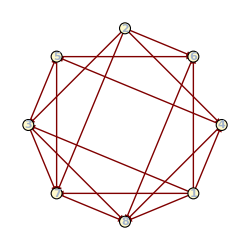
-Graphics--Graphics-

X_1[1,4]·X_1[4,8]·X_1[8,1] 1-a+X_1[1,7]·X_1[7,3]·X_1[3,1] 1-a+X_1[1,8]·X_1[8,6]·X_1[6,1] 1-a+X_1[3,7]·X_1[7,8]·X_1[8,3] 1-a+X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2] 1-a+X_1[2,7]·X_1[7,5]·X_1[5,6]·X_1[6,2] 1-a+X_1[1,7]·X_1[7,8]·X_1[8,1] -1+a+X_1[1,8]·X_1[8,3]·X_1[3,1] -1+a+X_1[2,7]·X_1[7,3]·X_1[3,2] -1+a+X_1[3,7]·X_1[7,5]·X_1[5,3] -1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] -1+a+X_1[2,4]·X_1[4,8]·X_1[8,6]·X_1[6,2] -1+a

```mathematica
Row[{
QuiverGraph[{4,6,2,5,3,7,8,1},Quiver[L131Z2PhaseA]],
(WL131Z2AFromDef1/.ChangeGroupIndices[{2,5,6,4,8,1,7,3}])//QuiverGraph[{4,6,2,5,3,7,8,1},#]&
}]
a W[L131Z2PhaseA]+(WL131Z2AFromDef1/.ChangeGroupIndices[{2,5,6,4,8,1,7,3}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

#### Deformation 2: (3→4→3) - (5→6→6)

```mathematica
δWC3Z4Z2Def2=m (Subscript[X, 1][3,4]·Subscript[X, 1][4,3]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]);
WC3Z4Z2Def2=WC3Z4Z2+δWC3Z4Z2Def2;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def2]
WC3Z4Z2Def2Min=WC3Z4Z2Def2/.Last@Solve[DG[WC3Z4Z2Def2,{%}]==0,%]//Expand
```

{X_1[3,4],X_1[4,3],X_1[5,6],X_1[6,5]}

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]-(X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1])/m+(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1])/m-(X_1[2,3]·X_1[3,1]·X_1[1,4]·X_1[4,2])/m+(X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2])/m+(X_1[3,1]·X_1[1,4]·X_1[4,2]·X_1[2,3])/m-(X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3])/m+(X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4])/m-(X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4])/m-(X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5])/m+(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/m

```mathematica
RedefChoice2={Subscript[γ, 1][1,2]->Subscript[β, 1][2,1],Subscript[γ, 1][2,1]->-1/m-Subscript[β, 1][2,1],Subscript[β, 1][7,8]->Subscript[γ, 1][8,7],Subscript[β, 1][1,2]->-1/m-Subscript[β, 1][2,1],Subscript[γ, 1][7,8]->Subscript[β, 1][8,7],Subscript[γ, 1][8,7]->-1/m-Subscript[β, 1][8,7],Subscript[α, 1][7,8]->1/m,Subscript[α, 1][2,1]->1/m,Subscript[α, 1][1,2]->1/m,Subscript[α, 1][8,7]->1/m};
RedefRules2=FieldRedefinition[{Subscript[X, 1][1,2], Subscript[X, 1][2,1],Subscript[X, 1][7,8], Subscript[X, 1][8,7]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice2;
RedefRules2Mass= {Subscript[X, 1][3,1]->m Subscript[X, 1][3,1],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2],Subscript[X, 1][7,5]->m Subscript[X, 1][7,5],Subscript[X, 1][8,1]->m Subscript[X, 1][8,1],Subscript[X, 1][8,6]->m Subscript[X, 1][8,6]};
RedefRules2//Column
RedefRules2Mass//Column
```

X_1[1,2]→X_1[1,7]·X_1[7,2] (-1/m-β_1[2,1])+X_1[1,4]·X_1[4,2] β_1[2,1]+X_1[1,2]/m
X_1[2,1]→X_1[2,3]·X_1[3,1] (-1/m-β_1[2,1])+X_1[2,8]·X_1[8,1] β_1[2,1]+X_1[2,1]/m
X_1[7,8]→X_1[7,5]·X_1[5,8] (-1/m-β_1[8,7])+X_1[7,2]·X_1[2,8] β_1[8,7]+X_1[7,8]/m
X_1[8,7]→X_1[8,1]·X_1[1,7] (-1/m-β_1[8,7])+X_1[8,6]·X_1[6,7] β_1[8,7]+X_1[8,7]/m

X_1[3,1]→m X_1[3,1]
X_1[4,2]→m X_1[4,2]
X_1[7,2]→m X_1[7,2]
X_1[7,5]→m X_1[7,5]
X_1[8,1]→m X_1[8,1]
X_1[8,6]→m X_1[8,6]

```mathematica
DG[FieldCases[RedefRules2]/.RedefRules2,{FieldCases[RedefRules2]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def2Min/.RedefRules2/.RedefRules2Mass//FTermsTable
```

X_1[1,2] | X_1[2,3]·X_1[3,1] -1+X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,4] | X_1[4,2]·X_1[2,1] -1+X_1[4,5]·X_1[5,3]·X_1[3,1] 1 | 0 | 2
X_1[1,7] | X_1[7,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,1] 1 | 0 | 2
X_1[2,1] | X_1[1,4]·X_1[4,2] -1+X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,3] | X_1[3,1]·X_1[1,2] -1+X_1[3,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[2,8] | X_1[8,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,2] 1 | 0 | 2
X_1[3,1] | X_1[1,2]·X_1[2,3] -1+X_1[1,4]·X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,7]·X_1[7,5]·X_1[5,3] -1+X_1[6,4]·X_1[4,2]·X_1[2,3] 1 | 0 | 2
X_1[4,2] | X_1[2,1]·X_1[1,4] -1+X_1[2,3]·X_1[3,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,8]·X_1[8,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,1]·X_1[1,4] 1 | 0 | 2
X_1[5,3] | X_1[3,6]·X_1[6,7]·X_1[7,5] -1+X_1[3,1]·X_1[1,4]·X_1[4,5] 1 | 0 | 2
X_1[5,8] | X_1[8,6]·X_1[6,4]·X_1[4,5] -1+X_1[8,7]·X_1[7,5] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,8]·X_1[8,6] -1+X_1[4,2]·X_1[2,3]·X_1[3,6] 1 | 0 | 2
X_1[6,7] | X_1[7,5]·X_1[5,3]·X_1[3,6] -1+X_1[7,8]·X_1[8,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,7] -1+X_1[2,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,3]·X_1[3,6]·X_1[6,7] -1+X_1[5,8]·X_1[8,7] 1 | 0 | 2
X_1[7,8] | X_1[8,1]·X_1[1,7] -1+X_1[8,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,8] -1+X_1[1,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,4]·X_1[4,5]·X_1[5,8] -1+X_1[6,7]·X_1[7,8] 1 | 0 | 2
X_1[8,7] | X_1[7,2]·X_1[2,8] -1+X_1[7,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WL131Z2AFromDef2=Simplify[WC3Z4Z2Def2Min/.RedefRules2/.RedefRules2Mass]
```

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]

```mathematica
Row[{
QuiverGraph[{4,6,2,5,3,7,8,1},QuiverFromFields@WL131Z2PhaseA],
(WL131Z2AFromDef2/.ChangeGroupIndices[{1,8,6,4,5,2,7,3}])//QuiverGraph[{4,6,2,5,3,7,8,1},#]&
}]
a WL131Z2PhaseA+(WL131Z2AFromDef2/.ChangeGroupIndices[{1,8,6,4,5,2,7,3}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

-Graphics--Graphics-

X_1[1,4]·X_1[4,8]·X_1[8,1] -1-a+X_1[1,7]·X_1[7,3]·X_1[3,1] -1-a+X_1[1,8]·X_1[8,6]·X_1[6,1] -1-a+X_1[3,7]·X_1[7,8]·X_1[8,3] -1-a+X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2] -1-a+X_1[2,7]·X_1[7,5]·X_1[5,6]·X_1[6,2] -1-a+X_1[1,7]·X_1[7,8]·X_1[8,1] 1+a+X_1[1,8]·X_1[8,3]·X_1[3,1] 1+a+X_1[2,7]·X_1[7,3]·X_1[3,2] 1+a+X_1[3,7]·X_1[7,5]·X_1[5,3] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+a+X_1[2,4]·X_1[4,8]·X_1[8,6]·X_1[6,2] 1+a

#### Deformation 3: (5→6→6) - (7→8→7)

```mathematica
δWC3Z4Z2Def3=m (Subscript[X, 1][5,6]·Subscript[X, 1][6,5]-Subscript[X, 1][7,8]·Subscript[X, 1][8,7]);
WC3Z4Z2Def3=WC3Z4Z2+δWC3Z4Z2Def3;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def3]
WC3Z4Z2Def3Min=WC3Z4Z2Def3/.Last@Solve[DG[WC3Z4Z2Def3,{%}]==0,%]//Expand
```

{X_1[5,6],X_1[6,5],X_1[7,8],X_1[8,7]}

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,4]·X_1[4,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]+X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,4]·X_1[4,3]+(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1])/m-(X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1])/m+(X_1[2,8]·X_1[8,1]·X_1[1,7]·X_1[7,2])/m-(X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2])/m-(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/m+(X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3])/m-(X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4])/m+(X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4])/m+(X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5])/m-(X_1[5,8]·X_1[8,1]·X_1[1,7]·X_1[7,5])/m-(X_1[6,7]·X_1[7,2]·X_1[2,8]·X_1[8,6])/m+(X_1[6,7]·X_1[7,5]·X_1[5,8]·X_1[8,6])/m-(X_1[7,2]·X_1[2,8]·X_1[8,1]·X_1[1,7])/m+(X_1[7,2]·X_1[2,8]·X_1[8,6]·X_1[6,7])/m+(X_1[7,5]·X_1[5,8]·X_1[8,1]·X_1[1,7])/m-(X_1[7,5]·X_1[5,8]·X_1[8,6]·X_1[6,7])/m

```mathematica
RedefChoice3={Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][1,2]->Subscript[β, 1][2,1],Subscript[γ, 1][2,1]->Subscript[β, 1][1,2],Subscript[γ, 1][4,3]->Subscript[β, 1][3,4],Subscript[β, 1][2,1]->-1/m-Subscript[β, 1][1,2],Subscript[β, 1][4,3]->-1/m-Subscript[β, 1][3,4],Subscript[α, 1][__]->1/m};
RedefRules3=FieldRedefinition[{Subscript[X, 1][1,2],Subscript[X, 1][2,1],Subscript[X, 1][3,4],Subscript[X, 1][4,3]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice3;
RedefRules3Mass= {Subscript[X, 1][3,1]->m Subscript[X, 1][3,1],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2],Subscript[X, 1][8,1]->m Subscript[X, 1][8,1]};
RedefRules3//Column
RedefRules3Mass//Column
```

X_1[1,2]→X_1[1,4]·X_1[4,2] (-1/m-β_1[1,2])+X_1[1,7]·X_1[7,2] β_1[1,2]+X_1[1,2]/m
X_1[2,1]→X_1[2,8]·X_1[8,1] (-1/m-β_1[1,2])+X_1[2,3]·X_1[3,1] β_1[1,2]+X_1[2,1]/m
X_1[3,4]→X_1[3,1]·X_1[1,4] (-1/m-β_1[3,4])+X_1[3,6]·X_1[6,4] β_1[3,4]+X_1[3,4]/m
X_1[4,3]→X_1[4,5]·X_1[5,3] (-1/m-β_1[3,4])+X_1[4,2]·X_1[2,3] β_1[3,4]+X_1[4,3]/m

X_1[3,1]→m X_1[3,1]
X_1[4,2]→m X_1[4,2]
X_1[5,3]→m X_1[5,3]
X_1[6,4]→m X_1[6,4]
X_1[7,2]→m X_1[7,2]
X_1[8,1]→m X_1[8,1]

```mathematica
DG[FieldCases[RedefRules3]/.RedefRules3,{FieldCases[RedefRules3]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def3Min/.RedefRules3/.RedefRules3Mass//FTermsTable
```

X_1[1,2] | X_1[2,3]·X_1[3,1] -1+X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,4] | X_1[4,2]·X_1[2,1] -1+X_1[4,3]·X_1[3,1] 1 | 0 | 2
X_1[1,7] | X_1[7,5]·X_1[5,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,1] 1 | 0 | 2
X_1[2,1] | X_1[1,4]·X_1[4,2] -1+X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,3] | X_1[3,1]·X_1[1,2] -1+X_1[3,4]·X_1[4,2] 1 | 0 | 2
X_1[2,8] | X_1[8,6]·X_1[6,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,2] 1 | 0 | 2
X_1[3,1] | X_1[1,2]·X_1[2,3] -1+X_1[1,4]·X_1[4,3] 1 | 0 | 2
X_1[3,4] | X_1[4,5]·X_1[5,3] -1+X_1[4,2]·X_1[2,3] 1 | 0 | 2
X_1[3,6] | X_1[6,4]·X_1[4,3] -1+X_1[6,7]·X_1[7,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,1]·X_1[1,4] -1+X_1[2,3]·X_1[3,4] 1 | 0 | 2
X_1[4,3] | X_1[3,6]·X_1[6,4] -1+X_1[3,1]·X_1[1,4] 1 | 0 | 2
X_1[4,5] | X_1[5,3]·X_1[3,4] -1+X_1[5,8]·X_1[8,6]·X_1[6,4] 1 | 0 | 2
X_1[5,3] | X_1[3,4]·X_1[4,5] -1+X_1[3,6]·X_1[6,7]·X_1[7,5] 1 | 0 | 2
X_1[5,8] | X_1[8,1]·X_1[1,7]·X_1[7,5] -1+X_1[8,6]·X_1[6,4]·X_1[4,5] 1 | 0 | 2
X_1[6,4] | X_1[4,3]·X_1[3,6] -1+X_1[4,5]·X_1[5,8]·X_1[8,6] 1 | 0 | 2
X_1[6,7] | X_1[7,2]·X_1[2,8]·X_1[8,6] -1+X_1[7,5]·X_1[5,3]·X_1[3,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,6]·X_1[6,7] -1+X_1[2,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,8]·X_1[8,1]·X_1[1,7] -1+X_1[5,3]·X_1[3,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,5]·X_1[5,8] -1+X_1[1,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,7]·X_1[7,2]·X_1[2,8] -1+X_1[6,4]·X_1[4,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WL131Z2AFromDef3=Simplify[WC3Z4Z2Def3Min/.RedefRules3/.RedefRules3Mass]
```

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,4]·X_1[4,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]+X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,4]·X_1[4,3]-X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]-X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]+X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]+X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]

```mathematica
Row[{
QuiverGraph[{4,6,2,5,3,7,8,1},QuiverFromFields@WL131Z2PhaseA],
(WL131Z2AFromDef3/.ChangeGroupIndices[{7,3,1,8,6,4,5,2}])//QuiverGraph[{4,6,2,5,3,7,8,1},#]&
}]
a WL131Z2PhaseA+(WL131Z2AFromDef3/.ChangeGroupIndices[{7,3,1,8,6,4,5,2}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

-Graphics--Graphics-

X_1[1,4]·X_1[4,8]·X_1[8,1] -1-a+X_1[1,7]·X_1[7,3]·X_1[3,1] -1-a+X_1[1,8]·X_1[8,6]·X_1[6,1] -1-a+X_1[3,7]·X_1[7,8]·X_1[8,3] -1-a+X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2] -1-a+X_1[2,7]·X_1[7,5]·X_1[5,6]·X_1[6,2] -1-a+X_1[1,7]·X_1[7,8]·X_1[8,1] 1+a+X_1[1,8]·X_1[8,3]·X_1[3,1] 1+a+X_1[2,7]·X_1[7,3]·X_1[3,2] 1+a+X_1[3,7]·X_1[7,5]·X_1[5,3] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+a+X_1[2,4]·X_1[4,8]·X_1[8,6]·X_1[6,2] 1+a

#### Deformation 0: (7→8→7) - (1→2→1)

```mathematica
δWC3Z4Z2Def0=m (Subscript[X, 1][7,8]·Subscript[X, 1][8,7]-Subscript[X, 1][1,2]·Subscript[X, 1][2,1]);
WC3Z4Z2Def0=WC3Z4Z2+δWC3Z4Z2Def0;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def0]
WC3Z4Z2Def0Min=WC3Z4Z2Def0/.Last@Solve[DG[WC3Z4Z2Def0,{%}]==0,%]//Expand
```

{X_1[1,2],X_1[2,1],X_1[7,8],X_1[8,7]}

X_1[1,4]·X_1[4,3]·X_1[3,1]+X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,4]·X_1[4,3]+X_1[3,6]·X_1[6,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]+(X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1])/m-(X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1])/m-(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1])/m+(X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1])/m-(X_1[2,8]·X_1[8,1]·X_1[1,7]·X_1[7,2])/m+(X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2])/m+(X_1[5,8]·X_1[8,1]·X_1[1,7]·X_1[7,5])/m-(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/m+(X_1[6,7]·X_1[7,2]·X_1[2,8]·X_1[8,6])/m-(X_1[6,7]·X_1[7,5]·X_1[5,8]·X_1[8,6])/m+(X_1[7,2]·X_1[2,8]·X_1[8,1]·X_1[1,7])/m-(X_1[7,2]·X_1[2,8]·X_1[8,6]·X_1[6,7])/m-(X_1[7,5]·X_1[5,8]·X_1[8,1]·X_1[1,7])/m+(X_1[7,5]·X_1[5,8]·X_1[8,6]·X_1[6,7])/m

```mathematica
RedefChoice0={Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][4,3]->-1/m-Subscript[β, 1][4,3],Subscript[β, 1][3,4]->-1/m-Subscript[β, 1][4,3],Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->-1/m-Subscript[β, 1][6,5],Subscript[β, 1][6,5]->-1/m-Subscript[β, 1][5,6],Subscript[α, 1][4,3]->1/m,Subscript[α, 1][3,4]->1/m,Subscript[α, 1][6,5]->1/m,Subscript[α, 1][5,6]->1/m};
RedefRules0=FieldRedefinition[{Subscript[X, 1][5,6], Subscript[X, 1][6,5],Subscript[X, 1][3,4],Subscript[X, 1][4,3]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice0;
RedefRules0Mass= {Subscript[X, 1][1,4]->m Subscript[X, 1][1,4],Subscript[X, 1][2,3]->m Subscript[X, 1][2,3],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,5]->m Subscript[X, 1][7,5],Subscript[X, 1][8,6]->m Subscript[X, 1][8,6]};
RedefRules0//Column
RedefRules0Mass//Column
```

X_1[5,6]→X_1[5,3]·X_1[3,6] (-1/m-β_1[5,6])+X_1[5,8]·X_1[8,6] β_1[5,6]+X_1[5,6]/m
X_1[6,5]→X_1[6,7]·X_1[7,5] (-1/m-β_1[5,6])+X_1[6,4]·X_1[4,5] β_1[5,6]+X_1[6,5]/m
X_1[3,4]→X_1[3,6]·X_1[6,4] (-1/m-β_1[4,3])+X_1[3,1]·X_1[1,4] β_1[4,3]+X_1[3,4]/m
X_1[4,3]→X_1[4,2]·X_1[2,3] (-1/m-β_1[4,3])+X_1[4,5]·X_1[5,3] β_1[4,3]+X_1[4,3]/m

X_1[1,4]→m X_1[1,4]
X_1[2,3]→m X_1[2,3]
X_1[5,3]→m X_1[5,3]
X_1[6,4]→m X_1[6,4]
X_1[7,5]→m X_1[7,5]
X_1[8,6]→m X_1[8,6]

```mathematica
DG[FieldCases[RedefRules0]/.RedefRules0,{FieldCases[RedefRules0]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def0Min/.RedefRules0/.RedefRules0Mass//FTermsTable
```

X_1[1,4] | X_1[4,2]·X_1[2,8]·X_1[8,1] -1+X_1[4,3]·X_1[3,1] 1 | 0 | 2
X_1[1,7] | X_1[7,2]·X_1[2,3]·X_1[3,1] -1+X_1[7,5]·X_1[5,8]·X_1[8,1] 1 | 0 | 2
X_1[2,3] | X_1[3,1]·X_1[1,7]·X_1[7,2] -1+X_1[3,4]·X_1[4,2] 1 | 0 | 2
X_1[2,8] | X_1[8,1]·X_1[1,4]·X_1[4,2] -1+X_1[8,6]·X_1[6,7]·X_1[7,2] 1 | 0 | 2
X_1[3,1] | X_1[1,7]·X_1[7,2]·X_1[2,3] -1+X_1[1,4]·X_1[4,3] 1 | 0 | 2
X_1[3,4] | X_1[4,5]·X_1[5,3] -1+X_1[4,2]·X_1[2,3] 1 | 0 | 2
X_1[3,6] | X_1[6,4]·X_1[4,3] -1+X_1[6,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,8]·X_1[8,1]·X_1[1,4] -1+X_1[2,3]·X_1[3,4] 1 | 0 | 2
X_1[4,3] | X_1[3,6]·X_1[6,4] -1+X_1[3,1]·X_1[1,4] 1 | 0 | 2
X_1[4,5] | X_1[5,3]·X_1[3,4] -1+X_1[5,6]·X_1[6,4] 1 | 0 | 2
X_1[5,3] | X_1[3,4]·X_1[4,5] -1+X_1[3,6]·X_1[6,5] 1 | 0 | 2
X_1[5,6] | X_1[6,7]·X_1[7,5] -1+X_1[6,4]·X_1[4,5] 1 | 0 | 2
X_1[5,8] | X_1[8,6]·X_1[6,5] -1+X_1[8,1]·X_1[1,7]·X_1[7,5] 1 | 0 | 2
X_1[6,4] | X_1[4,3]·X_1[3,6] -1+X_1[4,5]·X_1[5,6] 1 | 0 | 2
X_1[6,5] | X_1[5,8]·X_1[8,6] -1+X_1[5,3]·X_1[3,6] 1 | 0 | 2
X_1[6,7] | X_1[7,5]·X_1[5,6] -1+X_1[7,2]·X_1[2,8]·X_1[8,6] 1 | 0 | 2
X_1[7,2] | X_1[2,3]·X_1[3,1]·X_1[1,7] -1+X_1[2,8]·X_1[8,6]·X_1[6,7] 1 | 0 | 2
X_1[7,5] | X_1[5,6]·X_1[6,7] -1+X_1[5,8]·X_1[8,1]·X_1[1,7] 1 | 0 | 2
X_1[8,1] | X_1[1,4]·X_1[4,2]·X_1[2,8] -1+X_1[1,7]·X_1[7,5]·X_1[5,8] 1 | 0 | 2
X_1[8,6] | X_1[6,5]·X_1[5,8] -1+X_1[6,7]·X_1[7,2]·X_1[2,8] 1 | 0 | 2

```mathematica
WL131Z2AFromDef0=Simplify[WC3Z4Z2Def0Min/.RedefRules0/.RedefRules0Mass]
```

X_1[1,4]·X_1[4,3]·X_1[3,1]+X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,4]·X_1[4,3]+X_1[3,6]·X_1[6,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]-X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]+X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]+X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]

```mathematica
Row[{
QuiverGraph[{4,6,2,5,3,7,8,1},QuiverFromFields@WL131Z2PhaseA],
(WL131Z2AFromDef0/.ChangeGroupIndices[{5,2,7,3,1,8,6,4}])//QuiverGraph[{4,6,2,5,3,7,8,1},#]&
}]
a WL131Z2PhaseA+(WL131Z2AFromDef0/.ChangeGroupIndices[{5,2,7,3,1,8,6,4}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

-Graphics--Graphics-

X_1[1,4]·X_1[4,8]·X_1[8,1] -1-a+X_1[1,7]·X_1[7,3]·X_1[3,1] -1-a+X_1[1,8]·X_1[8,6]·X_1[6,1] -1-a+X_1[3,7]·X_1[7,8]·X_1[8,3] -1-a+X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2] -1-a+X_1[2,7]·X_1[7,5]·X_1[5,6]·X_1[6,2] -1-a+X_1[1,7]·X_1[7,8]·X_1[8,1] 1+a+X_1[1,8]·X_1[8,3]·X_1[3,1] 1+a+X_1[2,7]·X_1[7,3]·X_1[3,2] 1+a+X_1[3,7]·X_1[7,5]·X_1[5,3] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+a+X_1[2,4]·X_1[4,8]·X_1[8,6]·X_1[6,2] 1+a

### ℂ^3/ℤ_4×ℤ_2 ⟹ PdP_5 Phase A

#### Deformation 4 : (1→2→1) - (3→4→3) + (5→6→6) - (7→8→7)

```mathematica
δWC3Z4Z2Def4=m(Subscript[X, 1][1,2]·Subscript[X, 1][2,1]- Subscript[X, 1][3,4]·Subscript[X, 1][4,3]+ Subscript[X, 1][5,6]·Subscript[X, 1][6,5]-Subscript[X, 1][7,8]·Subscript[X, 1][8,7]);
WC3Z4Z2Def4=WC3Z4Z2+δWC3Z4Z2Def4;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def4]
WC3Z4Z2Def4Min=WC3Z4Z2Def4/.Last@Solve[DG[WC3Z4Z2Def4,{%}]==0,%]//Expand
```

{X_1[1,2],X_1[2,1],X_1[3,4],X_1[4,3],X_1[5,6],X_1[6,5],X_1[7,8],X_1[8,7]}

(X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1])/m-(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1])/m+(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1])/m-(X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1])/m+(X_1[2,3]·X_1[3,1]·X_1[1,4]·X_1[4,2])/m-(X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2])/m+(X_1[2,8]·X_1[8,1]·X_1[1,7]·X_1[7,2])/m-(X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2])/m-(X_1[3,1]·X_1[1,4]·X_1[4,2]·X_1[2,3])/m+(X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3])/m-(X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4])/m+(X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4])/m+(X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5])/m-(X_1[5,8]·X_1[8,1]·X_1[1,7]·X_1[7,5])/m-(X_1[6,7]·X_1[7,2]·X_1[2,8]·X_1[8,6])/m+(X_1[6,7]·X_1[7,5]·X_1[5,8]·X_1[8,6])/m-(X_1[7,2]·X_1[2,8]·X_1[8,1]·X_1[1,7])/m+(X_1[7,2]·X_1[2,8]·X_1[8,6]·X_1[6,7])/m+(X_1[7,5]·X_1[5,8]·X_1[8,1]·X_1[1,7])/m-(X_1[7,5]·X_1[5,8]·X_1[8,6]·X_1[6,7])/m

```mathematica
RedefRules4Mass= WC3Z4Z2Def4Min//MassShiftRules[m];
RedefRules4Mass//Column
WC3Z4Z2Def4Min/.RedefRules4Mass//FTermsTable
```

X_1[1,4]→m X_1[1,4]
X_1[1,7]→m X_1[1,7]
X_1[6,4]→m X_1[6,4]
X_1[6,7]→m X_1[6,7]

X_1[1,4] | X_1[4,5]·X_1[5,3]·X_1[3,1] -1+X_1[4,2]·X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,7] | X_1[7,5]·X_1[5,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,3]·X_1[3,1] 1 | 0 | 2
X_1[2,3] | X_1[3,6]·X_1[6,4]·X_1[4,2] -1+X_1[3,1]·X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,8] | X_1[8,6]·X_1[6,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,4]·X_1[4,2] 1 | 0 | 2
X_1[3,1] | X_1[1,4]·X_1[4,5]·X_1[5,3] -1+X_1[1,7]·X_1[7,2]·X_1[2,3] 1 | 0 | 2
X_1[3,6] | X_1[6,4]·X_1[4,2]·X_1[2,3] -1+X_1[6,7]·X_1[7,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,3]·X_1[3,6]·X_1[6,4] -1+X_1[2,8]·X_1[8,1]·X_1[1,4] 1 | 0 | 2
X_1[4,5] | X_1[5,3]·X_1[3,1]·X_1[1,4] -1+X_1[5,8]·X_1[8,6]·X_1[6,4] 1 | 0 | 2
X_1[5,3] | X_1[3,1]·X_1[1,4]·X_1[4,5] -1+X_1[3,6]·X_1[6,7]·X_1[7,5] 1 | 0 | 2
X_1[5,8] | X_1[8,1]·X_1[1,7]·X_1[7,5] -1+X_1[8,6]·X_1[6,4]·X_1[4,5] 1 | 0 | 2
X_1[6,4] | X_1[4,2]·X_1[2,3]·X_1[3,6] -1+X_1[4,5]·X_1[5,8]·X_1[8,6] 1 | 0 | 2
X_1[6,7] | X_1[7,2]·X_1[2,8]·X_1[8,6] -1+X_1[7,5]·X_1[5,3]·X_1[3,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,6]·X_1[6,7] -1+X_1[2,3]·X_1[3,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,8]·X_1[8,1]·X_1[1,7] -1+X_1[5,3]·X_1[3,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,5]·X_1[5,8] -1+X_1[1,4]·X_1[4,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,7]·X_1[7,2]·X_1[2,8] -1+X_1[6,4]·X_1[4,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WPdP5AFromDef4=Simplify[WC3Z4Z2Def4Min/.RedefRules4Mass]
```

X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]-X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]+X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]+X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]

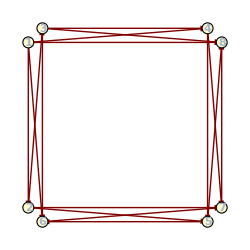
-Graphics--Graphics-

```mathematica
Row[{
QuiverGraph[{{8,4},{3,1},{2,6},{5,7}},Quiver[PdP5PhaseA]],
WPdP5AFromDef4/.ChangeGroupIndices[{4,6,3,5,2,8,1,7}]//QuiverGraph[{{8,4},{3,1},{2,6},{5,7}},#]&
},ImageSize->600]
```

```mathematica
a W[PdP5PhaseA]+(WPdP5AFromDef4/.ChangeGroupIndices[{4,6,3,5,2,8,1,7}])//Expand//Simplify//Collect[Expand@#,_CenterDot,Highlighted]&
```

X_1[1,2]·X_1[2,7]·X_1[7,4]·X_1[4,1] -1-a+X_1[1,6]·X_1[6,7]·X_1[7,8]·X_1[8,1] -1-a+X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2] -1-a+X_1[3,8]·X_1[8,5]·X_1[5,6]·X_1[6,3] -1-a+X_1[1,2]·X_1[2,3]·X_1[3,8]·X_1[8,1] 1+a+X_1[1,6]·X_1[6,3]·X_1[3,4]·X_1[4,1] 1+a+X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2] 1+a+X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4] 1+a

### ℂ^3/ℤ_4×ℤ_2 ⟹ PdP_5 Phase B

#### Deformation 5: (1→2→1) - (5→6→6)

```mathematica
δWC3Z4Z2Def5=m (Subscript[X, 1][1,2]·Subscript[X, 1][2,1]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]);
WC3Z4Z2Def5=WC3Z4Z2+δWC3Z4Z2Def5;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def5];
WC3Z4Z2Def5Min=WC3Z4Z2Def5/.Last@Solve[DG[WC3Z4Z2Def5,{%}]==0,%]//Expand
```

X_1[1,4]·X_1[4,3]·X_1[3,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]+X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,4]·X_1[4,3]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]-(X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1])/m+(X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1])/m+(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1])/m-(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1])/m+(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/m-(X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3])/m+(X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4])/m-(X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4])/m-(X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5])/m+(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/m

```mathematica
RedefChoice5={Subscript[γ, 1][3,4]->Subscript[β, 1][4,3],Subscript[γ, 1][8,7]->Subscript[β, 1][7,8],Subscript[γ, 1][4,3]->Subscript[β, 1][3,4],Subscript[γ, 1][7,8]->Subscript[β, 1][8,7],Subscript[β, 1][4,3]->1/m-Subscript[β, 1][3,4],Subscript[β, 1][8,7]->-1/m-Subscript[β, 1][7,8],Subscript[α, 1][8,7]->1/m,Subscript[α, 1][7,8]->1/m,Subscript[α, 1][4,3]->-1/m,Subscript[α, 1][3,4]->-1/m}
RedefRules5=FieldRedefinition[{Subscript[X, 1][7,8],Subscript[X, 1][8,7],Subscript[X, 1][3,4],Subscript[X, 1][4,3]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice5;
RedefRules5Mass= {Subscript[X, 1][1,7]->m Subscript[X, 1][1,7],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 1][4,3]->m Subscript[X, 1][4,3],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][8,6]->m Subscript[X, 1][8,6],Subscript[X, 1][8,7]->m Subscript[X, 1][8,7]};
RedefRules5//Column
RedefRules5Mass//Column
```

{γ_1[3,4]→β_1[4,3],γ_1[8,7]→β_1[7,8],γ_1[4,3]→β_1[3,4],γ_1[7,8]→β_1[8,7],β_1[4,3]→1/m-β_1[3,4],β_1[8,7]→-1/m-β_1[7,8],α_1[8,7]→1/m,α_1[7,8]→1/m,α_1[4,3]→-1/m,α_1[3,4]→-1/m}

X_1[7,8]→X_1[7,2]·X_1[2,8] (-1/m-β_1[7,8])+X_1[7,5]·X_1[5,8] β_1[7,8]+X_1[7,8]/m
X_1[8,7]→X_1[8,6]·X_1[6,7] (-1/m-β_1[7,8])+X_1[8,1]·X_1[1,7] β_1[7,8]+X_1[8,7]/m
X_1[3,4]→X_1[3,1]·X_1[1,4] (1/m-β_1[3,4])+X_1[3,6]·X_1[6,4] β_1[3,4]-X_1[3,4]/m
X_1[4,3]→X_1[4,5]·X_1[5,3] (1/m-β_1[3,4])+X_1[4,2]·X_1[2,3] β_1[3,4]-X_1[4,3]/m

X_1[1,7]→m X_1[1,7]
X_1[4,2]→m X_1[4,2]
X_1[4,3]→m X_1[4,3]
X_1[5,3]→m X_1[5,3]
X_1[8,6]→m X_1[8,6]
X_1[8,7]→m X_1[8,7]

```mathematica
DG[FieldCases[RedefRules5]/.RedefRules5,{FieldCases[RedefRules5]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def5Min/.RedefRules5/.RedefRules5Mass//FTermsTable
```

X_1[1,4] | X_1[4,3]·X_1[3,1] -1+X_1[4,2]·X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,7] | X_1[7,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,3]·X_1[3,1] 1 | 0 | 2
X_1[2,3] | X_1[3,4]·X_1[4,2] -1+X_1[3,1]·X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,8] | X_1[8,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,4]·X_1[4,2] 1 | 0 | 2
X_1[3,1] | X_1[1,4]·X_1[4,3] -1+X_1[1,7]·X_1[7,2]·X_1[2,3] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,7]·X_1[7,5]·X_1[5,3] -1+X_1[6,4]·X_1[4,3] 1 | 0 | 2
X_1[4,2] | X_1[2,3]·X_1[3,4] -1+X_1[2,8]·X_1[8,1]·X_1[1,4] 1 | 0 | 2
X_1[4,3] | X_1[3,1]·X_1[1,4] -1+X_1[3,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,8]·X_1[8,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,3] | X_1[3,6]·X_1[6,7]·X_1[7,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,8] | X_1[8,6]·X_1[6,4]·X_1[4,5] -1+X_1[8,7]·X_1[7,5] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,8]·X_1[8,6] -1+X_1[4,3]·X_1[3,6] 1 | 0 | 2
X_1[6,7] | X_1[7,5]·X_1[5,3]·X_1[3,6] -1+X_1[7,8]·X_1[8,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,7] -1+X_1[2,3]·X_1[3,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,3]·X_1[3,6]·X_1[6,7] -1+X_1[5,8]·X_1[8,7] 1 | 0 | 2
X_1[7,8] | X_1[8,1]·X_1[1,7] -1+X_1[8,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,8] -1+X_1[1,4]·X_1[4,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,4]·X_1[4,5]·X_1[5,8] -1+X_1[6,7]·X_1[7,8] 1 | 0 | 2
X_1[8,7] | X_1[7,2]·X_1[2,8] -1+X_1[7,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WPdP5BFromDef5=Simplify[WC3Z4Z2Def5Min/.RedefRules5/.RedefRules5Mass]
```

-(X_1[1,4]·X_1[4,3]·X_1[3,1])-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,6]·X_1[6,4]·X_1[4,3]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]

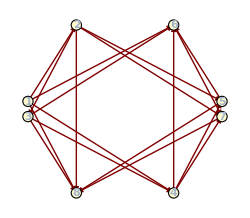
-Graphics--Graphics-

X_1[1,4]·X_1[4,6]·X_1[6,1] 1-a+X_1[1,8]·X_1[8,2]·X_1[2,1] 1-a+X_1[2,8]·X_1[8,7]·X_1[7,2] 1-a+X_1[4,7]·X_1[7,6]·X_1[6,4] 1-a+X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2] 1-a+X_1[3,8]·X_1[8,5]·X_1[5,6]·X_1[6,3] 1-a+X_1[2,3]·X_1[3,8]·X_1[8,2] -1+a+X_1[2,8]·X_1[8,5]·X_1[5,2] -1+a+X_1[3,4]·X_1[4,6]·X_1[6,3] -1+a+X_1[4,5]·X_1[5,6]·X_1[6,4] -1+a+X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,1] -1+a+X_1[1,8]·X_1[8,7]·X_1[7,6]·X_1[6,1] -1+a

```mathematica
Row[{
QuiverGraph[Model[{"PdP5","PhaseB"},"QuiverPositioning"],Quiver[PdP5PhaseB]],
(WPdP5BFromDef5/.ChangeGroupIndices[{5,3,8,2,1,7,6,4}])//QuiverGraph[Model[{"PdP5","PhaseB"},"QuiverPositioning"],#]&
}]
a W[PdP5PhaseB]+(WPdP5BFromDef5/.ChangeGroupIndices[{5,3,8,2,1,7,6,4}])//Simplify//Expand@Collect[Expand@#,_CenterDot,Highlighted]&
```

#### Deformation 6: (3→4→3) - (7→8→7)

```mathematica
δWC3Z4Z2Def6=m(Subscript[X, 1][3,4]·Subscript[X, 1][4,3]-Subscript[X, 1][7,8]·Subscript[X, 1][8,7]);
WC3Z4Z2Def6=WC3Z4Z2+δWC3Z4Z2Def6;
```

```mathematica
massiveFieldsFrom[WC3Z4Z2Def6]
WC3Z4Z2Def6Min=WC3Z4Z2Def6/.Last@Solve[DG[WC3Z4Z2Def6,{%}]==0,%]//Expand
```

{X_1[3,4],X_1[4,3],X_1[7,8],X_1[8,7]}

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]+X_1[3,6]·X_1[6,5]·X_1[5,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]-(X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1])/m+(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1])/m+(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1])/m-(X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1])/m-(X_1[2,3]·X_1[3,1]·X_1[1,4]·X_1[4,2])/m+(X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2])/m+(X_1[2,8]·X_1[8,1]·X_1[1,7]·X_1[7,2])/m-(X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2])/m+(X_1[3,1]·X_1[1,4]·X_1[4,2]·X_1[2,3])/m-(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/m-(X_1[5,8]·X_1[8,1]·X_1[1,7]·X_1[7,5])/m+(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/m-(X_1[6,7]·X_1[7,2]·X_1[2,8]·X_1[8,6])/m+(X_1[6,7]·X_1[7,5]·X_1[5,8]·X_1[8,6])/m-(X_1[7,2]·X_1[2,8]·X_1[8,1]·X_1[1,7])/m+(X_1[7,2]·X_1[2,8]·X_1[8,6]·X_1[6,7])/m+(X_1[7,5]·X_1[5,8]·X_1[8,1]·X_1[1,7])/m-(X_1[7,5]·X_1[5,8]·X_1[8,6]·X_1[6,7])/m

```mathematica
RedefChoice6={Subscript[γ, 1][1,2]->Subscript[β, 1][2,1],Subscript[γ, 1][2,1]->Subscript[β, 1][1,2],Subscript[β, 1][2,1]->-1/m-Subscript[β, 1][1,2],Subscript[γ, 1][5,6]->Subscript[β, 1][6,5],Subscript[γ, 1][6,5]->Subscript[β, 1][5,6],Subscript[β, 1][6,5]->1/m-Subscript[β, 1][5,6],Subscript[α, 1][1,2]->1/m,Subscript[α, 1][2,1]->1/m,Subscript[α, 1][6,5]->-1/m,Subscript[α, 1][5,6]->-1/m}
RedefRules6=FieldRedefinition[{Subscript[X, 1][1,2],Subscript[X, 1][2,1],Subscript[X, 1][6,5],Subscript[X, 1][5,6]},QuiverFromFields@WC3Z4Z2,2]//.RedefChoice6;
RedefRules6Mass= {Subscript[X, 1][3,1]->m Subscript[X, 1][3,1],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 1][5,6]->m Subscript[X, 1][5,6],Subscript[X, 1][6,5]->m Subscript[X, 1][6,5],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2],Subscript[X, 1][8,1]->m Subscript[X, 1][8,1]};
RedefRules6//Column
RedefRules6Mass//Column
```

{γ_1[1,2]→β_1[2,1],γ_1[2,1]→β_1[1,2],β_1[2,1]→-1/m-β_1[1,2],γ_1[5,6]→β_1[6,5],γ_1[6,5]→β_1[5,6],β_1[6,5]→1/m-β_1[5,6],α_1[1,2]→1/m,α_1[2,1]→1/m,α_1[6,5]→-1/m,α_1[5,6]→-1/m}

X_1[1,2]→X_1[1,4]·X_1[4,2] (-1/m-β_1[1,2])+X_1[1,7]·X_1[7,2] β_1[1,2]+X_1[1,2]/m
X_1[2,1]→X_1[2,8]·X_1[8,1] (-1/m-β_1[1,2])+X_1[2,3]·X_1[3,1] β_1[1,2]+X_1[2,1]/m
X_1[6,5]→X_1[6,7]·X_1[7,5] (1/m-β_1[5,6])+X_1[6,4]·X_1[4,5] β_1[5,6]-X_1[6,5]/m
X_1[5,6]→X_1[5,3]·X_1[3,6] (1/m-β_1[5,6])+X_1[5,8]·X_1[8,6] β_1[5,6]-X_1[5,6]/m

X_1[3,1]→m X_1[3,1]
X_1[4,2]→m X_1[4,2]
X_1[5,6]→m X_1[5,6]
X_1[6,5]→m X_1[6,5]
X_1[7,2]→m X_1[7,2]
X_1[8,1]→m X_1[8,1]

```mathematica
DG[FieldCases[RedefRules6]/.RedefRules6,{FieldCases[RedefRules6]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WC3Z4Z2Def6Min/.RedefRules6/.RedefRules6Mass//FTermsTable
```

X_1[1,2] | X_1[2,3]·X_1[3,1] -1+X_1[2,8]·X_1[8,1] 1 | 0 | 2
X_1[1,4] | X_1[4,2]·X_1[2,1] -1+X_1[4,5]·X_1[5,3]·X_1[3,1] 1 | 0 | 2
X_1[1,7] | X_1[7,5]·X_1[5,8]·X_1[8,1] -1+X_1[7,2]·X_1[2,1] 1 | 0 | 2
X_1[2,1] | X_1[1,4]·X_1[4,2] -1+X_1[1,7]·X_1[7,2] 1 | 0 | 2
X_1[2,3] | X_1[3,1]·X_1[1,2] -1+X_1[3,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[2,8] | X_1[8,6]·X_1[6,7]·X_1[7,2] -1+X_1[8,1]·X_1[1,2] 1 | 0 | 2
X_1[3,1] | X_1[1,2]·X_1[2,3] -1+X_1[1,4]·X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,5]·X_1[5,3] -1+X_1[6,4]·X_1[4,2]·X_1[2,3] 1 | 0 | 2
X_1[4,2] | X_1[2,1]·X_1[1,4] -1+X_1[2,3]·X_1[3,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,1]·X_1[1,4] 1 | 0 | 2
X_1[5,3] | X_1[3,6]·X_1[6,5] -1+X_1[3,1]·X_1[1,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,7]·X_1[7,5] 1 | 0 | 2
X_1[5,8] | X_1[8,1]·X_1[1,7]·X_1[7,5] -1+X_1[8,6]·X_1[6,5] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,3]·X_1[3,6] 1 | 0 | 2
X_1[6,5] | X_1[5,3]·X_1[3,6] -1+X_1[5,8]·X_1[8,6] 1 | 0 | 2
X_1[6,7] | X_1[7,2]·X_1[2,8]·X_1[8,6] -1+X_1[7,5]·X_1[5,6] 1 | 0 | 2
X_1[7,2] | X_1[2,8]·X_1[8,6]·X_1[6,7] -1+X_1[2,1]·X_1[1,7] 1 | 0 | 2
X_1[7,5] | X_1[5,8]·X_1[8,1]·X_1[1,7] -1+X_1[5,6]·X_1[6,7] 1 | 0 | 2
X_1[8,1] | X_1[1,7]·X_1[7,5]·X_1[5,8] -1+X_1[1,2]·X_1[2,8] 1 | 0 | 2
X_1[8,6] | X_1[6,7]·X_1[7,2]·X_1[2,8] -1+X_1[6,5]·X_1[5,8] 1 | 0 | 2

```mathematica
WPdP5BFromDef6=Simplify[WC3Z4Z2Def6Min/.RedefRules6/.RedefRules6Mass]
```

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,2]·X_1[2,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]-X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[5,6]·X_1[6,7]·X_1[7,5]+X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]-X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]+X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]

```mathematica
Row[{
QuiverGraph[Model[{"PdP5","PhaseB"},"QuiverPositioning"],Quiver[PdP5PhaseB]],
(WPdP5BFromDef6/.ChangeGroupIndices[{2,8,5,3,4,6,1,7}])//QuiverGraph[Model[{"PdP5","PhaseB"},"QuiverPositioning"],#]&
}]
a W[PdP5PhaseB]+(WPdP5BFromDef6/.ChangeGroupIndices[{2,8,5,3,4,6,1,7}])//Simplify//Expand@Collect[Expand@#,_CenterDot,Highlighted]&
```

-Graphics--Graphics-

X_1[1,4]·X_1[4,6]·X_1[6,1] 1-a+X_1[1,8]·X_1[8,2]·X_1[2,1] 1-a+X_1[2,8]·X_1[8,7]·X_1[7,2] 1-a+X_1[4,7]·X_1[7,6]·X_1[6,4] 1-a+X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2] 1-a+X_1[3,8]·X_1[8,5]·X_1[5,6]·X_1[6,3] 1-a+X_1[2,3]·X_1[3,8]·X_1[8,2] -1+a+X_1[2,8]·X_1[8,5]·X_1[5,2] -1+a+X_1[3,4]·X_1[4,6]·X_1[6,3] -1+a+X_1[4,5]·X_1[5,6]·X_1[6,4] -1+a+X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,1] -1+a+X_1[1,8]·X_1[8,7]·X_1[7,6]·X_1[6,1] -1+a

### L_(1,3,1)/ℤ_2 (a) ⟹ Marginal deformation of PdP_5 (a)

#### Deformation 1: (3→7→3) - (1→8→1)

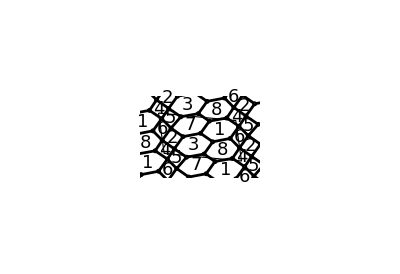

```mathematica
BraneTilingGraph[WL131Z2PhaseA]
```

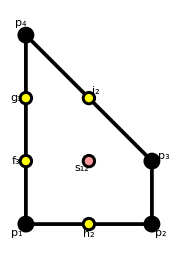
-Graphics- | {0,-1} | 6 | 3 | X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]-X_1[2,4]·X_1[4,8]·X_1[8,3]·X_1[3,2] | 2.21525
 | {0,-1} | 6 | 3 | -(X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1])+X_1[2,4]·X_1[4,8]·X_1[8,3]·X_1[3,2] | 2.21525
 | {1,0} | 4 | 2 | {X_1[2,7]·X_1[7,5]·X_1[5,3]·X_1[3,2],-(X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1])} | 2.4305
 | {1,1} | 6 | 3 | X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]-X_1[2,7]·X_1[7,8]·X_1[8,6]·X_1[6,2] | 2.21525
 | {1,1} | 6 | 3 | -(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1])+X_1[2,7]·X_1[7,8]·X_1[8,6]·X_1[6,2] | 2.21525
 | {-1,0} | 4 | 2 | X_1[1,8]·X_1[8,1]-X_1[2,4]·X_1[4,5]·X_1[5,6]·X_1[6,2] | 1.5695
 | {-1,0} | 4 | 2 | -(X_1[3,7]·X_1[7,3])+X_1[2,4]·X_1[4,5]·X_1[5,6]·X_1[6,2] | 1.5695
 | {-1,0} | 4 | 2 | -(X_1[1,8]·X_1[8,1])+X_1[3,7]·X_1[7,3] | 1.5695

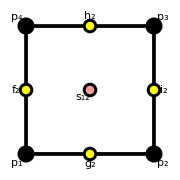
-Graphics- | {0,-1} | 4 | 2 | X_1[1,2]·X_1[2,7]·X_1[7,8]·X_1[8,1]-X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3] | 2.
 | {0,-1} | 4 | 2 | -(X_1[1,2]·X_1[2,7]·X_1[7,8]·X_1[8,1])+X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3] | 2.
 | {1,0} | 4 | 2 | X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]-X_1[5,6]·X_1[6,7]·X_1[7,8]·X_1[8,5] | 2.
 | {1,0} | 4 | 2 | -(X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1])+X_1[5,6]·X_1[6,7]·X_1[7,8]·X_1[8,5] | 2.
 | {0,1} | 4 | 2 | X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,1]-X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2] | 2.
 | {0,1} | 4 | 2 | -(X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,1])+X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2] | 2.
 | {-1,0} | 4 | 2 | X_1[1,6]·X_1[6,3]·X_1[3,8]·X_1[8,1]-X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2] | 2.
 | {-1,0} | 4 | 2 | -(X_1[1,6]·X_1[6,3]·X_1[3,8]·X_1[8,1])+X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2] | 2.

```mathematica
ZigZagDataGrid[WL131Z2PhaseA]
ZigZagDataGrid[WPdP5PhaseA]
```

```mathematica
WL131Z2PhaseADef1=WL131Z2PhaseA+μ(Subscript[X, 1][3,7]·Subscript[X, 1][7,3]-Subscript[X, 1][1,8]·Subscript[X, 1][8,1])//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP5PhaseADefFrom1=WPdP5PhaseA+1/μ(-(Subscript[X, 1][1,6]·Subscript[X, 1][6,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,1])+Subscript[X, 1][2,7]·Subscript[X, 1][7,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2])//IntegrateOutMassTerms//Expand;
```

```mathematica
L131Z2PhaseADef1QuiverIso=Values@*KeySort/@FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseADef1,Graph@Values@QuiverFromFields@WPdP5PhaseADefFrom1,All];
L131Z2PhaseADef1PotIso=AssociationMap[
Simplify[WL131Z2PhaseADef1/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseADef1,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],L131Z2PhaseADef1QuiverIso,Tuples[x],1]
])
];
```

```mathematica
DeleteCases[{}]@Map[
w↦Block[{massRedef,cases},
massRedef=MapIndexed[#1->μ^(p@@#2)#1&,FieldCases@w];
cases=Replace[l_List/;MemberQ[l,False]->{}]@Cases[
Collect[(w/.massRedef)-(WPdP5PhaseADefFrom1)//Simplify,_CenterDot,Highlighted],
Highlighted[x_]:>Simplify[x==0,μ>0],
Infinity
];
If[cases=={},{},
DeleteCases[massRedef/.First[FindInstance[Join[PowerExpand@Map[Log,cases,{2}]/.Log[μ]->1,Thread[-1<=Array[p,Length@massRedef]<=1]],Array[p,Length@massRedef],Integers],{}],HoldPattern[Rule][z_,z_|μ^p[_] z_]]
]
],
L131Z2PhaseADef1PotIso
]//KeyMap[Union@*Map[Splice@*Thread@*MapApply[List]]]
```

<|{1→4,2→8,3→3,4→5,5→6,6→7,7→1,8→2}→{X_1[2,3]→μ X_1[2,3],X_1[4,1]→μ X_1[4,1]},{1→2,2→6,3→1,4→7,5→8,6→5,7→3,8→4}→{X_1[2,3]→μ X_1[2,3],X_1[4,1]→μ X_1[4,1]}|>

#### Deformation 1 (from ℂ^3/ℤ_4×ℤ_2 )

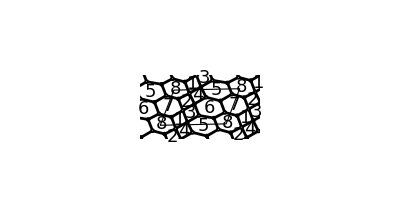

```mathematica
BraneTilingGraph[WL131Z2AFromDef1]
```

```mathematica
First@SeibergDual[4]@WL131Z2AFromDef1;
ZigZagPerfectMatchings[%]
KeyTake[Keys@%]@ZigZagOperator[%%]
```

<|X_1[1,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,4]·X_1[4,1]→{{p_1,h_1},{h_2,p_2}},X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,5]·X_1[5,3]·X_1[3,1]→{{p_1,h_2},{h_1,p_2}},X_1[1,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]·X_1[2,3]·X_1[3,1]→{{p_2,p_3}},X_1[2,3]·X_1[3,6]·X_1[6,5]·X_1[5,8]·X_1[8,7]·X_1[7,2]→{{p_3,i_1},{i_2,p_4}},X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,7]·X_1[7,8]·X_1[8,1]→{{p_3,i_2},{i_1,p_4}},X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1]→{{p_4,g_1},{g_2,f_1},{g_3,f_2},{f_3,p_1}},X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5]→{{p_4,g_2},{g_1,f_1},{g_3,f_3},{f_2,p_1}},X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,2]·X_1[2,4]·X_1[4,1]→{{p_4,g_3},{g_1,f_2},{g_2,f_3},{f_1,p_1}}|>

<|X_1[1,2]·X_1[2,8]·X_1[8,7]·X_1[7,5]·X_1[5,4]·X_1[4,1]→{-(X_1[1,5]·X_1[5,8]·X_1[8,1]),X_1[2,4]·X_1[4,6]·X_1[6,7]·X_1[7,2]},X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,5]·X_1[5,3]·X_1[3,1]→{X_1[1,5]·X_1[5,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,2])},X_1[1,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]·X_1[2,3]·X_1[3,1]→{-(X_1[1,7]·X_1[7,2]·X_1[2,4]·X_1[4,1]),X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]},X_1[2,3]·X_1[3,6]·X_1[6,5]·X_1[5,8]·X_1[8,7]·X_1[7,2]→{X_1[2,8]·X_1[8,6]·X_1[6,2],-(X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1])},X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,7]·X_1[7,8]·X_1[8,1]→{X_1[1,7]·X_1[7,5]·X_1[5,4]·X_1[4,1],-(X_1[2,8]·X_1[8,6]·X_1[6,2])},X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1]→{-(X_1[1,2]·X_1[2,3]·X_1[3,1]),X_1[7,8]·X_1[8,7]},X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5]→{X_1[4,6]·X_1[6,5]·X_1[5,4],-(X_1[7,8]·X_1[8,7])},X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,2]·X_1[2,4]·X_1[4,1]→{X_1[1,2]·X_1[2,3]·X_1[3,1],-(X_1[4,6]·X_1[6,5]·X_1[5,4])}|>

```mathematica
ZigZagDataGrid[WL131Z2AFromDef1]
ZigZagDataGrid[WPdP5PhaseA]
```

-Graphics- | {0,-1} | 6 | 3 | {X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,2],-(X_1[1,4]·X_1[4,5]·X_1[5,8]·X_1[8,1])} | 2.21525
 | {0,-1} | 6 | 3 | {X_1[1,4]·X_1[4,5]·X_1[5,8]·X_1[8,1],-(X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,2])} | 2.21525
 | {1,0} | 4 | 2 | {-(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1]),X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]} | 2.4305
 | {1,1} | 6 | 3 | {X_1[2,8]·X_1[8,6]·X_1[6,4]·X_1[4,2],-(X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1])} | 2.21525
 | {1,1} | 6 | 3 | {X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1],-(X_1[2,8]·X_1[8,6]·X_1[6,4]·X_1[4,2])} | 2.21525
 | {-1,0} | 4 | 2 | {-(X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]),X_1[7,8]·X_1[8,7]} | 1.5695
 | {-1,0} | 4 | 2 | {X_1[5,6]·X_1[6,5],-(X_1[7,8]·X_1[8,7])} | 1.5695
 | {-1,0} | 4 | 2 | {X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1],-(X_1[5,6]·X_1[6,5])} | 1.5695

-Graphics- | {0,-1} | 4 | 2 | {X_1[1,2]·X_1[2,7]·X_1[7,8]·X_1[8,1],-(X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3])} | 2.
 | {0,-1} | 4 | 2 | {-(X_1[1,2]·X_1[2,7]·X_1[7,8]·X_1[8,1]),X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3]} | 2.
 | {1,0} | 4 | 2 | {X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1],-(X_1[5,6]·X_1[6,7]·X_1[7,8]·X_1[8,5])} | 2.
 | {1,0} | 4 | 2 | {-(X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]),X_1[5,6]·X_1[6,7]·X_1[7,8]·X_1[8,5]} | 2.
 | {0,1} | 4 | 2 | {X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,1],-(X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2])} | 2.
 | {0,1} | 4 | 2 | {X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2],-(X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,1])} | 2.
 | {-1,0} | 4 | 2 | {-(X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2]),X_1[1,6]·X_1[6,3]·X_1[3,8]·X_1[8,1]} | 2.
 | {-1,0} | 4 | 2 | {-(X_1[1,6]·X_1[6,3]·X_1[3,8]·X_1[8,1]),X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2]} | 2.

```mathematica
WL131Z2PhaseADef1FromC3Z4Z2=WL131Z2AFromDef1+μ(Subscript[X, 1][5,6]·Subscript[X, 1][6,5]-(Subscript[X, 1][7,8]·Subscript[X, 1][8,7]))//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP5PhaseADefFromC3Z4Z2=WPdP5AFromDef4+(1/μ)Total@ZigZagOperator[WPdP5AFromDef4,Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]]//Expand
```

X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]+(X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1])/μ-X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]-X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]-(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/μ+X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]+X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]

```mathematica
WL131Z2PhaseADef1FromC3Z4Z2QuiverIso=Values@*KeySort/@FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseADef1FromC3Z4Z2,Graph@Values@QuiverFromFields@WPdP5PhaseADefFromC3Z4Z2,All];
WL131Z2PhaseADef1FromC3Z4Z2PotIso=AssociationMap[
Simplify[WL131Z2PhaseADef1FromC3Z4Z2/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseADef1FromC3Z4Z2,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],WL131Z2PhaseADef1FromC3Z4Z2QuiverIso,Tuples[x],1]
])
];
```

```mathematica
DeleteCases[{}]@Map[
w↦Block[{massRedef,cases},
massRedef=MapIndexed[#1->μ^(p@@#2)#1&,FieldCases@w];
cases=Replace[l_List/;MemberQ[l,False]->{}]@Cases[
Collect[(w/.massRedef)-(WPdP5PhaseADefFromC3Z4Z2)//Simplify,_CenterDot,Highlighted],
Highlighted[x_]:>Simplify[x==0,μ>0],
Infinity
];
If[cases=={},{},
DeleteCases[massRedef/.First[FindInstance[Join[PowerExpand@Map[Log,cases,{2}]/.Log[μ]->1,Thread[0<=Array[p,Length@massRedef]<=1]],Array[p,Length@massRedef],Integers],{}],HoldPattern[Rule][z_,z_|μ^p[_] z_]]
]
],
WL131Z2PhaseADef1FromC3Z4Z2PotIso
]//KeyMap[Union@*Map[Splice@*Thread@*MapApply[List]]]
```

<|{1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8}→{X_1[7,5]→μ X_1[7,5],X_1[8,6]→μ X_1[8,6]},{1→2,2→1,3→4,4→3,5→6,6→5,7→8,8→7}→{X_1[7,5]→μ X_1[7,5],X_1[8,6]→μ X_1[8,6]}|>

### L_(1,3,1)/ℤ_2 (a) ⟹ Marginal deformation of PdP_5 (b)

#### Deformation 2: (1→8→1) - (2→4→5→6→2)

```mathematica
WL131Z2PhaseADef2=WL131Z2PhaseA+μ(Subscript[X, 1][1,8]·Subscript[X, 1][8,1]-(Subscript[X, 1][2,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]))//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP5PhaseBDefFrom2=W[PdP5PhaseB]+1/μ(-(Subscript[X, 1][1,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,1])+Subscript[X, 1][2,8]·Subscript[X, 1][8,2])//IntegrateOutMassTerms//Expand;
```

```mathematica
ZigZagDataGrid[WPdP5PhaseB]
```

-Graphics- | {0,-1} | 6 | 2 | {X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2],-(X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1])} | 2.
 | {0,-1} | 6 | 2 | {X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1],-(X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2])} | 2.
 | {1,0} | 4 | 2 | {-(X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1]),X_1[2,8]·X_1[8,2]} | 2.
 | {1,0} | 4 | 2 | {-(X_1[2,8]·X_1[8,2]),X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3]} | 2.
 | {0,1} | 6 | 2 | {-(X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]),X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3]} | 2.
 | {0,1} | 6 | 2 | {X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1],-(X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3])} | 2.
 | {-1,0} | 4 | 2 | {-(X_1[1,8]·X_1[8,7]·X_1[7,2]·X_1[2,1]),X_1[4,6]·X_1[6,4]} | 2.
 | {-1,0} | 4 | 2 | {X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2],-(X_1[4,6]·X_1[6,4])} | 2.

```mathematica
L131Z2PhaseADef2QuiverIso=Values@*KeySort/@
FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseADef2,Graph@Values@QuiverFromFields@WPdP5PhaseBDefFrom2,All];
L131Z2PhaseADef2PotIso=AssociationMap[
Simplify[WL131Z2PhaseADef2/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseADef2,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],L131Z2PhaseADef2QuiverIso,Tuples[x],1]
])
];
```

```mathematica
DeleteCases[{}]@Map[
w↦Block[{massRedef,cases},
massRedef=MapIndexed[#1->μ^(p@@#2)#1&,FieldCases@w];
cases=Replace[l_List/;MemberQ[l,False]->{}]@Cases[
Collect[(w/.massRedef)-WPdP5PhaseBDefFrom2//Simplify,_CenterDot,Highlighted],
Highlighted[x_]:>Simplify[x==0,μ>0],
Infinity
];
If[cases=={},{},
DeleteCases[massRedef/.First@FindInstance[Join[PowerExpand@Map[Log,cases,{2}]/.Log[μ]->1,Thread[0<=Array[p,Length@massRedef]<=1]],Array[p,Length@massRedef],Integers],HoldPattern[Rule][z_,z_]]
]
],
L131Z2PhaseADef2PotIso
]//KeyMap[Union@*Map[Splice@*Thread@*MapApply[List]]]
```

<|{1→1,2→3,3→6,4→8,5→5,6→2,7→4,8→7}→{X_1[2,1]→μ X_1[2,1],X_1[8,7]→μ X_1[8,7]},{1→7,2→5,3→4,4→2,5→3,6→8,7→6,8→1}→{X_1[2,1]→μ X_1[2,1],X_1[8,7]→μ X_1[8,7]}|>

```mathematica
{Subscript[X, 1][2,1]->μ Subscript[X, 1][2,1],Subscript[X, 1][8,7]->μ Subscript[X, 1][8,7]}/.ChangeGroupIndices[Reverse/@{1->1,2->3,3->6,4->8,5->5,6->2,7->4,8->7}]
```

{X_1[6,1]→μ X_1[6,1],X_1[4,8]→μ X_1[4,8]}

#### Deformation 3: (2→4→5→6→2) - (3→7→3)

```mathematica
WL131Z2PhaseADef3=WL131Z2PhaseA+μ(Subscript[X, 1][2,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]-(Subscript[X, 1][3,7]·Subscript[X, 1][7,3]))//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP5PhaseBDefFrom3=W[PdP5PhaseB]+1/μ(Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,2]-(Subscript[X, 1][4,6]·Subscript[X, 1][6,4]))//IntegrateOutMassTerms//Expand;
```

```mathematica
ZigZagDataGrid[WPdP5PhaseB]
```

-Graphics- | {0,-1} | 6 | 2 | -(X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1])+X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2] | 2.
 | {0,-1} | 6 | 2 | X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1]-X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2] | 2.
 | {1,0} | 4 | 2 | X_1[2,8]·X_1[8,2]-X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1] | 2.
 | {1,0} | 4 | 2 | -(X_1[2,8]·X_1[8,2])+X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3] | 2.
 | {0,1} | 6 | 2 | -(X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1])+X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3] | 2.
 | {0,1} | 6 | 2 | X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]-X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3] | 2.
 | {-1,0} | 4 | 2 | X_1[4,6]·X_1[6,4]-X_1[1,8]·X_1[8,7]·X_1[7,2]·X_1[2,1] | 2.
 | {-1,0} | 4 | 2 | -(X_1[4,6]·X_1[6,4])+X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2] | 2.

```mathematica
L131Z2PhaseADef3QuiverIso=Values@*KeySort/@
FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseADef3,Graph@Values@QuiverFromFields@WPdP5PhaseBDefFrom3,All];
L131Z2PhaseADef3PotIso=AssociationMap[
Simplify[WL131Z2PhaseADef3/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseADef3,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],L131Z2PhaseADef3QuiverIso,Tuples[x],1]
])
];
```

```mathematica
DeleteCases[{}]@Map[
w↦Block[{massRedef,cases},
massRedef=MapIndexed[#1->μ^(p@@#2)#1&,FieldCases@w];
cases=Replace[l_List/;MemberQ[l,False]->{}]@Cases[
Collect[(w/.massRedef)-WPdP5PhaseBDefFrom3//Simplify,_CenterDot,Highlighted],
Highlighted[x_]:>Simplify[x==0,μ>0],
Infinity
];
If[cases=={},{},
DeleteCases[massRedef/.First@FindInstance[Join[PowerExpand@Map[Log,cases,{2}]/.Log[μ]->1,Thread[0<=Array[p,Length@massRedef]<=1]],Array[p,Length@massRedef],Integers],HoldPattern[Rule][z_,z_]]
]
],
L131Z2PhaseADef3PotIso
]
```

<|{X_1[1,4]→X_1[8,7],X_1[1,7]→X_1[8,5],X_1[1,8]→X_1[8,2],X_1[2,4]→X_1[4,7],X_1[2,7]→X_1[4,5],X_1[3,1]→X_1[3,8],X_1[3,2]→X_1[3,4],X_1[4,5]→X_1[7,6],X_1[4,8]→X_1[7,2],X_1[5,3]→X_1[6,3],X_1[5,6]→X_1[6,1],X_1[6,1]→X_1[1,8],X_1[6,2]→X_1[1,4],X_1[7,5]→X_1[5,6],X_1[7,8]→X_1[5,2],X_1[8,1]→X_1[2,8],X_1[8,3]→X_1[2,3],X_1[8,6]→X_1[2,1]}→{X_1[4,5]→μ X_1[4,5],X_1[6,3]→μ X_1[6,3]},{X_1[1,4]→X_1[2,1],X_1[1,7]→X_1[2,3],X_1[1,8]→X_1[2,8],X_1[2,4]→X_1[6,1],X_1[2,7]→X_1[6,3],X_1[3,1]→X_1[5,2],X_1[3,2]→X_1[5,6],X_1[4,5]→X_1[1,4],X_1[4,8]→X_1[1,8],X_1[5,3]→X_1[4,5],X_1[5,6]→X_1[4,7],X_1[6,1]→X_1[7,2],X_1[6,2]→X_1[7,6],X_1[7,5]→X_1[3,4],X_1[7,8]→X_1[3,8],X_1[8,1]→X_1[8,2],X_1[8,3]→X_1[8,5],X_1[8,6]→X_1[8,7]}→{X_1[4,5]→μ X_1[4,5],X_1[6,3]→μ X_1[6,3]}|>

### L_(1,3,1)/ℤ_2 (b) ⟹ Marginal deformation of PdP_5 (c)

#### Deformation 1: (1→8→1) - (4→5→6→4)

```mathematica
WL131Z2PhaseBIntIn1=(WL131Z2PhaseB)-Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]+Subscript[X, 1][1,4]·Subscript[X, p@1][4,6]·Subscript[X, 1][6,1]+Subscript[X, p@1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]-Subscript[X, p@1][6,4]·Subscript[X, p@1][4,6];
```

```mathematica
WPdP5CFromL131Z2BIntIn1=WL131Z2PhaseBIntIn1-Total[Union@@List@@@Map[Simplify@CenterDot[DG[WL131Z2PhaseBIntIn1,#],#]&,{Subscript[X, 1][1,8],Subscript[X, 1][8,1],Subscript[X, 1][6,4],Subscript[X, p[1]][4,6]}]]+(-Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, p[1]][6,4]-Subscript[X, 1][4,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1]·Subscript[X, 1][1,4]+Subscript[X, 1][6,1]·Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]+Subscript[X, 1][3,1]·Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,3])//Simplify
```

X_1[2,3]·X_1[3,4]·X_1[4,2]+X_1[2,6]·X_1[6,7]·X_1[7,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[3,7]·X_1[7,8]·X_1[8,3]+X_1[4,5]·X_1[5,6]·X_p[1][6,4]-X_1[4,8]·X_1[8,6]·X_p[1][6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]+X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]-X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]+X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]

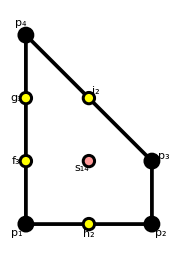
-Graphics- | {0,-1} | 6 | 3 | -(X_1[3,4]·X_1[4,8]·X_1[8,3])+X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,1] | 2.21525
 | {0,-1} | 8 | 3 | X_1[3,4]·X_1[4,8]·X_1[8,3]-X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1] | 2.21525
 | {1,0} | 6 | 2 | {-(X_1[2,6]·X_p[1][6,4]·X_1[4,2]),X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]} | 2.4305
 | {1,1} | 6 | 3 | -(X_1[6,7]·X_1[7,8]·X_1[8,6])+X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1] | 2.21525
 | {1,1} | 8 | 3 | X_1[6,7]·X_1[7,8]·X_1[8,6]-X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1] | 2.21525
 | {-1,0} | 4 | 2 | X_1[1,8]·X_1[8,1]-X_1[6,4]·X_p[1][4,6] | 1.5695
 | {-1,0} | 6 | 2 | -(X_1[2,3]·X_1[3,7]·X_1[7,2])+X_1[4,5]·X_1[5,6]·X_1[6,4] | 1.5695
 | {-1,0} | 4 | 2 | -(X_1[1,8]·X_1[8,1])+X_1[2,3]·X_1[3,7]·X_1[7,2] | 1.5695

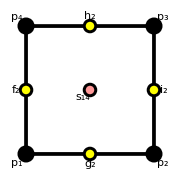
-Graphics- | {0,-1} | 6 | 2 | -(X_1[2,6]·X_p[1][6,4]·X_1[4,2])+X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1] | 2.
 | {0,-1} | 4 | 2 | X_1[2,6]·X_p[1][6,4]·X_1[4,2]-X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1] | 2.
 | {1,0} | 4 | 2 | -(X_1[6,7]·X_1[7,8]·X_1[8,6])+X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1] | 2.
 | {1,0} | 6 | 2 | X_1[6,7]·X_1[7,8]·X_1[8,6]-X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1] | 2.
 | {0,1} | 6 | 2 | -(X_1[2,3]·X_1[3,7]·X_1[7,2])+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] | 2.
 | {0,1} | 4 | 2 | X_1[2,3]·X_1[3,7]·X_1[7,2]-X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1] | 2.
 | {-1,0} | 4 | 2 | -(X_1[3,4]·X_1[4,8]·X_1[8,3])+X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,1] | 2.
 | {-1,0} | 6 | 2 | X_1[3,4]·X_1[4,8]·X_1[8,3]-X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1] | 2.

```mathematica
ZigZagDataGrid[WL131Z2PhaseBIntIn1]
ZigZagDataGrid[WPdP5CFromL131Z2BIntIn1]
```

```mathematica
WL131Z2PhaseBDef1=WL131Z2PhaseB+μ(Subscript[X, 1][1,8]·Subscript[X, 1][8,1]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4])//IntegrateOutMassTerms//Expand;
```

```mathematica
WPdP5PhaseCDefFrom1=WPdP5CFromL131Z2BIntIn1+ν(-(Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1])+Subscript[X, 1][2,6]·Subscript[X, p[1]][6,4]·Subscript[X, 1][4,2])//IntegrateOutMassTerms//ReplaceAll[Subscript[X, p[1]][6,4]->Subscript[X, 1][6,4]]//Expand;
```

```mathematica
ClearAll[possibleRedef]
possibleRedef[w_,h_:Identity]:=w/.FieldRedefinition[FieldCases[w],QuiverFromFields[w],2]/.{Subscript[x:$RedefinitionVars,k_]:>Subscript[x,h@k]}
```

```mathematica
L131Z2PhaseBDef1QuiverIso=Values@*KeySort/@
FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseBDef1,Graph@Values@QuiverFromFields@WPdP5PhaseCDefFrom1,All];
L131Z2PhaseBDef1PotIso=AssociationMap[
Simplify[WL131Z2PhaseBDef1/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseBDef1,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],L131Z2PhaseBDef1QuiverIso,Tuples[x],1]
])
];
Echo[L131Z2PhaseBDef1PotIso,"Len",Length];
res=MinimalBy[Count[_?(FreeQ[α])]]@Map[
Cases[Expand@Collect[Simplify@#,_CenterDot,Highlighted],Highlighted[x_]:>x,Infinity]&,
(possibleRedef/@L131Z2PhaseBDef1PotIso)-α possibleRedef[WPdP5PhaseCDefFrom1,q]
]
```

Len  24

<|{X_1[1,4]→X_1[1,4],X_1[1,7]→X_1[1,7],X_1[2,3]→X_1[2,3],X_1[2,6]→X_1[2,6],X_1[3,1]→X_1[3,1],X_1[3,4]→X_1[3,4],X_1[3,7]→X_1[3,7],X_1[4,2]→X_1[4,2],X_1[4,5]→X_1[4,5],X_1[4,8]→X_1[4,8],X_1[5,3]→X_1[5,3],X_1[5,6]→X_1[5,6],X_1[6,1]→X_1[6,1],X_1[6,4]→X_1[6,4],X_1[6,7]→X_1[6,7],X_1[7,2]→X_1[7,2],X_1[7,5]→X_1[7,5],X_1[7,8]→X_1[7,8],X_1[8,3]→X_1[8,3],X_1[8,6]→X_1[8,6]}→{-1+α,-α+1/μ,-α+1/μ,α_1[3,4]-α α_q[1][3,4],-α_1[3,4]+α α_q[1][3,4],α_1[3,7]-α α_q[1][3,7],-α_1[3,7]+α α_q[1][3,7],-μ α_1[6,4]-α α_q[1][6,4],α_1[6,4]+α α_q[1][6,4],-α_1[6,4]-α ν α_q[1][6,4],α_1[6,7]-α α_q[1][6,7],-α_1[6,7]+α α_q[1][6,7],β_1[3,4]-α β_q[1][3,4],-β_1[3,4]+α β_q[1][3,4],β_1[3,7]-α β_q[1][3,7],-1/μ+α ν-β_1[3,7]+α β_q[1][3,7],1-μ β_1[6,4]-α β_q[1][6,4],-1/μ+β_1[6,4]+α β_q[1][6,4],-β_1[6,4]-α (-1+ν β_q[1][6,4]),β_1[6,7]-α β_q[1][6,7],-β_1[6,7]+α β_q[1][6,7]}|>

```mathematica
sol={a[1]->0,a[2]->0,a[3]->0,a[4]->0,a[5]->0,a[6]->0,a[7]->0,a[8]->0,a[9]->0,a[10]->0,a[11]->0,a[12]->0,a[15]->0,a[19]->0,b[1]->0,b[2]->1,b[3]->1,b[4]->0,b[5]->0,b[6]->0,b[7]->0,b[8]->0,b[9]->1,b[10]->0,b[11]->0,b[12]->0,b[15]->0,b[19]->1,Subscript[α, 1][3,4]->1,Subscript[α, q[1]][3,4]->1,Subscript[α, 1][3,7]->1/μ,Subscript[α, 1][6,4]->-1/μ,Subscript[α, 1][6,7]->1,Subscript[α, q[1]][3,7]->1/μ,Subscript[α, q[1]][6,4]->1,Subscript[α, q[1]][6,7]->1,Subscript[β, 1][3,4]->0,Subscript[β, 1][3,7]->-1/μ,Subscript[β, 1][6,4]->1/μ,Subscript[β, 1][6,7]->0,Subscript[β, q[1]][3,4]->0,Subscript[β, q[1]][3,7]->-1/μ,Subscript[β, q[1]][6,4]->0,Subscript[β, q[1]][6,7]->0};
```

```mathematica
(L131Z2PhaseBDef1PotIso[[1]]/.{Subscript[X, 1][6,4]->(Subscript[X, 1][6,1]·Subscript[X, 1][1,4])/μ-(Subscript[X, 1][6,4])/μ}/.Thread[{Subscript[X, 1][1,4],Subscript[X, 1][8,6]}->μ{Subscript[X, 1][1,4],Subscript[X, 1][8,6]}])-(WPdP5PhaseCDefFrom1/.{ν->1/μ})//Simplify
```

0

```mathematica
IntegrateOutMassTerms[WL131Z2PhaseB+μ(Subscript[X, 1][1,8]·Subscript[X, 1][8,1]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4])]
%//ReplaceAll[{Subscript[X, 1][6,4]->(Subscript[X, 1][6,1]·Subscript[X, 1][1,4])/μ-(Subscript[X, 1][6,4])/μ}]//ReplaceAll[Thread[{Subscript[X, 1][1,4],Subscript[X, 1][8,6]}->μ{Subscript[X, 1][1,4],Subscript[X, 1][8,6]}]]//Simplify//Echo//Coefficient[#,μ,-1]&
```

X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,6]·X_1[6,4]·X_1[4,2]+X_1[2,6]·X_1[6,7]·X_1[7,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[3,7]·X_1[7,8]·X_1[8,3]-μ X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[4,8]·X_1[8,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]+(X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1])/μ-(X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1])/μ-X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-(X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1])/μ+(X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1])/μ

X_1[2,3]·X_1[3,4]·X_1[4,2]+(X_1[2,6]·X_1[6,4]·X_1[4,2])/μ+X_1[2,6]·X_1[6,7]·X_1[7,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[3,7]·X_1[7,8]·X_1[8,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[4,8]·X_1[8,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]+X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]-X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-(X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1])/μ+X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]

X_1[2,6]·X_1[6,4]·X_1[4,2]-X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]

#### Deformation 2: (1→8→1) - (2→3→7→2)

```mathematica
WL131Z2PhaseBIntIn2=(WL131Z2PhaseB)+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]-Subscript[X, 1][3,1]·Subscript[X, 1][1,7]·Subscript[X, p@1][7,3]-Subscript[X, p@1][3,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]+Subscript[X, p@1][3,7]·Subscript[X, p@1][7,3];
```

```mathematica
WPdP5CFromL131Z2BIntIn2=WL131Z2PhaseBIntIn2-Total[Union@@List@@@Map[Simplify@CenterDot[DG[WL131Z2PhaseBIntIn2,#],#]&,{Subscript[X, 1][1,8],Subscript[X, 1][8,1],Subscript[X, 1][3,7],Subscript[X, p[1]][7,3]}]]+
(X[3,1]·X[1,7]·X[7,5]·X[5,3]+X[3,7,p@1]·X[7,8]·X[8,3]-X[3,1]·X[1,4]·X[4,8]·X[8,3]-X[7,8]·X[8,6]·X[6,1]·X[1,7])//Simplify;
```

```mathematica
ZigZagDataGrid[WL131Z2PhaseBIntIn2]
ZigZagDataGrid[WPdP5CFromL131Z2BIntIn2]
```

-Graphics- | {0,-1} | 6 | 3 | {-(X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]),X_1[3,4]·X_1[4,8]·X_1[8,3]} | 2.21525
 | {1,0} | 6 | 2 | {-(X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]),X_1[5,3]·X_p[1][3,7]·X_1[7,5]} | 2.4305
 | {1,1} | 6 | 3 | {-(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]),X_1[6,7]·X_1[7,8]·X_1[8,6]} | 2.21525
 | {-1,0} | 4 | 2 | {X_1[1,8]·X_1[8,1],-(X_1[4,5]·X_1[5,6]·X_1[6,4])} | 1.5695
 | {-1,0} | 6 | 2 | {-(X_1[2,3]·X_1[3,7]·X_1[7,2]),X_1[4,5]·X_1[5,6]·X_1[6,4]} | 1.5695
 | {-1,0} | 4 | 2 | {-(X_1[1,8]·X_1[8,1]),X_1[3,7]·X_p[1][7,3]} | 1.5695

-Graphics- | {0,-1} | 4 | 2 | {X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1],-(X_1[4,5]·X_1[5,6]·X_1[6,4])} | 2.
 | {0,-1} | 6 | 2 | {-(X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]),X_1[4,5]·X_1[5,6]·X_1[6,4]} | 2.
 | {1,0} | 6 | 2 | {X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,1],-(X_1[3,4]·X_1[4,8]·X_1[8,3])} | 2.
 | {1,0} | 4 | 2 | {-(X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]),X_1[3,4]·X_1[4,8]·X_1[8,3]} | 2.
 | {0,1} | 4 | 2 | {X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1],-(X_1[5,3]·X_p[1][3,7]·X_1[7,5])} | 2.
 | {0,1} | 6 | 2 | {-(X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]),X_1[5,3]·X_p[1][3,7]·X_1[7,5]} | 2.
 | {-1,0} | 6 | 2 | {X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1],-(X_1[6,7]·X_1[7,8]·X_1[8,6])} | 2.
 | {-1,0} | 4 | 2 | {-(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]),X_1[6,7]·X_1[7,8]·X_1[8,6]} | 2.

```mathematica
WL131Z2PhaseBDef2=WL131Z2PhaseBIntIn2+μ(-(Subscript[X, 1][1,8]·Subscript[X, 1][8,1])+Subscript[X, 1][3,7]·Subscript[X, p[1]][7,3])//IntegrateOutMassTerms//ReplaceAll[Subscript[X, p[1]][3,7]->Subscript[X, 1][3,7]]//Expand;
```

```mathematica
WPdP5PhaseCDefFrom2=WPdP5CFromL131Z2BIntIn2+(1/μ)(Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]-(Subscript[X, 1][5,3]·Subscript[X, p[1]][3,7]·Subscript[X, 1][7,5]))//IntegrateOutMassTerms//ReplaceAll[Subscript[X, p[1]][3,7]->Subscript[X, 1][3,7]]//Expand;
```

```mathematica
ClearAll[possibleRedef]
possibleRedef[w_,h_:Identity]:=w/.FieldRedefinition[FieldCases[w],QuiverFromFields[w],2]/.{Subscript[x:$RedefinitionVars,k_]:>Subscript[x,h@k]}
```

```mathematica
L131Z2PhaseBDef2QuiverIso=Values@*KeySort/@
FindGraphIsomorphism[Graph@Values@QuiverFromFields@WL131Z2PhaseBDef2,Graph@Values@QuiverFromFields@WPdP5PhaseCDefFrom2,All];
L131Z2PhaseBDef2PotIso=AssociationMap[
Simplify[WL131Z2PhaseBDef2/.#]&,
Values@GroupBy[QuiverFromFields@WL131Z2PhaseBDef2,Identity,Sort@*Keys]//
(x↦Map[Thread[(Join@@x)->#]&,
Join@@Outer[CurryApplied[ReplaceAll@*ChangeGroupIndices,1],L131Z2PhaseBDef2QuiverIso,Tuples[x],1]
])
];
Echo[L131Z2PhaseBDef2PotIso,"Len",Length];
res=MinimalBy[Count[_?(FreeQ[α])]]@Map[
Cases[Expand@Collect[Simplify@#,_CenterDot,Highlighted@*Expand],Highlighted[x_]:>x,Infinity]&,
(possibleRedef/@L131Z2PhaseBDef2PotIso)-α possibleRedef[WPdP5PhaseCDefFrom2,q]
]
```

Len  24

<|{X_1[1,4]→X_1[1,4],X_1[1,7]→X_1[1,7],X_1[2,3]→X_1[2,3],X_1[2,6]→X_1[2,6],X_1[3,1]→X_1[3,1],X_1[3,4]→X_1[3,4],X_1[3,7]→X_1[3,7],X_1[4,2]→X_1[4,2],X_1[4,5]→X_1[4,5],X_1[4,8]→X_1[4,8],X_1[5,3]→X_1[5,3],X_1[5,6]→X_1[5,6],X_1[6,1]→X_1[6,1],X_1[6,4]→X_1[6,4],X_1[6,7]→X_1[6,7],X_1[7,2]→X_1[7,2],X_1[7,5]→X_1[7,5],X_1[7,8]→X_1[7,8],X_1[8,3]→X_1[8,3],X_1[8,6]→X_1[8,6]}→{1-α,α-1/μ,α-1/μ,α_1[3,4]-α α_q[1][3,4],-α_1[3,4]+α α_q[1][3,4],α_1[3,7]/μ-α α_q[1][3,7],-α_1[3,7]+α α_q[1][3,7],-α_1[3,7]/μ+(α α_q[1][3,7])/μ,α_1[6,4]-α α_q[1][6,4],-α_1[6,4]+α α_q[1][6,4],α_1[6,7]-α α_q[1][6,7],-α_1[6,7]+α α_q[1][6,7],β_1[3,4]-α β_q[1][3,4],-β_1[3,4]+α β_q[1][3,4],β_1[3,7]/μ-α β_q[1][3,7],-β_1[3,7]+α β_q[1][3,7],-α+1/μ-β_1[3,7]/μ+(α β_q[1][3,7])/μ,1/μ-α/μ+β_1[6,4]-α β_q[1][6,4],-β_1[6,4]+α β_q[1][6,4],β_1[6,7]-α β_q[1][6,7],-β_1[6,7]+α β_q[1][6,7]}|>

```mathematica
WPdP5PhaseCDefFrom2
```

X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,3]·X_1[3,7]·X_1[7,2]-X_1[2,6]·X_1[6,4]·X_1[4,2]+X_1[2,6]·X_1[6,7]·X_1[7,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[4,8]·X_1[8,6]·X_1[6,4]-(X_1[5,3]·X_1[3,7]·X_1[7,5])/μ-X_1[5,6]·X_1[6,7]·X_1[7,5]+X_1[7,8]·X_1[8,3]·X_1[3,7]+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]-X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]+(X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1])/μ+X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]-X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]

```mathematica
sol={Subscript[X, 1][1,7]->μ Subscript[X, 1][1,7],Subscript[X, 1][8,3]->μ Subscript[X, 1][8,3]};
(L131Z2PhaseBDef2PotIso[[1]]/.sol)-WPdP5PhaseCDefFrom2//Simplify
```

0

### L_(1,3,1)/ℤ_2 (b) ⟹ Marginal deformation of PdP_5 (c): (4→5→6→4) - (2→3→7→2) len=6 ???

#### PdP5 Phase B

```mathematica
WPdP5PhaseB//ZigZagData
```

<|X_1[2,8]·X_1[8,7]·X_1[7,6]·X_1[6,4]·X_1[4,5]·X_1[5,2]→{{0,-1},6,2,{X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2],-(X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1])},2.},X_1[1,4]·X_1[4,6]·X_1[6,3]·X_1[3,8]·X_1[8,2]·X_1[2,1]→{{0,-1},6,2,{X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1],-(X_1[2,3]·X_1[3,4]·X_1[4,7]·X_1[7,2])},2.},X_1[1,8]·X_1[8,7]·X_1[7,2]·X_1[2,1]→{{1,0},4,2,{-(X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1]),X_1[2,8]·X_1[8,2]},2.},X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2]→{{1,0},4,2,{-(X_1[2,8]·X_1[8,2]),X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3]},2.},X_1[2,8]·X_1[8,5]·X_1[5,6]·X_1[6,4]·X_1[4,7]·X_1[7,2]→{{0,1},6,2,{-(X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]),X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3]},2.},X_1[1,8]·X_1[8,2]·X_1[2,3]·X_1[3,4]·X_1[4,6]·X_1[6,1]→{{0,1},6,2,{X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1],-(X_1[3,8]·X_1[8,7]·X_1[7,6]·X_1[6,3])},2.},X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1]→{{-1,0},4,2,{-(X_1[1,8]·X_1[8,7]·X_1[7,2]·X_1[2,1]),X_1[4,6]·X_1[6,4]},2.},X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3]→{{-1,0},4,2,{X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2],-(X_1[4,6]·X_1[6,4])},2.}|>

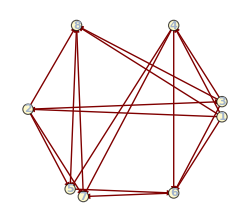

```mathematica
WPdP5PhaseB//QuiverGraph
```

```mathematica
WPdP5PhaseBtest1=WPdP5PhaseB+ν Total@ZigZagOperator[WPdP5PhaseB,Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3]]
```

-(X_1[1,4]·X_1[4,6]·X_1[6,1])-X_1[1,8]·X_1[8,2]·X_1[2,1]+X_1[2,3]·X_1[3,8]·X_1[8,2]+X_1[2,8]·X_1[8,5]·X_1[5,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[4,7]·X_1[7,6]·X_1[6,4]+X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,1]+X_1[1,8]·X_1[8,7]·X_1[7,6]·X_1[6,1]-X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2]+ν (-(X_1[4,6]·X_1[6,4])+X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2])-X_1[3,8]·X_1[8,5]·X_1[5,6]·X_1[6,3]

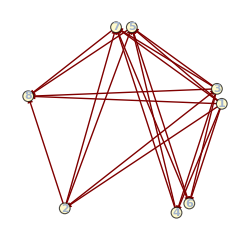
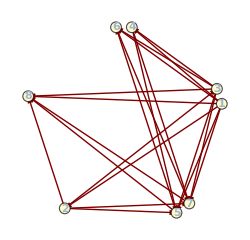

```mathematica
{SeibergDual[WPdP5PhaseBtest1,4][[1]]//QuiverGraph,SeibergDual[WPdP5PhaseBtest1,6][[1]]//QuiverGraph}
```

```mathematica
isom=FindGraphIsomorphism[
Values@QuiverFromFields@SeibergDual[WPdP5PhaseBtest1,4][[1]],
Values@Quiver@L131Z2PhaseB,
All
];
```

```mathematica
WL131Z2PhaseB+μ Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]]//Simplify;
coefsL131=AssociationMap[λ Coefficient[%,#]&,FieldProducts@%];
```

```mathematica
PdP5def=SeibergDual[WPdP5PhaseBtest1,4][[1]]/.ChangeGroupIndices[Normal@isom[[1]]]//Simplify;
PdP5def/.FieldRedefinition[FieldCases@PdP5def,QuiverFromFields@PdP5def,2]//ReplaceAll[{Subscript[α, _][__]->1,Subscript[β, 1][6,4]->0,Subscript[β, 1][3,4]->0,Subscript[β, 1][3,7]->0,Subscript[β, 1][6,7]->0}];
coefsPdP5=AssociationMap[Coefficient[%,#]&,FieldProducts@%];
Merge[{coefsL131,coefsPdP5},Highlighted]
```

<|X_1[1,4]·X_1[4,8]·X_1[8,1]→{-λ,1},X_1[1,7]·X_1[7,8]·X_1[8,1]→{λ,-1},X_1[1,8]·X_1[8,3]·X_1[3,1]→{λ,-1},X_1[1,8]·X_1[8,6]·X_1[6,1]→{-λ,1},X_1[2,3]·X_1[3,4]·X_1[4,2]→{λ,ζ[1]},X_1[2,3]·X_1[3,7]·X_1[7,2]→{-λ μ,ζ[2]},X_1[2,6]·X_1[6,4]·X_1[4,2]→{-λ,ζ[3]},X_1[2,6]·X_1[6,7]·X_1[7,2]→{λ,ζ[4]},X_1[3,4]·X_1[4,5]·X_1[5,3]→{-λ,-1/ν},X_1[3,7]·X_1[7,5]·X_1[5,3]→{λ,1/ν},X_1[3,7]·X_1[7,8]·X_1[8,3]→{-λ,1},X_1[4,5]·X_1[5,6]·X_1[6,4]→{λ μ,1/ν},X_1[4,8]·X_1[8,6]·X_1[6,4]→{λ,-1},X_1[5,6]·X_1[6,7]·X_1[7,5]→{-λ,-1/ν},X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→{λ,-1},X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]→{-λ},X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1]→{ν+β_1[8,1]+γ_1[1,8]},X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→{1},X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]→{-β_1[1,8]-γ_1[8,1]},X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]→{β_1[1,8]-β_1[8,1]},X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]→{-γ_1[1,8]+γ_1[8,1]}|>

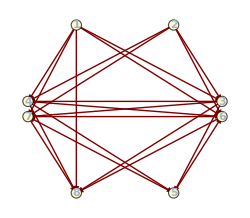

```mathematica
QuiverGraph@L131Z2PhaseB
```

#### Seiberg duality of zig-zag paths of L^131/ℤ_2 phase A (len=4) and phase B (len=6)

The tilings from the L^131/ℤ_2 phase A and B. The phase A has a zig-zag η_A=X_36X_64X_45X_53, with operator 𝒪_A =X_14X_42X_23X_31-X_56X_65. The duals of zig-zag is η_B=X_15X_53X_36X_62X_24X_41 of length 6 and 𝒪_B =X_12X_23X_31-X_46X_65X_54.

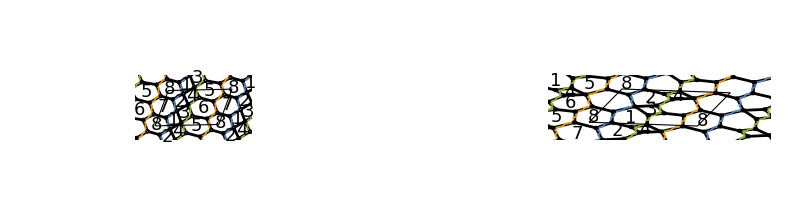

```mathematica
GraphicsRow[{BraneTilingGraph[WL131Z2AFromDef1,"ZigZags"->{Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1],Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5],Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]}],BraneTilingGraph[First@SeibergDual[WL131Z2AFromDef1,4],"ZigZags"->{Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1],Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5],Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,2]·Subscript[X, 1][2,4]·Subscript[X, 1][4,1]}]},ImageSize->Full]
```

For applying Seiberg duality, first let’s observer the quiver of phase A:

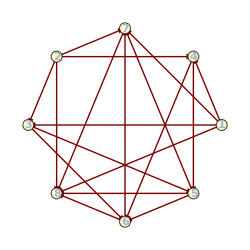

```mathematica
QuiverGraph@WL131Z2AFromDef1
```

Dualizing the node 4 we need to introduce composite fields, as well as Seiberg mesons:

```mathematica
TableForm[#,TableHeadings->{{M[1,1],M[1,2],M[2,1],M[2,2]},{"Phase A","Phase B",""}}]&@Join[KeyValueMap[{CenterDot@@#1,#2}&]@<|{Subscript[X, 1][1,4],Subscript[X, 1][4,2]}->Subscript[X, M[1,1]][1,2],{Subscript[X, 1][1,4],Subscript[X, 1][4,5]}->Subscript[X, M[1,2]][1,5],{Subscript[X, 1][6,4],Subscript[X, 1][4,2]}->Subscript[X, M[2,1]][6,2],{Subscript[X, 1][6,4],Subscript[X, 1][4,5]}->Subscript[X, M[2,2]][6,5]|>,Transpose@{{Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, C[2]][5,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]·Subscript[X, C[2]][5,4]}},2]
```

| Phase A | Phase B | 
M[1,1] | X_1[1,4]·X_1[4,2] | X_M[1,1][1,2] | X_Q[1][4,1]·X_M[1,1][1,2]·X_C[1][2,4]
M[1,2] | X_1[1,4]·X_1[4,5] | X_M[1,2][1,5] | X_Q[1][4,1]·X_M[1,2][1,5]·X_C[2][5,4]
M[2,1] | X_1[6,4]·X_1[4,2] | X_M[2,1][6,2] | X_Q[2][4,6]·X_M[2,1][6,2]·X_C[1][2,4]
M[2,2] | X_1[6,4]·X_1[4,5] | X_M[2,2][6,5] | X_Q[2][4,6]·X_M[2,2][6,5]·X_C[2][5,4]

Replacing this in the superpotential for phase A and adding the mesons with random signs we will fix to be:

```mathematica
{ζ[1]->-1,ζ[2]->1,ζ[3]->1,ζ[4]->-1}
```

{ζ[1]→-1,ζ[2]→1,ζ[3]→1,ζ[4]→-1}

The mutated potential, with deformation highlighted in yellow:

```mathematica
Simplify[(WL131Z2AFromDef1+Highlighted[μ Total@ZigZagOperator[WL131Z2AFromDef1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]]+Array[ζ,4].{Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, C[2]][5,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]·Subscript[X, C[2]][5,4]})/.KeyValueMap[
{k,v}↦HoldPattern[CenterDot][CyclicPatternSequence[l___,Sequence@@k,r___]]:>CenterDot[l,v,r],
<|{Subscript[X, 1][1,4],Subscript[X, 1][4,2]}->Subscript[X, M[1,1]][1,2],{Subscript[X, 1][1,4],Subscript[X, 1][4,5]}->Subscript[X, M[1,2]][1,5],{Subscript[X, 1][6,4],Subscript[X, 1][4,2]}->Subscript[X, M[2,1]][6,2],{Subscript[X, 1][6,4],Subscript[X, 1][4,5]}->Subscript[X, M[2,2]][6,5]|>
]/.{ζ[1]->-1,ζ[2]->1,ζ[3]->1,ζ[4]->-1}]
```

X_1[5,6]·X_M[2,2][6,5]-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,3]·X_1[3,6]·X_M[2,1][6,2]+X_1[2,8]·X_1[8,1]·X_M[1,1][1,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]-X_1[3,1]·X_M[1,2][1,5]·X_1[5,3]+X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]-X_C[1][2,4]·X_Q[1][4,1]·X_M[1,1][1,2]+X_C[1][2,4]·X_Q[2][4,6]·X_M[2,1][6,2]+X_C[2][5,4]·X_Q[1][4,1]·X_M[1,2][1,5]-X_C[2][5,4]·X_Q[2][4,6]·X_M[2,2][6,5]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]+μ (-(X_1[5,6]·X_1[6,5])+X_1[2,3]·X_1[3,1]·X_M[1,1][1,2])

F-terms from mass terms are:

```mathematica
Subscript[X, 1][5,6]·Subscript[X, M[2,2]][6,5]-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, 1][2,8]·Subscript[X, 1][8,1]·Subscript[X, M[1,1]][1,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]-Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]-Subscript[X, C[1]][2,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]+Subscript[X, C[1]][2,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, C[2]][5,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]-Subscript[X, C[2]][5,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]+μ (-(Subscript[X, 1][5,6]·Subscript[X, 1][6,5])+Subscript[X, 1][2,3]·Subscript[X, 1][3,1]·Subscript[X, M[1,1]][1,2])//DG[#,{FieldCases@Select[EqualTo[2]@*Length]@FieldProducts[#]}]&//Column
```

-(X_1[6,7]·X_1[7,5])-μ X_1[6,5]+X_M[2,2][6,5]
X_1[5,3]·X_1[3,6]-X_1[5,8]·X_1[8,6]-μ X_1[5,6]
-(X_C[2][5,4]·X_Q[2][4,6])+X_1[5,6]

We need to solve for X_M[2,2][6,5] and X_1[5,6], assuming the solution must hold also for μ→0.

```mathematica
Subscript[X, 1][5,6]·Subscript[X, M[2,2]][6,5]-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, 1][2,8]·Subscript[X, 1][8,1]·Subscript[X, M[1,1]][1,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]-Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]-Subscript[X, C[1]][2,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]+Subscript[X, C[1]][2,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, C[2]][5,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]-Subscript[X, C[2]][5,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]+μ (-(Subscript[X, 1][5,6]·Subscript[X, 1][6,5])+Subscript[X, 1][2,3]·Subscript[X, 1][3,1]·Subscript[X, M[1,1]][1,2])//First@Solve[0==DG[#,{FieldCases@Select[EqualTo[2]@*Length]@FieldProducts[#]}][[{1,3}]]]&//Column
```

X_1[5,6]→X_C[2][5,4]·X_Q[2][4,6]
X_M[2,2][6,5]→X_1[6,7]·X_1[7,5]+μ X_1[6,5]

The solution for X_M[2,2][6,5] is redundant because once we replace the value for X_1[5,6] the terms containing X_M[2,2][6,5]cancel. Therefore, result is:

```mathematica
Subscript[X, 1][5,6]·Subscript[X, M[2,2]][6,5]-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, 1][2,8]·Subscript[X, 1][8,1]·Subscript[X, M[1,1]][1,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]-Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]-Subscript[X, C[1]][2,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]+Subscript[X, C[1]][2,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, C[2]][5,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]-Subscript[X, C[2]][5,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]+μ (-(Subscript[X, 1][5,6]·Subscript[X, 1][6,5])+Subscript[X, 1][2,3]·Subscript[X, 1][3,1]·Subscript[X, M[1,1]][1,2])//Simplify[#/.First@Solve[0==DG[#,{FieldCases@Select[EqualTo[2]@*Length]@FieldProducts[#]}][[{1,3}]]]]&//(#/.μ->0)+Highlighted[μ Coefficient[#,μ]]&//Simplify
```

-(X_1[1,7]·X_1[7,8]·X_1[8,1])-X_1[2,3]·X_1[3,6]·X_M[2,1][6,2]+X_1[2,8]·X_1[8,1]·X_M[1,1][1,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]-X_1[3,1]·X_M[1,2][1,5]·X_1[5,3]+X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]-X_C[1][2,4]·X_Q[1][4,1]·X_M[1,1][1,2]+X_C[1][2,4]·X_Q[2][4,6]·X_M[2,1][6,2]+X_C[2][5,4]·X_Q[1][4,1]·X_M[1,2][1,5]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[6,7]·X_1[7,5]·X_C[2][5,4]·X_Q[2][4,6]+μ (X_1[2,3]·X_1[3,1]·X_M[1,1][1,2]-X_1[6,5]·X_C[2][5,4]·X_Q[2][4,6])

No more mass terms appear. We can also relabel the fields multiplicity. The superpotential is the same for phase B with the expected deformation.

```mathematica
Subscript[X, 1][5,6]·Subscript[X, M[2,2]][6,5]-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, 1][2,8]·Subscript[X, 1][8,1]·Subscript[X, M[1,1]][1,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]-Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,5]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]-Subscript[X, C[1]][2,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]+Subscript[X, C[1]][2,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]+Subscript[X, C[2]][5,4]·Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]-Subscript[X, C[2]][5,4]·Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]+μ (-(Subscript[X, 1][5,6]·Subscript[X, 1][6,5])+Subscript[X, 1][2,3]·Subscript[X, 1][3,1]·Subscript[X, M[1,1]][1,2])//Simplify[#/.First@Solve[0==DG[#,{FieldCases@Select[EqualTo[2]@*Length]@FieldProducts[#]}][[{1,3}]]]]&//RelabelFieldMultiplicity//(#/.μ->0)+Highlighted[μ Coefficient[#,μ]]&//Simplify
```

-(X_1[1,2]·X_1[2,4]·X_1[4,1])+X_1[1,2]·X_1[2,8]·X_1[8,1]-X_1[1,5]·X_1[5,3]·X_1[3,1]+X_1[1,5]·X_1[5,4]·X_1[4,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,3]·X_1[3,6]·X_1[6,2]+X_1[2,4]·X_1[4,6]·X_1[6,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[4,6]·X_1[6,7]·X_1[7,5]·X_1[5,4]+μ (X_1[1,2]·X_1[2,3]·X_1[3,1]-X_1[4,6]·X_1[6,5]·X_1[5,4])

#### Zig-zag deformation of L^131/ℤ_2 phase A to marginal deformation of PdP_5 phase B

From the model of L^131/ℤ_2 phase A we can obtain a marginal deformation of PdP_5 phase B, via triggering the zig-zag operator 𝒪_A =X_14X_42X_23X_31-X_56X_65, for the zig-zag η_A=X_36X_64X_45X_53. For this deformation we need to integrate-in the nodes along the zig-zag path. The two tilings before and after integrating in are:

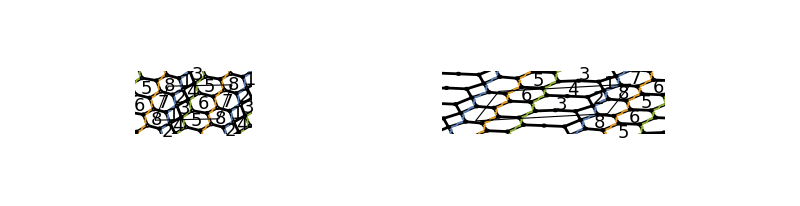

```mathematica
WL131Z2AFromDef1IntIn1=WL131Z2AFromDef1+
Subscript[X, 1][4,3]·Subscript[X, 1][3,4]+Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,3]-Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,3]-Subscript[X, 1][3,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,3]+
Subscript[X, 2][4,3]·Subscript[X, 2][3,4]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,4]·Subscript[X, 2][4,3]·Subscript[X, 1][3,1]-Subscript[X, 2][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]//Simplify;
GraphicsRow[{BraneTilingGraph[WL131Z2AFromDef1,"ZigZags"->{Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1],Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5],Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]}],BraneTilingGraph[
WL131Z2AFromDef1IntIn1,"ZigZags"->{Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1],Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5],Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]},"RotateTiling"->Pi]},ImageSize->Full]
```

By integrating-in along the zig-zag path, the operator now reads as 𝒪_A =X_43^1X_34^2-X_56X_65. The superpotential is

```mathematica
WL131Z2AFromDef1IntIn1+Highlighted[μ Total@ZigZagOperator[WL131Z2AFromDef1IntIn1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]]//Simplify
```

X_1[3,4]·X_1[4,3]+X_2[3,4]·X_2[4,3]-X_1[1,4]·X_2[4,3]·X_1[3,1]-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]-X_1[3,6]·X_1[6,4]·X_1[4,3]+X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[4,5]·X_1[5,3]·X_2[3,4]+X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[5,6]·X_1[6,7]·X_1[7,5]-X_1[5,8]·X_1[8,6]·X_1[6,5]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]+μ (X_1[4,3]·X_2[3,4]-X_1[5,6]·X_1[6,5])

We need to keep the mass term X_34^1X_43^2 because this will be part of the marginal operator from which we will approach PdP_5 phase B. For this reason we solve the F-terms associated to the deformation only, assuming μ ≠ 0. Therefore the F-terms give us

```mathematica
WL131Z2AFromDef1IntIn1+μ Total@ZigZagOperator[WL131Z2AFromDef1IntIn1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]//Expand@First@Solve[0==DG[#,{Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases}],Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases]&//Column
```

X_2[3,4]→(X_1[3,6]·X_1[6,4])/μ-X_1[3,4]/μ
X_1[4,3]→(X_1[4,5]·X_1[5,3])/μ-X_2[4,3]/μ
X_1[5,6]→(X_1[5,3]·X_1[3,6])/μ-(X_1[5,8]·X_1[8,6])/μ
X_1[6,5]→(X_1[6,4]·X_1[4,5])/μ-(X_1[6,7]·X_1[7,5])/μ

And replacing the solutions the result is

```mathematica
WL131Z2AFromDef1IntIn1+μ Total@ZigZagOperator[WL131Z2AFromDef1IntIn1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]//ReplaceAll[Expand@First@Solve[0==DG[#,{Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases}],Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases]][#]&//Simplify
```

1/μ(-(X_1[3,4]·X_2[4,3])-μ X_1[1,4]·X_2[4,3]·X_1[3,1]-μ X_1[1,7]·X_1[7,8]·X_1[8,1]-μ X_1[2,3]·X_1[3,4]·X_1[4,2]-μ X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,6]·X_1[6,4]·X_2[4,3]+μ X_1[5,8]·X_1[8,7]·X_1[7,5]+μ X_1[6,7]·X_1[7,8]·X_1[8,6]+μ X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]+μ X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]+X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])

We can apply the redefinition {X_1[5,3]→μ X_1[5,3],X_1[6,4]→μ X_1[6,4]} to recover the marginal deformation of PdP_5 phase B.

```mathematica
WL131Z2AFromDef1IntIn1+μ Total@ZigZagOperator[WL131Z2AFromDef1IntIn1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]//ReplaceAll[Expand@First@Solve[0==DG[#,{Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases}],Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases]][#]&//ReplaceAll[{Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][6,4]->μ Subscript[X, 1][6,4]}]//Simplify//((#/.Power[μ,-1]->0)+Highlighted[Coefficient[#,μ,-1]/μ])&//Simplify
```

-(X_1[1,4]·X_2[4,3]·X_1[3,1])-X_1[1,7]·X_1[7,8]·X_1[8,1]-X_1[2,3]·X_1[3,4]·X_1[4,2]-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,6]·X_1[6,4]·X_2[4,3]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]+(-(X_1[3,4]·X_2[4,3])+X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/μ

Removing the marginal deformation the tiling associated to the toric model is

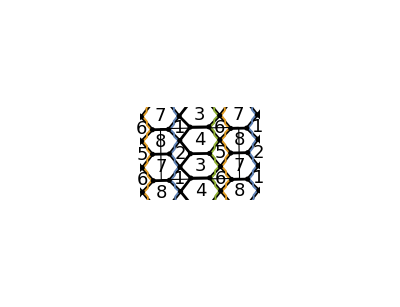

```mathematica
WL131Z2AFromDef1IntIn1+μ Total@ZigZagOperator[WL131Z2AFromDef1IntIn1,Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]]//ReplaceAll[Expand@First@Solve[0==DG[#,{Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases}],Subscript[X, 1][4,3]·Subscript[X, 2][3,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,5]//FieldCases]][#]&//ReplaceAll[{Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][6,4]->μ Subscript[X, 1][6,4]}]//Simplify//((#/.Power[μ,-1]->0))&//BraneTilingGraph[#,"ZigZags"->{Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1],Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5],Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]},"RotateTiling"->Pi]&
```

Here we cannot perform toric-Seiberg duality on node 4, which is the same node that connects the zig-zag η_A=X_36X_64X_45X_53 in  L^131/ℤ_2 phase A and the zig-zag η_B=X_15X_53X_36X_62X_24X_41 of length 6 in phase B.

#### Relating marginal deformation of PdP_5 phase B to marginal deformation of PdP_5 phase ??

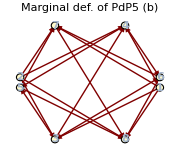
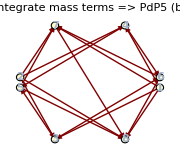
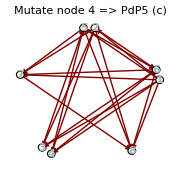

```mathematica
res=-(Subscript[X, 1][1,4]·Subscript[X, 2][4,3]·Subscript[X, 1][3,1])-Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,6]·Subscript[X, 1][6,4]·Subscript[X, 2][4,3]+Subscript[X, 1][5,8]·Subscript[X, 1][8,7]·Subscript[X, 1][7,5]+Subscript[X, 1][6,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,6]+Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,8]·Subscript[X, 1][8,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]-Subscript[X, 1][3,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]-Subscript[X, 1][4,5]·Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,4]+(-(Subscript[X, 1][3,4]·Subscript[X, 2][4,3])+Subscript[X, 1][5,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5])/μ//ReplaceAll[Framed[x_,___]:>x];
Row[{
QuiverGraph[%,ImageSize->Small,PlotLabel->"Marginal def. of PdP5 (b)"],
QuiverGraph[IntegrateOutMassTerms[%],ImageSize->Small,PlotLabel->"Integrate mass terms => PdP5 (b)"],
QuiverGraph[First@SeibergDual[IntegrateOutMassTerms[%],4],ImageSize->Small,PlotLabel->"Mutate node 4 => PdP5 (c)"]
},Spacer[5],ImageSize->Full]
```

```mathematica
TableForm@Expand@First@Solve[0==DG[res,{{Subscript[X, 1][3,4],Subscript[X, 2][4,3]}}],{Subscript[X, 1][3,4],Subscript[X, 2][4,3]}]
res2=res/.Normal[%]//Simplify;
```

X_1[3,4]→-μ X_1[3,1]·X_1[1,4]+μ X_1[3,6]·X_1[6,4]
X_2[4,3]→-μ X_1[4,2]·X_1[2,3]+μ X_1[4,5]·X_1[5,3]

```mathematica
TableForm[#,TableHeadings->{{M[1,1],M[1,2],M[2,1],M[2,2]},{"Phase A","Phase B",""}}]&@Join[KeyValueMap[{CenterDot@@#1,#2}&]@<|{Subscript[X, 1][1,4],Subscript[X, 1][4,2]}->Subscript[X, M[1,1]][1,2],{Subscript[X, 1][1,4],Subscript[X, 1][4,5]}->Subscript[X, M[1,2]][1,5],{Subscript[X, 1][6,4],Subscript[X, 1][4,2]}->Subscript[X, M[2,1]][6,2],{Subscript[X, 1][6,4],Subscript[X, 1][4,5]}->Subscript[X, M[2,2]][6,5]|>,Transpose@{{Subscript[X, Q[1]][4,1]·Subscript[X, M[1,1]][1,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[1]][4,1]·Subscript[X, M[1,2]][1,5]·Subscript[X, C[2]][5,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,1]][6,2]·Subscript[X, C[1]][2,4],Subscript[X, Q[2]][4,6]·Subscript[X, M[2,2]][6,5]·Subscript[X, C[2]][5,4]}},2]
```

| Phase A | Phase B | 
M[1,1] | X_1[1,4]·X_1[4,2] | X_M[1,1][1,2] | X_Q[1][4,1]·X_M[1,1][1,2]·X_C[1][2,4]
M[1,2] | X_1[1,4]·X_1[4,5] | X_M[1,2][1,5] | X_Q[1][4,1]·X_M[1,2][1,5]·X_C[2][5,4]
M[2,1] | X_1[6,4]·X_1[4,2] | X_M[2,1][6,2] | X_Q[2][4,6]·X_M[2,1][6,2]·X_C[1][2,4]
M[2,2] | X_1[6,4]·X_1[4,5] | X_M[2,2][6,5] | X_Q[2][4,6]·X_M[2,2][6,5]·X_C[2][5,4]

We apply the rules ζ[2] → 1, ζ[3] → 1, ζ[4] → -1, ζ[1] → -1, so that the F-terms of highlighted terms appear toric.
At this point, we can compute the chiral ring, which has the components:

```mathematica
ReplaceAll[{Subscript[X, 1][7,5]->Subscript[X, 1][7,5],Subscript[X, 1][8,6]->Subscript[X, 1][8,6],ζ[4]->ζ[1],ζ[2]->-ζ[1],ζ[3]->-ζ[1]}][res2]/.ζ[1]->-1
```

-(X_1[1,7]·X_1[7,8]·X_1[8,1])-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+μ X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-μ X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-μ X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]+μ X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]+(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/μ

```mathematica
WPdP5PhaseB//Length
```

12

```mathematica
ReplaceAll[{Subscript[X, 1][7,5]->Subscript[X, 1][7,5],Subscript[X, 1][8,6]->Subscript[X, 1][8,6],ζ[4]->ζ[1],ζ[2]->-ζ[1],ζ[3]->-ζ[1]}][res2]/.ζ[1]->-1//Simplify
```

-(X_1[1,7]·X_1[7,8]·X_1[8,1])-X_1[2,8]·X_1[8,7]·X_1[7,2]+X_1[5,8]·X_1[8,7]·X_1[7,5]+X_1[6,7]·X_1[7,8]·X_1[8,6]+μ X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]+X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]-μ X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]-μ X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]+μ X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]+(X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5])/μ

```mathematica
ReplaceAll[{Subscript[X, 1][7,5]->Subscript[X, 1][7,5],Subscript[X, 1][8,6]->Subscript[X, 1][8,6],ζ[4]->ζ[1],ζ[2]->-ζ[1],ζ[3]->-ζ[1]}][res2]/.ζ[1]->-1;
res2Chiral=MapKernelM2[
KeyValueReverse@Abelianize@ToGeneratorVariableRules@GaugeInvariantMesons[%,∞],
Abelianize@Join[Abelianize@FTerms[%]/.{Power[μ,p_?Negative]:>ν^-p}],
FieldCases[%],
"ParameterIdeal"->{ν μ -1}
];
res2ChiralMin=First@MinimalPresentationM2[res2Chiral,DeleteCases[μ|ν]@Variables@res2Chiral];
PrimaryDecompositionM2[res2ChiralMin,UniqueCases[res2ChiralMin,$GeneratorVars[_]]]//Column
```

{C[4]-C[13],-A[1]+C[16],C[7]-C[10],-1+μ ν,-A[1] C[11]+C[15]^2,-A[1] C[11]+C[10] C[13]-ν C[11] C[15],-μ A[1] C[11]+μ C[10] C[13]-C[11] C[15]}
{A[1],C[11],C[15],C[13],C[4],C[16]}
{A[1],C[11],C[15],C[10],C[16],C[7]}
{C[11],C[15],C[13],C[4],C[10],C[7]}
{C[11],C[15],C[13],C[4],-A[1]+C[16],C[7]-C[10]}
{C[11],C[15],C[4]-C[13],C[10],-A[1]+C[16],C[7]}

From these results we see that we see that the geometric ideal of the zig-zag marginal deformation of PdP5 phase C (or otherwise) matches the Seiberg dual model (node 4) of the marginal deformation of PdP5 phase B, obtained integrating out the massive terms associated to the phase B deformation. Integrating out the 2 bifundamentals, makes the node 4 to have N_f==2 N_c.

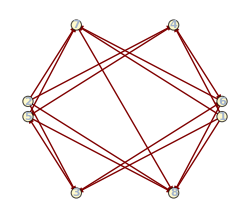

```mathematica
ReplaceAll[{Subscript[X, 1][7,5]->Subscript[X, 1][7,5],Subscript[X, 1][8,6]->Subscript[X, 1][8,6],ζ[4]->ζ[1],ζ[2]->-ζ[1],ζ[3]->-ζ[1]}][res2]/.ζ[1]->-1//QuiverGraph
```

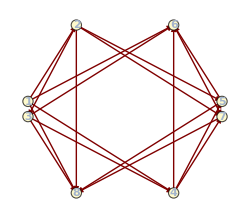

```mathematica
QuiverGraph@PdP5PhaseB
```

#### Testing Deformations

```mathematica
WL131Z2PhaseBDefLen6=WL131Z2PhaseB+μ Echo@Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]];
```

-(X_1[2,3]·X_1[3,7]·X_1[7,2])+X_1[4,5]·X_1[5,6]·X_1[6,4]

```mathematica
resBLen6=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseB,∞],
Abelianize@DG[WL131Z2PhaseBDefLen6,{FieldCases@WL131Z2PhaseBDefLen6}],
FieldCases@WL131Z2PhaseBDefLen6
];
```

```mathematica
{minChiralIBLen6,linChiralSolBLen6}=MinimalPresentationM2[resBLen6,DeleteCases[μ]@Variables@resBLen6];
```

```mathematica
mesIBLen6=Last@SortBy[LeafCount]@DeleteCases[{μ,__}]@PrimaryDecompositionM2[minChiralIBLen6,DeleteCases[μ]@Variables@minChiralIBLen6];
```

```mathematica
{minMesIBLen6,linMesSolBLen6}=MinimalPresentationM2[mesIBLen6,DeleteCases[μ]@Variables@mesIBLen6]
```

{{C[7]^2-B[7] C[12],C[3] C[10]-μ B[7] C[12]-C[7] C[12]},{A[1]→B[7],B[4]→B[7],B[5]→C[10],B[12]→C[3]}}

```mathematica
WL131Z2PhaseBDefLen4=WL131Z2PhaseB+μ Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]];
```

```mathematica
resBLen4=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseB,∞],
Abelianize@DG[WL131Z2PhaseBDefLen4,{FieldCases@WL131Z2PhaseBDefLen4}],
FieldCases@WL131Z2PhaseBDefLen4
];
```

```mathematica
{minChiralIBLen4,linChiralSolBLen4}=MinimalPresentationM2[resBLen4,DeleteCases[μ]@Variables@resBLen4];
```

```mathematica
mesIBLen4=Last@SortBy[LeafCount]@DeleteCases[{μ,__}]@PrimaryDecompositionM2[minChiralIBLen4,DeleteCases[μ]@Variables@minChiralIBLen4];
```

```mathematica
{minMesIBLen4,linMesSolBLen4}=MinimalPresentationM2[mesIBLen4,DeleteCases[μ]@Variables@mesIBLen4]
```

{{C[3] C[10]-C[7] C[12],μ B[7] C[7]+C[7]^2-B[7] C[12]},{A[1]→B[7],B[4]→B[7],B[5]→C[10],B[12]→C[3]}}

```mathematica
WL131Z2PhaseBDefLen4sec=WL131Z2PhaseB+μ Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]];
```

```mathematica
resBLen4sec=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseB,∞],
Abelianize@DG[WL131Z2PhaseBDefLen4sec,{FieldCases@WL131Z2PhaseBDefLen4sec}],
FieldCases@WL131Z2PhaseBDefLen4sec
];
```

```mathematica
{minChiralIBLen4sec,linChiralSolBLen4sec}=MinimalPresentationM2[resBLen4sec,DeleteCases[μ]@Variables@resBLen4sec];
```

```mathematica
mesIBLen4sec=Last@SortBy[LeafCount]@DeleteCases[{μ,__}]@PrimaryDecompositionM2[minChiralIBLen4sec,DeleteCases[μ]@Variables@minChiralIBLen4sec];
```

```mathematica
{minMesIBLen4sec,linMesSolBLen4sec}=MinimalPresentationM2[mesIBLen4sec,DeleteCases[μ]@Variables@mesIBLen4sec]
```

{{C[3] C[10]+μ B[7] C[12]-C[7] C[12],μ B[7] C[7]-C[7]^2+B[7] C[12],C[3] C[7] C[10]-B[7] C[12]^2},{A[1]→B[7],B[4]→B[7],B[5]→C[10],B[12]→C[3]}}

```mathematica
zzs={Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2],Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1],Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]};
```

```mathematica
CollectGen=Expand@Collect[Select[#,MatchQ[{2,_}]@*MinMaxExponent[$GeneratorVars[_]]],$GeneratorVars[_],Simplify@*Highlighted]&;
```

```mathematica
{C[7]^2-B[7] C[12],C[3] C[10]-μ B[7] C[12]-C[7] C[12]}[[{2,1}]]/.{C[12]-> C[12]-μ C[7]}//GroebnerBasis
{C[3] C[10]-C[7] C[12],μ B[7] C[7]+C[7]^2-B[7] C[12]}//GroebnerBasis
{μ B[7] C[7]-C[7]^2+B[7] C[12],C[3] C[10]+μ B[7] C[12]-C[7] C[12]}[[{2,1}]]/.{C[7]->C[7]+μ  B[7]}//GroebnerBasis
```

{μ B[7] C[7]+C[7]^2-B[7] C[12],C[3] C[10]-C[7] C[12]}

{μ B[7] C[7]+C[7]^2-B[7] C[12],C[3] C[10]-C[7] C[12]}

{μ B[7] C[7]+C[7]^2-B[7] C[12],C[3] C[10]-C[7] C[12]}

```mathematica
$EvaluationTimeOverflowM2=Infinity;
```

```mathematica
WL131Z2PhaseBDefDouble4=WL131Z2PhaseB+μ Echo@Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]]+ν Echo@Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]];
```

X_1[1,8]·X_1[8,1]-X_1[4,5]·X_1[5,6]·X_1[6,4]

-(X_1[1,8]·X_1[8,1])+X_1[2,3]·X_1[3,7]·X_1[7,2]

```mathematica
resBDouble4=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseB,∞],
Abelianize@DG[WL131Z2PhaseBDefDouble4,{FieldCases@WL131Z2PhaseBDefDouble4}],
FieldCases@WL131Z2PhaseBDefDouble4
];
```

```mathematica
{minChiralIBDouble4,linChiralSolBDouble4}=MinimalPresentationM2[resBDouble4,DeleteCases[μ|ν]@Variables@resBDouble4];
```

```mathematica
mesIBDouble4=Last@SortBy[LeafCount]@DeleteCases[{μ|ν,__}]@PrimaryDecompositionM2[minChiralIBDouble4,DeleteCases[μ|ν]@Variables@minChiralIBDouble4];
```

```mathematica
{minMesIBDouble4,linMesSolBDouble4}=MinimalPresentationM2[mesIBDouble4,DeleteCases[μ]@Variables@mesIBDouble4]
```

{{C[3] C[10]+μ B[7] C[12]-C[7] C[12],-μ B[7] C[7]+ν B[7] C[7]+C[7]^2-B[7] C[12],-μ C[3] C[7] C[10]+ν C[3] C[7] C[10]-ν C[7]^2 C[12]+μ B[7] C[12]^2},{A[1]→B[7],B[4]→B[7],B[5]→C[10],B[12]→C[3]}}

```mathematica
{C[3] C[10]+μ B[7] C[12]-C[7] C[12],-μ B[7] C[7]+ν B[7] C[7]+C[7]^2-B[7] C[12]}/.{C[7]->C[7]+μ B[7]}//FullSimplify
```

{C[3] C[10]-C[7] C[12],(μ B[7]+C[7]) (ν B[7]+C[7])-B[7] C[12]}

```mathematica
ZigZagData@WL131Z2PhaseB
```

<|X_1[1,8]·X_1[8,6]·X_1[6,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]→{{0,-1},6,3,{X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,1],-(X_1[3,4]·X_1[4,8]·X_1[8,3])},2.21525},X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,7]·X_1[7,8]·X_1[8,1]→{{0,-1},6,3,{-(X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]),X_1[3,4]·X_1[4,8]·X_1[8,3]},2.21525},X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,2]→{{1,0},6,2,{-(X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]),X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]},2.4305},X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,4]·X_1[4,8]·X_1[8,1]→{{1,1},6,3,{X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1],-(X_1[6,7]·X_1[7,8]·X_1[8,6])},2.21525},X_1[1,8]·X_1[8,3]·X_1[3,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]→{{1,1},6,3,{-(X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]),X_1[6,7]·X_1[7,8]·X_1[8,6]},2.21525},X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1]→{{-1,0},4,2,{X_1[1,8]·X_1[8,1],-(X_1[4,5]·X_1[5,6]·X_1[6,4])},1.5695},X_1[2,6]·X_1[6,7]·X_1[7,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→{{-1,0},6,2,{-(X_1[2,3]·X_1[3,7]·X_1[7,2]),X_1[4,5]·X_1[5,6]·X_1[6,4]},1.5695},X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]→{{-1,0},4,2,{-(X_1[1,8]·X_1[8,1]),X_1[2,3]·X_1[3,7]·X_1[7,2]},1.5695}|>

```mathematica
WL131Z2PhaseBDefTriple=WL131Z2PhaseB+
μ1 Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,4]·Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]]+
μ2 Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][1,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]]+
μ3 Total@ZigZagOperator[WL131Z2PhaseB,Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]];
```

```mathematica
RestartM2[];
Dynamic@RawSessionHistoryM2[]
```

```mathematica
resBTriple=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseBDefTriple,∞],
Abelianize@DG[WL131Z2PhaseBDefTriple,{FieldCases@WL131Z2PhaseBDefTriple}],
FieldCases@WL131Z2PhaseBDefTriple
];
```

```mathematica
Collect[Simplify@WL131Z2PhaseBDefTriple,c_CenterDot,Highlighted]
```

X_1[1,4]·X_1[4,8]·X_1[8,1] -1+X_1[1,8]·X_1[8,6]·X_1[6,1] -1+X_1[2,6]·X_1[6,4]·X_1[4,2] -1+X_1[3,4]·X_1[4,5]·X_1[5,3] -1+X_1[3,7]·X_1[7,8]·X_1[8,3] -1+X_1[5,6]·X_1[6,7]·X_1[7,5] -1+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1] -1+X_1[1,7]·X_1[7,8]·X_1[8,1] 1+X_1[1,8]·X_1[8,3]·X_1[3,1] 1+X_1[2,3]·X_1[3,4]·X_1[4,2] 1+X_1[2,6]·X_1[6,7]·X_1[7,2] 1+X_1[3,7]·X_1[7,5]·X_1[5,3] 1+X_1[4,8]·X_1[8,6]·X_1[6,4] 1+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+X_1[1,8]·X_1[8,1] μ1-μ2+X_1[2,3]·X_1[3,7]·X_1[7,2] μ2-μ3+X_1[4,5]·X_1[5,6]·X_1[6,4] -μ1+μ3

```mathematica
Collect[Simplify@WL131Z2PhaseBDefDouble4,c_CenterDot,Highlighted]
```

X_1[1,4]·X_1[4,8]·X_1[8,1] -1+X_1[1,8]·X_1[8,6]·X_1[6,1] -1+X_1[2,6]·X_1[6,4]·X_1[4,2] -1+X_1[3,4]·X_1[4,5]·X_1[5,3] -1+X_1[3,7]·X_1[7,8]·X_1[8,3] -1+X_1[5,6]·X_1[6,7]·X_1[7,5] -1+X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1] -1+X_1[1,7]·X_1[7,8]·X_1[8,1] 1+X_1[1,8]·X_1[8,3]·X_1[3,1] 1+X_1[2,3]·X_1[3,4]·X_1[4,2] 1+X_1[2,6]·X_1[6,7]·X_1[7,2] 1+X_1[3,7]·X_1[7,5]·X_1[5,3] 1+X_1[4,8]·X_1[8,6]·X_1[6,4] 1+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+X_1[4,5]·X_1[5,6]·X_1[6,4] -μ+X_1[1,8]·X_1[8,1] μ-ν+X_1[2,3]·X_1[3,7]·X_1[7,2] ν

```mathematica
μ-ν/.{μ->μ1-μ3,ν->μ2-μ3}
```

μ1-μ2

```mathematica
{C[3] C[10]-C[7] C[12],(μ B[7]+C[7]) (ν B[7]+C[7])-B[7] C[12]}/.{μ->μ1-μ3,ν->μ2-μ3}
```

{C[3] C[10]-C[7] C[12],((μ1-μ3) B[7]+C[7]) ((μ2-μ3) B[7]+C[7])-B[7] C[12]}

```mathematica
Eliminate[
0==ReplaceAll[Thread[{μ1,μ2,μ3}->Zeta/@{3,5,7}]]@Abelianize@Join[
Subtract@@@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WL131Z2PhaseBDefTriple,∞],
DG[WL131Z2PhaseBDefTriple,{FieldCases@WL131Z2PhaseBDefTriple}]
],
FieldCases@WL131Z2PhaseBDefTriple
]
```

$Aborted

```mathematica
{minChiralIBDouble4,linChiralSolBDouble4}=MinimalPresentationM2[resBDouble4,DeleteCases[μ|ν]@Variables@resBDouble4];
```

```mathematica
mesIBDouble4=Last@SortBy[LeafCount]@DeleteCases[{μ|ν,__}]@PrimaryDecompositionM2[minChiralIBDouble4,DeleteCases[μ|ν]@Variables@minChiralIBDouble4];
```

```mathematica
{minMesIBDouble4,linMesSolBDouble4}=MinimalPresentationM2[mesIBDouble4,DeleteCases[μ]@Variables@mesIBDouble4]
```

{{C[3] C[10]+μ B[7] C[12]-C[7] C[12],-μ B[7] C[7]+ν B[7] C[7]+C[7]^2-B[7] C[12],-μ C[3] C[7] C[10]+ν C[3] C[7] C[10]-ν C[7]^2 C[12]+μ B[7] C[12]^2},{A[1]→B[7],B[4]→B[7],B[5]→C[10],B[12]→C[3]}}

```mathematica
{C[3] C[10]+μ B[7] C[12]-C[7] C[12],-μ B[7] C[7]+ν B[7] C[7]+C[7]^2-B[7] C[12]}/.{C[7]->C[7]+μ B[7]}//FullSimplify
```

{C[3] C[10]-C[7] C[12],(μ B[7]+C[7]) (ν B[7]+C[7])-B[7] C[12]}

#### Field redefinitions of the node 4 mutation

Let’s recheck possible field redefinitions. After obtaining the most general potential, we redo the quiver isomorphism computation.

```mathematica
res2=First@SeibergDual[{res//IntegrateOutMassTerms,AssociationThread[Range[8],1]},4];
res2Redef=res2/.FieldRedefinition[FieldCases@res2,QuiverFromFields@res2,2]/.{ζ[4]->ζ[1],ζ[2]->-ζ[1],ζ[3]->-ζ[1]};
```

```mathematica
GroupElements@GraphAutomorphismGroup@Graph[Range[8],DeleteCases[8->7|7->8]@Values@QuiverFromFields@res2Redef];
DeleteDuplicates[
FindGraphIsomorphism[
Values@QuiverFromFields@WPdP5PhaseC,
DeleteCases[8->7|7->8]@Values@QuiverFromFields@res2Redef,
All
],
MemberQ[autGelem,FindPermutation[Values@#1,Values@#2]]&
]
```

{<|1→3,4→1,8→6,2→2,3→4,7→8,5→7,6→5|>,<|1→3,4→1,8→6,2→2,3→8,7→4,5→7,6→5|>,<|1→3,4→6,8→1,2→2,3→4,7→8,5→7,6→5|>,<|1→3,4→6,8→1,2→2,3→8,7→4,5→7,6→5|>,<|1→4,4→1,8→6,2→2,3→3,7→8,5→7,6→5|>,<|1→4,4→6,8→1,2→2,3→3,7→8,5→7,6→5|>}

```mathematica
{ζ[1]->-1,Subscript[β, 1][1,2]->-μ^(-σ[2,4]-σ[4,1]+σ[5,8]-σ[7,2]+σ[7,5]+σ[8,1]) (Subscript[β, 1][7,8]-Subscript[γ, 1][8,7]),Subscript[α, 1][6,5]->-μ^(σ[2,8]-σ[5,8]-σ[6,5]+σ[6,7]+σ[7,2]) (Subscript[β, 1][8,7]-Subscript[γ, 1][7,8]),Subscript[α, 1][1,5]->-μ^(-σ[1,5]+σ[1,7]-σ[4,1]-σ[5,4]+σ[5,8]+σ[7,5]+σ[8,1]) (Subscript[β, 1][7,8]-Subscript[γ, 1][8,7]),Subscript[α, 1][6,2]->-μ^(σ[1,7]-σ[2,4]-σ[4,6]+σ[5,8]-σ[6,2]+σ[7,5]+σ[8,1]) (Subscript[β, 1][7,8]-Subscript[γ, 1][8,7]),Subscript[β, 1][6,5]->-μ^(σ[1,7]-σ[4,6]-σ[5,4]+σ[5,8]-σ[6,7]+σ[8,1]) (Subscript[β, 1][7,8]-Subscript[γ, 1][8,7]),Subscript[α, 1][1,2]->μ^(-σ[1,2]+σ[1,7]-σ[2,8]+σ[5,8]+σ[7,5]) (Subscript[β, 1][7,8]-Subscript[γ, 1][8,7]),σ[8,1]->1+(ⅈ π)/Log[μ]+σ[2,3]-σ[2,8]+σ[3,1],σ[5,4]->1+σ[3,1]-σ[4,1]+σ[5,3],σ[4,6]->1+σ[2,3]-σ[2,4]+σ[3,6],σ[8,6]->1+σ[3,6]+σ[5,3]-σ[5,8],Subscript[γ, 1][8,7]->μ^(-σ[1,7]-σ[2,3]-σ[3,1]-2 σ[5,8]-σ[7,5]) (μ^(σ[1,7]+σ[2,3]+σ[3,1]+2 σ[5,8]+σ[7,5]) Subscript[β, 1][7,8]+μ^(2 σ[2,8]+σ[3,6]+σ[5,3]+σ[6,7]+σ[7,2]) Subscript[β, 1][8,7]-μ^(2 σ[2,8]+σ[3,6]+σ[5,3]+σ[6,7]+σ[7,2]) Subscript[γ, 1][7,8]),Subscript[γ, 1][7,8]->μ^(-σ[2,4]-σ[2,8]-σ[4,1]-σ[7,2]) (μ^(σ[2,3]+σ[3,1]+σ[5,8]+σ[7,5])+μ^(σ[2,4]+σ[2,8]+σ[4,1]+σ[7,2]) Subscript[β, 1][8,7]),Subscript[β, 1][8,7]->-μ^(-σ[1,7]-2 σ[2,4]-σ[2,8]-2 σ[4,1]-σ[5,8]-σ[7,2]) (-μ^(σ[2,4]+2 σ[2,8]+σ[3,6]+σ[4,1]+σ[5,3]+σ[6,7]+σ[7,2])+μ^(σ[1,7]+σ[2,3]+σ[2,4]+σ[3,1]+σ[4,1]+2 σ[5,8]+σ[7,5])-μ^(1+σ[2,3]+σ[2,8]+σ[3,1]+σ[3,6]+σ[5,3]+σ[5,8]+σ[6,7]+σ[7,5])+μ^(σ[1,7]+2 σ[2,4]+σ[2,8]+2 σ[4,1]+σ[5,8]+σ[7,2]) Subscript[β, 1][7,8]),σ[7,5]->-1-σ[2,3]+σ[2,4]-σ[3,1]-σ[3,6]+σ[4,1]-σ[5,3]-σ[6,7],Subscript[β, 1][6,2]->0,Subscript[β, 1][1,5]->0,σ[7,2]->1+(ⅈ π)/Log[μ]-σ[1,7]-σ[2,4]-σ[4,1],σ[6,7]->-1+σ[1,7]+σ[2,4]-σ[2,8]-σ[3,6]+σ[4,1]-σ[5,3]+σ[5,8],Subscript[α, 1][7,8]->μ^(-σ[7,8]),Subscript[α, 1][8,7]->μ^(-σ[8,7]),σ[3,1]->σ[0]-σ[1,7]-σ[2,3]+σ[2,8],σ[4,1]->σ[1]-σ[1,7]-σ[2,4]+σ[2,8]};
Total@KeyValueMap[Times]@AssociationMap[
Coefficient[Collect[Simplify@res2Redef,_CenterDot,Simplify],#]&,
Simplify/@FieldProducts@Simplify@ReplaceAll[ChangeGroupIndices@{1->3,4->1,8->6,2->2,3->4,7->8,5->7,6->5}]@W[PdP5PhaseC]
]/.Map[#-># μ^(σ@@#)&,FieldCases[res2Redef]]//.%;
Collect[Simplify[res2Redef/.Map[#-># μ^(σ@@#)&,FieldCases[res2Redef]]//.%%],_CenterDot,Simplify@*Highlighted]/.Map[
#->Highlighted[#,Background->LightRed]&,
Simplify/@FieldProducts@Simplify@ReplaceAll[ChangeGroupIndices@{1->3,4->1,8->6,2->2,3->4,7->8,5->7,6->5}]@W[PdP5PhaseC]
]
ExpandAll@MapAt[ReplaceRepeated[%%%]@*ReplaceAll[Map[#-># μ^(σ@@#)&,FieldCases[res2Redef]]],Normal@Association@Join[Map[#-># &,FieldCases@res2Redef],FieldRedefinition[FieldCases@res2,QuiverFromFields@res2,2]],{All,2}]//Column[Collect[Echo[#,Det,Det@DG[Keys[#]/.#,{Keys[#]}]&]/.σ[_,_]->0,_CenterDot,Simplify]]&
```

X_1[5,8]·X_1[8,7]·X_1[7,5] μ^(-σ[0])+X_1[1,7]·X_1[7,8]·X_1[8,1] μ^(1+σ[0])+X_1[2,8]·X_1[8,7]·X_1[7,2] μ^(1-σ[1])+X_1[4,6]·X_1[6,5]·X_1[5,4] -μ^(1+σ[0]-σ[1])+X_1[6,7]·X_1[7,8]·X_1[8,6] μ^σ[1]+X_1[1,2]·X_1[2,4]·X_1[4,1] -μ^(-1-σ[0]+σ[1])+X_1[5,8]·X_1[8,6]·X_1[6,7]·X_1[7,5] μ^(-1-σ[0]+σ[1])+1 X_1[1,2]·X_1[2,3]·X_1[3,1]+-1 X_1[1,2]·X_1[2,8]·X_1[8,1]+-1 X_1[1,5]·X_1[5,3]·X_1[3,1]+1 X_1[1,5]·X_1[5,4]·X_1[4,1]+-1 X_1[2,3]·X_1[3,6]·X_1[6,2]+1 X_1[2,4]·X_1[4,6]·X_1[6,2]+1 X_1[3,6]·X_1[6,5]·X_1[5,3]+-1 X_1[5,8]·X_1[8,6]·X_1[6,5]+-1 X_1[1,7]·X_1[7,2]·X_1[2,4]·X_1[4,1]+1 X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]+1 X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]+-1 X_1[4,6]·X_1[6,7]·X_1[7,5]·X_1[5,4]

Det  1

X_1[1,2]→μ^(-σ[1]) X_1[1,7]·X_1[7,2]+μ^(-1-σ[0]) X_1[1,2]
X_1[1,5]→μ^(-1-σ[0]) X_1[1,5]
X_1[1,7]→X_1[1,7]
X_1[2,3]→X_1[2,3]
X_1[2,4]→X_1[2,4]
X_1[2,8]→X_1[2,8]
X_1[3,1]→μ^σ[0] X_1[3,1]
X_1[3,6]→X_1[3,6]
X_1[4,1]→μ^σ[1] X_1[4,1]
X_1[4,6]→μ X_1[4,6]
X_1[5,3]→X_1[5,3]
X_1[5,4]→μ^(1+σ[0]-σ[1]) X_1[5,4]
X_1[5,8]→X_1[5,8]
X_1[6,2]→X_1[6,2]/μ
X_1[6,5]→μ^(-2-σ[0]+σ[1]) X_1[6,7]·X_1[7,5]+X_1[6,5]/μ
X_1[6,7]→μ^(-1+σ[1]) X_1[6,7]
X_1[7,2]→-μ^(1-σ[1]) X_1[7,2]
X_1[7,5]→μ^(-σ[0]) X_1[7,5]
X_1[7,8]→μ^(1-σ[1]) X_1[7,2]·X_1[2,8] β_1[7,8]+μ^(-σ[0]) X_1[7,5]·X_1[5,8] β_1[7,8]+X_1[7,8]
X_1[8,1]→-μ^(1+σ[0]) X_1[8,1]
X_1[8,6]→μ X_1[8,6]
X_1[8,7]→μ^σ[0] X_1[8,1]·X_1[1,7] (1-μ β_1[7,8])+μ^(-1+σ[1]) X_1[8,6]·X_1[6,7] (1-μ β_1[7,8])+X_1[8,7]

#### Double Integrate-in PdP5c

```mathematica
WPdP5PhaseCInt2=WPdP5PhaseC+
Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]-(Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·X[5,3,1]+Subscript[X, 1][2,3]·X[3,5,1]·Subscript[X, 1][5,2]-X[5,3,1]·X[3,5,1])+ Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3]-(Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·X[5,3,2]+X[3,5,2]·Subscript[X, 1][5,6]·Subscript[X, 1][6,3]-X[5,3,2]·X[3,5,2])//Simplify
WPdP5PhaseCInt2Def=WPdP5PhaseCInt2+ν Total@ZigZagOperator[WPdP5PhaseCInt2,Subscript[X, 1][2,3]·Subscript[X, 1][3,8]·Subscript[X, 1][8,5]·Subscript[X, 1][5,2]];
```

X_1[3,5]·X_1[5,3]+X_2[3,5]·X_2[5,3]+X_1[1,4]·X_1[4,2]·X_1[2,1]-X_1[1,4]·X_1[4,6]·X_1[6,1]-X_1[1,8]·X_1[8,2]·X_1[2,1]+X_1[1,8]·X_1[8,6]·X_1[6,1]-X_1[2,3]·X_1[3,5]·X_1[5,2]+X_1[2,3]·X_1[3,8]·X_1[8,2]-X_1[2,7]·X_1[7,4]·X_1[4,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,8]·X_1[8,5]·X_2[5,3]-X_1[5,6]·X_1[6,3]·X_2[3,5]-X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]+X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]

```mathematica
resPdP5PhaseCInt2=MapKernelM2[
Abelianize@Map[Reverse]@Normal@ToGeneratorVariableRules@GaugeInvariantMesons[WPdP5PhaseCInt2Def,∞],
Abelianize@DG[WPdP5PhaseCInt2Def,{FieldCases@WPdP5PhaseCInt2Def}],
FieldCases@WPdP5PhaseCInt2Def
];
```

```mathematica
{minChiralIPdP5PhaseCInt2,linChiralSolPdP5PhaseCInt2}=MinimalPresentationM2[resPdP5PhaseCInt2,DeleteCases[μ|ν]@Variables@resPdP5PhaseCInt2];
```

```mathematica
mesIPdP5PhaseCInt2=Last@SortBy[LeafCount]@DeleteCases[{μ|ν,__}]@PrimaryDecompositionM2[minChiralIPdP5PhaseCInt2,DeleteCases[μ|ν]@Variables@minChiralIPdP5PhaseCInt2];
```

```mathematica
{minMesIPdP5PhaseCInt2,linMesSolPdP5PhaseCInt2}=MinimalPresentationM2[mesIPdP5PhaseCInt2,DeleteCases[μ|ν]@Variables@mesIPdP5PhaseCInt2]
```

{{C[10] C[11]-C[9] C[12],C[8]^2-ν C[8] C[11]-C[9] C[12]},{B[6]→C[12],B[9]→C[11],B[11]→-ν C[8]+C[10]+ν^2 C[11],B[16]→C[9]}}

```mathematica
{C[10] C[11]-C[9] C[12],C[8]^2-ν C[8] C[11]-C[9] C[12]}/.{C[11]->(ν C[8]-C[11])/ν,C[10]->C[10]+ν C[11],C[8]->ν C[8],C[12]->ν C[12]}//GroebnerBasis//CollectGen//Column//ReplaceAll[Splice@*Thread/@{{C[8],C[11]}->{w,z},{C[9],C[12]}->{x,y},{C[10]}->{r}}]
```

x y -1+w z 1
r z -1+z^2 -ν+r w ν
r w -1+z^2 1+r z 1/ν

```mathematica
{C[10] C[11]-C[9] C[12],C[8]^2-ν C[8] C[11]-C[9] C[12]}//
ReplaceAll[{C[11]->w-z/ν,C[10]->r+z ν,C[12]->y ν,C[8]->w ν,C[9]->x}]//GroebnerBasis//Column
```

-r z+r w ν-z^2 ν
-r w+z^2+(r z)/ν
x y-w z

```mathematica
{μ B[7] C[7]+C[7]^2-B[7] C[12],C[3] C[10]-C[7] C[12]}//
ReplaceAll[{C[3]->x,C[10]->y,C[7]->z,B[7]->r, C[12]->w}]//Column
```

-r w+z^2+r z μ
x y-w z

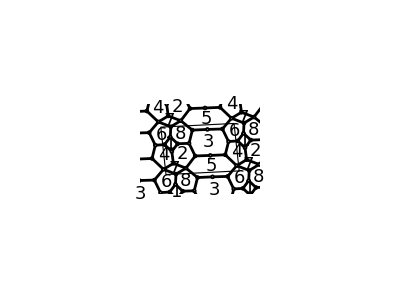

```mathematica
BraneTilingGraph[WPdP5PhaseCInt2Def/.ν->0]
```

```mathematica
WPdP5PhaseCInt2Def
```

X_1[3,5]·X_1[5,3]+X_2[3,5]·X_2[5,3]+X_1[1,4]·X_1[4,2]·X_1[2,1]-X_1[1,4]·X_1[4,6]·X_1[6,1]-X_1[1,8]·X_1[8,2]·X_1[2,1]+X_1[1,8]·X_1[8,6]·X_1[6,1]-X_1[2,3]·X_1[3,5]·X_1[5,2]+X_1[2,3]·X_1[3,8]·X_1[8,2]-X_1[2,7]·X_1[7,4]·X_1[4,2]+ν (X_1[3,5]·X_2[5,3]-X_1[2,7]·X_1[7,8]·X_1[8,2])-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,8]·X_1[8,5]·X_2[5,3]-X_1[5,6]·X_1[6,3]·X_2[3,5]-X_1[6,7]·X_1[7,8]·X_1[8,6]+X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]+X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]

```mathematica
WPdP5PhaseCInt2DefMin=WPdP5PhaseCInt2Def/.First@Solve[0==DG[WPdP5PhaseCInt2Def,{{Subscript[X, 1][3,5],Subscript[X, 2][5,3]}}],{Subscript[X, 1][3,5],Subscript[X, 2][5,3]}]//ExpandAll//Simplify
```

-(X_1[5,3]·X_2[3,5])/ν+X_1[1,4]·X_1[4,2]·X_1[2,1]-X_1[1,4]·X_1[4,6]·X_1[6,1]-X_1[1,8]·X_1[8,2]·X_1[2,1]+X_1[1,8]·X_1[8,6]·X_1[6,1]+X_1[2,3]·X_1[3,8]·X_1[8,2]+(X_1[2,3]·X_2[3,5]·X_1[5,2])/ν-X_1[2,7]·X_1[7,4]·X_1[4,2]-ν X_1[2,7]·X_1[7,8]·X_1[8,2]-X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,4]·X_1[4,6]·X_1[6,3]+(X_1[3,8]·X_1[8,5]·X_1[5,3])/ν-X_1[5,6]·X_1[6,3]·X_2[3,5]-X_1[6,7]·X_1[7,8]·X_1[8,6]-(X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2])/ν+X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]+X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]

{<|1→5,4→2,7→6,8→3,2→1,3→4,6→8,5→7|>,<|1→5,4→2,7→6,8→3,2→1,3→8,6→4,5→7|>,<|1→5,4→2,7→6,8→3,2→7,3→4,6→8,5→1|>,<|1→5,4→2,7→6,8→3,2→7,3→8,6→4,5→1|>,<|1→5,4→6,7→2,8→3,2→1,3→4,6→8,5→7|>,<|1→5,4→6,7→2,8→3,2→1,3→8,6→4,5→7|>,<|1→5,4→6,7→2,8→3,2→7,3→4,6→8,5→1|>,<|1→5,4→6,7→2,8→3,2→7,3→8,6→4,5→1|>}

```mathematica
WL131Z2PhaseBDefLen6//FieldProducts//Map[Length]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4}

```mathematica
WPdP5PhaseCInt2DefMin//FieldProducts//Map[Length]
```

{2,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4}

```mathematica
AssociationMap[Coefficient[WPdP5PhaseCInt2DefMin,#]&,FieldProducts@WPdP5PhaseCInt2DefMin]
```

<|X_1[5,3]·X_2[3,5]→-1/ν,X_1[1,4]·X_1[4,2]·X_1[2,1]→1,X_1[1,4]·X_1[4,6]·X_1[6,1]→-1,X_1[1,8]·X_1[8,2]·X_1[2,1]→-1,X_1[1,8]·X_1[8,6]·X_1[6,1]→1,X_1[2,3]·X_1[3,8]·X_1[8,2]→1,X_1[2,3]·X_2[3,5]·X_1[5,2]→1/ν,X_1[2,7]·X_1[7,4]·X_1[4,2]→-1,X_1[2,7]·X_1[7,8]·X_1[8,2]→-ν,X_1[3,4]·X_1[4,5]·X_1[5,3]→-1,X_1[3,4]·X_1[4,6]·X_1[6,3]→1,X_1[3,8]·X_1[8,5]·X_1[5,3]→1/ν,X_1[5,6]·X_1[6,3]·X_2[3,5]→-1,X_1[6,7]·X_1[7,8]·X_1[8,6]→-1,X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2]→-1/ν,X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]→1,X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]→1|>

```mathematica
WPdP5PhaseCInt2DefMin/.FieldRedefinition[FieldCases@WPdP5PhaseCInt2DefMin,QuiverFromFields@WPdP5PhaseCInt2DefMin,3]//FullSimplify//Collect[#,c_CenterDot,Simplify]&;
CoefMap2=AssociationMap[Coefficient[%,#]&,FieldProducts@%];
```

```mathematica
isom=FindGraphIsomorphism[
Values@QuiverFromFields@WL131Z2PhaseBDefLen6,
Values@QuiverFromFields@WPdP5PhaseCInt2DefMin,
All
];
```

```mathematica
WL131Z2PhaseBDefLen6/.ChangeGroupIndices[Normal@isom[[1]]]
```

X_1[1,4]·X_1[4,2]·X_1[2,1]-X_1[1,8]·X_1[8,2]·X_1[2,1]+X_1[1,8]·X_1[8,6]·X_1[6,1]+X_1[2,3]·X_1[3,8]·X_1[8,2]+μ (-(X_1[1,4]·X_1[4,6]·X_1[6,1])+X_1[2,7]·X_1[7,8]·X_1[8,2])-X_1[4,2]·X_1[2,7]·X_1[7,4]-X_1[4,6]·X_1[6,3]·X_1[3,4]+X_1[4,6]·X_1[6,7]·X_1[7,4]-X_1[5,2]·X_1[2,3]·X_1[3,5]+X_1[5,3]·X_1[3,4]·X_1[4,5]-X_1[5,3]·X_1[3,8]·X_1[8,5]+X_1[5,6]·X_1[6,3]·X_1[3,5]-X_1[7,8]·X_1[8,6]·X_1[6,7]+X_1[5,2]·X_1[2,7]·X_1[7,8]·X_1[8,5]-X_1[5,6]·X_1[6,1]·X_1[1,4]·X_1[4,5]

```mathematica
CoefMap2
```

<|X_1[1,4]·X_1[4,2]·X_1[2,1]→α_1[4,2],X_1[2,7]·X_1[7,4]·X_1[4,2]→-α_1[4,2],X_1[1,4]·X_1[4,6]·X_1[6,1]→-α_1[4,6],X_1[3,4]·X_1[4,6]·X_1[6,3]→α_1[4,6],X_1[3,4]·X_1[4,5]·X_1[5,3]→-(α_1[5,3] (ν α_1[4,5]+δ_2[3,5]))/ν,X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]→α_1[4,5] α_1[5,6],X_1[1,8]·X_1[8,2]·X_1[2,1]→-α_1[8,2],X_1[2,3]·X_1[3,8]·X_1[8,2]→α_1[8,2],X_1[2,7]·X_1[7,8]·X_1[8,2]→-ν α_1[8,2],X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2]→(ν β_1[8,2]+γ_1[5,3] (α_1[8,5]-γ_2[3,5])+α_1[5,2] (-α_1[8,5]+γ_2[3,5]))/ν,X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]→α_1[5,2] α_1[8,5]-ν β_1[8,2],X_1[3,8]·X_1[8,5]·X_1[5,3]→(α_1[5,3] (α_1[8,5]-γ_2[3,5]))/ν,X_1[1,8]·X_1[8,6]·X_1[6,1]→α_1[8,6],X_1[6,7]·X_1[7,8]·X_1[8,6]→-α_1[8,6],X_1[2,3]·X_2[3,5]·X_1[5,2]→(α_2[3,5] (α_1[5,2]-γ_1[5,3]))/ν,X_1[5,3]·X_2[3,5]→-(α_1[5,3] α_2[3,5])/ν,X_1[5,6]·X_1[6,3]·X_2[3,5]→-(α_2[3,5] (ν α_1[5,6]+β_1[5,3]))/ν,X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]→β_1[4,2],X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2]→-β_1[4,2],X_1[3,4]·X_1[4,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]→-α_1[5,3] β_1[4,5]-β_2[3,5] γ_1[5,6],X_1[3,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]·X_1[4,6]·X_1[6,3]→α_1[5,6] β_1[4,5],X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→-β_1[4,6],X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,3]→β_1[4,6]-α_1[4,5] β_1[5,3]-((ν α_1[5,6]+β_1[5,3]) δ_2[3,5])/ν,X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→(β_1[5,2] (-α_1[8,5]+γ_2[3,5]))/ν,X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→α_1[8,5] β_1[5,2],X_1[2,3]·X_2[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→(α_2[3,5] β_1[5,2])/ν,X_1[3,8]·X_1[8,5]·X_1[5,6]·X_1[6,3]→(α_1[8,5] β_1[5,3]-(ν α_1[5,6]+β_1[5,3]) γ_2[3,5])/ν,X_1[3,4]·X_1[4,6]·X_1[6,3]·X_1[3,5]·X_1[5,6]·X_1[6,3]→-β_1[4,5] β_1[5,3],X_1[3,8]·X_1[8,6]·X_1[6,7]·X_1[7,4]·X_1[4,5]·X_1[5,3]→α_1[4,5] β_1[5,6],X_1[3,8]·X_1[8,6]·X_1[6,3]·X_2[3,5]·X_1[5,3]→-α_2[3,5] β_1[5,6],X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,6]·X_1[6,7]·X_1[7,4]·X_1[4,6]·X_1[6,3]→β_1[4,5] β_1[5,6],X_1[1,8]·X_1[8,5]·X_1[5,2]·X_1[2,1]→-β_1[8,2],X_1[2,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,2]→(β_1[8,5] (-α_1[5,2]+γ_1[5,3]))/ν,X_1[2,7]·X_1[7,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,2]→α_1[5,2] β_1[8,5],X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]→(α_1[5,3] β_1[8,5])/ν-β_1[5,6] β_2[3,5],X_1[2,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→-(β_1[5,2] β_1[8,5])/ν,X_1[2,7]·X_1[7,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→β_1[5,2] β_1[8,5],X_1[3,5]·X_1[5,6]·X_1[6,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]→(β_1[5,3] β_1[8,5])/ν,X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1]→β_1[8,6],X_1[5,6]·X_1[6,7]·X_1[7,8]·X_1[8,5]→-β_1[8,6],X_1[2,3]·X_1[3,5]·X_1[5,2]→(β_2[3,5] (α_1[5,2]-γ_1[5,3]))/ν,X_1[3,5]·X_1[5,3]→-(α_1[5,3] β_2[3,5])/ν,X_1[3,5]·X_1[5,6]·X_1[6,3]→-((ν α_1[5,6]+β_1[5,3]) β_2[3,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→(β_1[5,2] β_2[3,5]+α_1[5,3] γ_1[8,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→-α_1[5,3] γ_1[4,5]+(β_2[3,5] γ_1[5,2])/ν,X_1[2,3]·X_1[3,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]·X_1[4,2]→α_1[5,6] γ_1[4,5],X_1[2,3]·X_1[3,5]·X_1[5,6]·X_1[6,3]·X_1[3,4]·X_1[4,2]→-β_1[5,3] γ_1[4,5],X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,6]·X_1[6,7]·X_1[7,4]·X_1[4,2]→β_1[5,6] γ_1[4,5],X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→(γ_1[5,2] (-α_1[8,5]+γ_2[3,5]))/ν,X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→α_1[8,5] γ_1[5,2],X_1[2,3]·X_2[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→(α_2[3,5] γ_1[5,2])/ν,X_1[2,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→-(β_1[8,5] γ_1[5,2])/ν,X_1[2,7]·X_1[7,8]·X_1[8,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→β_1[8,5] γ_1[5,2],X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2]→-(ν α_1[4,5] γ_1[5,3]+(-α_1[5,2]+γ_1[5,3]) δ_2[3,5])/ν,X_1[2,3]·X_1[3,4]·X_1[4,6]·X_1[6,3]·X_1[3,5]·X_1[5,2]→-β_1[4,5] γ_1[5,3],X_1[2,3]·X_1[3,5]·X_1[5,2]·X_1[2,3]·X_1[3,4]·X_1[4,2]→-γ_1[4,5] γ_1[5,3],X_1[3,4]·X_1[4,6]·X_1[6,7]·X_1[7,4]·X_1[4,5]·X_1[5,3]→α_1[4,5] γ_1[5,6],X_1[3,4]·X_1[4,6]·X_1[6,3]·X_2[3,5]·X_1[5,3]→-α_2[3,5] γ_1[5,6],X_1[3,4]·X_1[4,6]·X_1[6,7]·X_1[7,4]·X_1[4,6]·X_1[6,3]·X_1[3,5]·X_1[5,3]→β_1[4,5] γ_1[5,6],X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,6]·X_1[6,7]·X_1[7,4]·X_1[4,2]→γ_1[4,5] γ_1[5,6],X_1[2,3]·X_1[3,5]·X_1[5,2]·X_1[2,7]·X_1[7,8]·X_1[8,2]→α_1[5,2] γ_1[8,5],X_1[2,3]·X_1[3,8]·X_1[8,2]·X_1[2,3]·X_1[3,5]·X_1[5,2]→-(α_1[5,2] γ_1[8,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]·X_1[2,7]·X_1[7,8]·X_1[8,2]→β_1[5,2] γ_1[8,5],X_1[2,3]·X_1[3,8]·X_1[8,2]·X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→-(β_1[5,2] γ_1[8,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,6]·X_1[6,3]·X_1[3,8]·X_1[8,2]→(β_1[5,3] γ_1[8,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,7]·X_1[7,8]·X_1[8,2]→γ_1[5,2] γ_1[8,5],X_1[2,3]·X_1[3,8]·X_1[8,2]·X_1[2,3]·X_1[3,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→-(γ_1[5,2] γ_1[8,5])/ν,X_1[2,3]·X_1[3,5]·X_1[5,2]·X_1[2,3]·X_1[3,8]·X_1[8,2]→(γ_1[5,3] γ_1[8,5])/ν,X_1[3,8]·X_1[8,6]·X_1[6,3]·X_1[3,8]·X_1[8,5]·X_1[5,3]→-β_1[5,6] γ_2[3,5],X_1[3,4]·X_1[4,6]·X_1[6,3]·X_1[3,8]·X_1[8,5]·X_1[5,3]→-γ_1[5,6] γ_2[3,5],X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,3]·X_1[3,8]·X_1[8,2]→(β_1[5,2] δ_2[3,5])/ν,X_1[3,4]·X_1[4,5]·X_1[5,3]·X_1[3,8]·X_1[8,6]·X_1[6,3]→-β_1[5,6] δ_2[3,5],X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→(γ_1[5,2] δ_2[3,5])/ν,X_1[3,4]·X_1[4,6]·X_1[6,3]·X_1[3,4]·X_1[4,5]·X_1[5,3]→-γ_1[5,6] δ_2[3,5]|>

```mathematica
Block[{isom,ws,sols},
isom=FindGraphIsomorphism[
Values@QuiverFromFields@WL131Z2PhaseBDefLen6,
Values@QuiverFromFields@WPdP5PhaseCInt2DefMin,
All
];
ws=Map[
Simplify[WL131Z2PhaseBDefLen6/.ChangeGroupIndices[#]]&,
Normal/@isom
];
sols=Map[
w↦First@Select[FreeQ[λ->0]]@Solve[Equal@@@Values@Select[Length[#]==2&]@Merge[
{CoefMap2,AssociationMap[ Coefficient[w,#]&,FieldProducts@w]},
Identity
]],
ws
];
MapThread[(#1-Total@KeyValueMap[Times]@CoefMap2)/.#2&,{ws,sols}]//Simplify
]
```

## Mesonic Branch

### Model 2: ℂ^3/ℤ_4×ℤ_2 (1,0,3)(0,1,1)

```mathematica
C3Z4Z2FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WC3Z4Z2,5];
```

```mathematica
C3Z4Z2FieldGenRules=ReduceGenerators[WC3Z4Z2,Keys@C3Z4Z2FieldGenRules0,C3Z4Z2FieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
C3Z4Z2FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[6,5]·X_1[5,6]→A[1]
X_1[7,8]·X_1[8,7]→A[2]
X_1[4,3]·X_1[3,4]→A[3]
X_1[1,2]·X_1[2,1]→A[4]
X_1[8,6]·X_1[6,5]·X_1[5,8]→B[5]
X_1[3,6]·X_1[6,5]·X_1[5,3]→B[5]
X_1[7,5]·X_1[5,6]·X_1[6,7]→B[5]
X_1[7,5]·X_1[5,8]·X_1[8,7]→B[5]
X_1[7,8]·X_1[8,6]·X_1[6,7]→B[5]
X_1[4,5]·X_1[5,6]·X_1[6,4]→B[5]
X_1[4,5]·X_1[5,3]·X_1[3,4]→B[5]
X_1[4,3]·X_1[3,6]·X_1[6,4]→B[5]
X_1[2,8]·X_1[8,7]·X_1[7,2]→B[5]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[5]
X_1[1,7]·X_1[7,8]·X_1[8,1]→B[5]
X_1[1,7]·X_1[7,2]·X_1[2,1]→B[5]
X_1[1,4]·X_1[4,3]·X_1[3,1]→B[5]
X_1[1,4]·X_1[4,2]·X_1[2,1]→B[5]
X_1[1,2]·X_1[2,8]·X_1[8,1]→B[5]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[5]
X_1[7,5]·X_1[5,8]·X_1[8,6]·X_1[6,7]→C[1]
X_1[7,5]·X_1[5,3]·X_1[3,6]·X_1[6,7]→C[1]
X_1[4,5]·X_1[5,8]·X_1[8,6]·X_1[6,4]→C[1]
X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4]→C[1]
X_1[2,8]·X_1[8,6]·X_1[6,7]·X_1[7,2]→C[1]
X_1[2,8]·X_1[8,6]·X_1[6,4]·X_1[4,2]→C[6]
X_1[2,3]·X_1[3,6]·X_1[6,7]·X_1[7,2]→C[7]
X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→C[1]
X_1[1,7]·X_1[7,5]·X_1[5,8]·X_1[8,1]→C[1]
X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→C[10]
X_1[1,7]·X_1[7,2]·X_1[2,8]·X_1[8,1]→C[1]
X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]→C[1]
X_1[1,4]·X_1[4,5]·X_1[5,8]·X_1[8,1]→C[13]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]→C[1]
X_1[1,4]·X_1[4,2]·X_1[2,8]·X_1[8,1]→C[1]
X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]→C[1]

```mathematica
C3Z4Z2FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WC3Z4Z2],Equal@@@C3Z4Z2FieldGenRules],FieldCases@WC3Z4Z2]
```

A[1] B[5]==A[2] B[5]&&A[3] B[5]==A[2] B[5]&&A[4] B[5]==A[2] B[5]&&A[1] C[1]==B[5]^2&&A[2] C[1]==B[5]^2&&A[3] C[1]==B[5]^2&&A[4] C[1]==B[5]^2&&A[1] C[6]==A[2] C[6]&&A[3] C[6]==A[2] C[6]&&A[4] C[6]==A[2] C[6]&&A[1] C[7]==A[2] C[13]&&A[2] C[7]==A[2] C[13]&&A[3] C[7]==A[2] C[13]&&A[4] C[7]==A[2] C[13]&&B[5] C[7]==B[5] C[13]&&C[1] C[7]==C[1] C[13]&&C[6] C[7]==C[1]^2&&A[1] C[10]==A[2] C[6]&&A[2] C[10]==A[2] C[6]&&A[3] C[10]==A[2] C[6]&&A[4] C[10]==A[2] C[6]&&B[5] C[10]==B[5] C[6]&&C[1] C[10]==C[1] C[6]&&C[7] C[10]==C[1]^2&&A[1] C[13]==A[2] C[13]&&A[3] C[13]==A[2] C[13]&&A[4] C[13]==A[2] C[13]&&C[6] C[13]==C[1]^2&&C[10] C[13]==C[1]^2

```mathematica
PrimaryDecompositionM2[C3Z4Z2FieldChiralIdeal,DeleteDuplicates@Values@C3Z4Z2FieldGenRules]
```

{{C[13],C[10],C[7],C[6],C[1],B[5]},{C[7]-C[13],C[6]-C[10],A[3]-A[4],A[2]-A[4],A[1]-A[4],C[1]^2-C[10] C[13],B[5]^2-A[4] C[1]},{C[13],C[7],C[1],B[5],A[4],A[3],A[2],A[1]},{C[10],C[6],C[1],B[5],A[4],A[3],A[2],A[1]}}

```mathematica
Echo@PrimaryDecompositionM2[C3Z4Z2FieldChiralIdeal,DeleteDuplicates@Values@C3Z4Z2FieldGenRules]//Map[x↦KrullDimensionM2[x,Sort@Variables@#],#]&
```

{{C[13],C[10],C[7],C[6],C[1],B[5]},{C[7]-C[13],C[6]-C[10],A[3]-A[4],A[2]-A[4],A[1]-A[4],C[1]^2-C[10] C[13],B[5]^2-A[4] C[1]},{C[13],C[7],C[1],B[5],A[4],A[3],A[2],A[1]},{C[10],C[6],C[1],B[5],A[4],A[3],A[2],A[1]}}

{4,3,2,2}

```mathematica
C3Z4Z2FieldMesonicIdeal=ToSubtractList@Eliminate[C[6]==C[10]&&C[7]==C[13]&&A[1]==A[2]==A[3]==A[4]&&C3Z4Z2FieldChiralIdeal,{A[2],A[3],A[4],C[13],C[10]}]
```

{-B[5]^2+A[1] C[1],-C[1]^2+C[6] C[7]}

```mathematica
sl=GroebnerBasis@C3Z4Z2FieldMesonicIdeal//SingularLocusM2[#,Sort@Variables@#]&//PrimaryDecompositionM2[#,Sort@Variables@#]&
```

{{C[7],C[6],C[1]^2,B[5] C[1],B[5]^2-A[1] C[1]},{C[7],C[1],B[5],A[1]},{C[6],C[1],B[5],A[1]}}

```mathematica
C3Z4Z2VersalQuadDeformation= Map[
Total@Select[MonomialList[#,Cases[t[_]]@Variables@#],EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]]&,
Flatten@Total@VersalDeformationsM2[C3Z4Z2FieldMesonicIdeal,Variables@C3Z4Z2FieldMesonicIdeal,{-8,7}][[2]]
]
```

{t[22] A[1]^2+t[44] A[1] B[5]+t[45] A[1] C[1]-C[1]^2+C[6] C[7],B[5]^2-A[1] C[1]-t[3] C[6]^2-t[12] C[7]^2}

### Model 3: L_(1,3,1)/ℤ_2 (0,1,1,1) Phase A

```mathematica
L131Z2FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WL131Z2PhaseA,4];
```

```mathematica
L131Z2FieldGenRules=ReduceGenerators[WL131Z2PhaseA,Keys@L131Z2FieldGenRules0,L131Z2FieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
L131Z2FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[7,3]·X_1[3,7]→A[1]
X_1[1,8]·X_1[8,1]→A[2]
X_1[7,5]·X_1[5,3]·X_1[3,7]→B[3]
X_1[7,3]·X_1[3,2]·X_1[2,7]→B[3]
X_1[7,8]·X_1[8,3]·X_1[3,7]→B[3]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[3]
X_1[1,8]·X_1[8,3]·X_1[3,1]→B[3]
X_1[1,7]·X_1[7,3]·X_1[3,1]→B[3]
X_1[1,7]·X_1[7,8]·X_1[8,1]→B[3]
X_1[1,4]·X_1[4,8]·X_1[8,1]→B[3]
X_1[7,5]·X_1[5,6]·X_1[6,2]·X_1[2,7]→B[3]
X_1[7,5]·X_1[5,3]·X_1[3,2]·X_1[2,7]→C[4]
X_1[7,8]·X_1[8,6]·X_1[6,2]·X_1[2,7]→C[3]
X_1[7,8]·X_1[8,3]·X_1[3,2]·X_1[2,7]→C[4]
X_1[4,5]·X_1[5,6]·X_1[6,2]·X_1[2,4]→C[5]
X_1[4,5]·X_1[5,3]·X_1[3,2]·X_1[2,4]→B[3]
X_1[4,8]·X_1[8,6]·X_1[6,2]·X_1[2,4]→B[3]
X_1[4,8]·X_1[8,3]·X_1[3,2]·X_1[2,4]→C[8]
X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]→C[9]
X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→C[4]
X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]→C[4]
X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]→C[4]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→B[3]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]→C[14]
X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1]→C[4]
X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]→C[4]

```mathematica
L131Z2FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WL131Z2PhaseA],Equal@@@L131Z2FieldGenRules],FieldCases@WL131Z2PhaseA]
```

A[1] B[3]==A[2] B[3]&&A[1] C[3]==A[2] C[3]&&A[1] C[4]==B[3]^2&&A[2] C[4]==B[3]^2&&B[3] C[5]==A[2] B[3]&&C[3] C[5]==A[2] C[3]&&C[4] C[5]==B[3]^2&&A[1] C[8]==A[2] C[8]&&C[3] C[8]==B[3] C[4]&&C[5] C[8]==A[2] C[8]&&A[1] C[9]==A[2] C[8]&&A[2] C[9]==A[2] C[8]&&B[3] C[9]==B[3] C[8]&&C[3] C[9]==B[3] C[4]&&C[4] C[9]==C[4] C[8]&&C[5] C[9]==A[2] C[8]&&A[1] C[14]==A[2] C[3]&&A[2] C[14]==A[2] C[3]&&B[3] C[14]==B[3] C[3]&&C[4] C[14]==C[3] C[4]&&C[5] C[14]==A[2] C[3]&&C[8] C[14]==B[3] C[4]&&C[9] C[14]==B[3] C[4]

```mathematica
L131Z2FieldMesonicIdeal=Most@ToSubtractList@Eliminate[C[8]==C[9]&&C[3]==C[14]&&A[1]==A[2]==C[5]&&L131Z2FieldChiralIdeal,{A[2],C[5],C[9],C[14]}]//FullSimplify
```

{-B[3]^2+A[1] C[4],B[3] C[4]-C[3] C[8]}

```mathematica
L131Z2VersalQuadDeformation= Map[
Total@Select[MonomialList[#,Cases[t[_]]@Variables@#],EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]]&,
Flatten@Total@VersalDeformationsM2[L131Z2FieldMesonicIdeal,Variables@L131Z2FieldMesonicIdeal,{-8,7}][[2]]
]
```

{t[22] A[1]^2+t[37] A[1] B[3]+B[3] C[4]-C[3] C[8],B[3]^2-t[3] C[3]^2-A[1] C[4]-t[12] C[8]^2}

```mathematica
{t[22] A[1]^2+t[37] A[1] B[3]+B[3] C[4]-C[3] C[8],B[3]^2-t[3] C[3]^2-A[1] C[4]-t[12] C[8]^2}/.{B[3]->u,C[4]->z4,C[3]->z1,C[8]->z3,A[1]->z2}//Column
```

-z1 z3+u z4+z2^2 t[22]+u z2 t[37]
u^2-z2 z4-z1^2 t[3]-z3^2 t[12]

### Model 3: L_(1,3,1)/ℤ_2 (0,1,1,1) Phase B

```mathematica
L131Z2BFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WL131Z2PhaseB,5];
```

```mathematica
L131Z2BFieldGenRules=ReduceGenerators[WL131Z2PhaseB,Keys@L131Z2BFieldGenRules0,L131Z2BFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
L131Z2BFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[1,8]·X_1[8,1]→A[1]
X_1[7,5]·X_1[5,6]·X_1[6,7]→B[1]
X_1[7,5]·X_1[5,3]·X_1[3,7]→B[1]
X_1[7,2]·X_1[2,6]·X_1[6,7]→B[1]
X_1[7,2]·X_1[2,3]·X_1[3,7]→B[4]
X_1[7,8]·X_1[8,6]·X_1[6,7]→B[5]
X_1[7,8]·X_1[8,3]·X_1[3,7]→B[1]
X_1[4,5]·X_1[5,6]·X_1[6,4]→B[7]
X_1[4,5]·X_1[5,3]·X_1[3,4]→B[1]
X_1[4,2]·X_1[2,6]·X_1[6,4]→B[1]
X_1[4,2]·X_1[2,3]·X_1[3,4]→B[1]
X_1[4,8]·X_1[8,6]·X_1[6,4]→B[1]
X_1[4,8]·X_1[8,3]·X_1[3,4]→B[12]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[1]
X_1[1,8]·X_1[8,3]·X_1[3,1]→B[1]
X_1[1,7]·X_1[7,8]·X_1[8,1]→B[1]
X_1[1,4]·X_1[4,8]·X_1[8,1]→B[1]
X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]→C[1]
X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→C[5]
X_1[1,7]·X_1[7,2]·X_1[2,6]·X_1[6,1]→C[1]
X_1[1,7]·X_1[7,2]·X_1[2,3]·X_1[3,1]→B[1]
X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]→C[5]
X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]→C[5]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→B[1]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]→C[8]
X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→C[5]
X_1[1,4]·X_1[4,2]·X_1[2,3]·X_1[3,1]→C[8]
X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1]→C[5]
X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]→C[5]

```mathematica
L131Z2BFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WL131Z2PhaseB],Equal@@@L131Z2BFieldGenRules],FieldCases@WL131Z2PhaseB]
```

B[1] B[4]==A[1] B[1]&&B[1] B[5]==B[1] C[8]&&B[4] B[5]==A[1] C[8]&&B[1] B[7]==A[1] B[1]&&B[5] B[7]==A[1] C[8]&&B[1] B[12]==B[1] C[1]&&B[4] B[12]==A[1] C[1]&&B[5] B[12]==B[1] C[5]&&B[7] B[12]==A[1] C[1]&&A[1] (B[12]-C[1])==0&&B[4] C[1]==A[1] C[1]&&B[5] C[1]==B[1] C[5]&&B[7] C[1]==A[1] C[1]&&A[1] C[5]==B[1]^2&&B[4] C[5]==B[1]^2&&B[5] C[5]==C[5] C[8]&&B[7] C[5]==B[1]^2&&B[12] C[5]==C[1] C[5]&&A[1] (B[5]-C[8])==0&&B[4] C[8]==A[1] C[8]&&B[7] C[8]==A[1] C[8]&&B[12] C[8]==B[1] C[5]&&C[1] C[8]==B[1] C[5]

```mathematica
Map[Union,GeneratorsLattice[WL131Z2PhaseB]/.L131Z2BFieldGenRules]
```

<|{1,0}→{A[1],B[4],B[7]},{-1,-1}→{B[5],C[8]},{0,0}→{B[1]},{0,1}→{B[12],C[1]},{-1,0}→{C[5]}|>

```mathematica
PrimaryDecompositionM2[L131Z2BFieldChiralIdeal,Variables@ToSubtractList@L131Z2BFieldChiralIdeal]//Column
```

{C[8],C[5],C[1],B[12],B[5],B[1]}
{B[12]-C[1],B[5]-C[8],B[4]-B[7],A[1]-B[7],B[1] C[5]-C[1] C[8],B[1]^2-B[7] C[5]}
{C[8],C[5],B[7],B[5],B[4],B[1],A[1]}
{C[5],C[1],B[12],B[7],B[4],B[1],A[1]}

```mathematica
L131Z2BFieldMesonicIdeal=Eliminate[B[12]==C[1]&&B[5]==C[8]&&B[4]==B[7]&&A[1]==B[7]&&L131Z2BFieldChiralIdeal,{B[4],B[12],B[5],A[1]}]//FullSimplify
```

B[1] C[5]==C[1] C[8]&&B[1]^2==B[7] C[5]

### Model 4: PdP_5 Phase A

```mathematica
PdP5FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP5PhaseA,4];
```

```mathematica
PdP5FieldGenRules=ReduceGenerators[WPdP5PhaseA,Keys@PdP5FieldGenRules0,PdP5FieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP5FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[6,7]·X_1[7,8]·X_1[8,5]·X_1[5,6]→C[1]
X_1[6,7]·X_1[7,4]·X_1[4,5]·X_1[5,6]→C[2]
X_1[6,3]·X_1[3,8]·X_1[8,5]·X_1[5,6]→C[2]
X_1[6,3]·X_1[3,4]·X_1[4,5]·X_1[5,6]→C[4]
X_1[2,7]·X_1[7,8]·X_1[8,5]·X_1[5,2]→C[2]
X_1[2,7]·X_1[7,4]·X_1[4,5]·X_1[5,2]→C[6]
X_1[2,3]·X_1[3,8]·X_1[8,5]·X_1[5,2]→C[7]
X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,2]→C[2]
X_1[1,6]·X_1[6,7]·X_1[7,8]·X_1[8,1]→C[2]
X_1[1,6]·X_1[6,7]·X_1[7,4]·X_1[4,1]→C[10]
X_1[1,6]·X_1[6,3]·X_1[3,8]·X_1[8,1]→C[11]
X_1[1,6]·X_1[6,3]·X_1[3,4]·X_1[4,1]→C[2]
X_1[1,2]·X_1[2,7]·X_1[7,8]·X_1[8,1]→C[13]
X_1[1,2]·X_1[2,7]·X_1[7,4]·X_1[4,1]→C[2]
X_1[1,2]·X_1[2,3]·X_1[3,8]·X_1[8,1]→C[2]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[16]

```mathematica
PdP5FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP5PhaseA],Equal@@@PdP5FieldGenRules],FieldCases@WPdP5PhaseA]
```

C[1] C[4]==C[1] C[13]&&C[2] C[4]==C[2] C[13]&&C[1] C[6]==C[2]^2&&C[2] C[6]==C[2] C[11]&&C[4] C[6]==C[11] C[13]&&C[4] C[7]==C[2]^2&&C[6] C[7]==C[7] C[11]&&C[1] C[10]==C[1] C[7]&&C[2] C[10]==C[2] C[7]&&C[4] C[10]==C[2]^2&&C[6] C[10]==C[7] C[11]&&C[1] C[11]==C[2]^2&&C[4] C[11]==C[11] C[13]&&C[10] C[11]==C[7] C[11]&&C[6] C[13]==C[11] C[13]&&C[7] C[13]==C[2]^2&&C[10] C[13]==C[2]^2&&C[2] C[16]==C[1] C[2]&&C[4] C[16]==C[1] C[13]&&C[6] C[16]==C[2]^2&&C[7] C[16]==C[1] C[7]&&C[10] C[16]==C[1] C[7]&&C[11] C[16]==C[2]^2&&C[13] C[16]==C[1] C[13]

```mathematica
PdP5FieldMesonicIdeal=Eliminate[0==First@PrimaryDecompositionM2[PdP5FieldChiralIdeal,DeleteDuplicates@Values@PdP5FieldGenRules],{C[10],C[11],C[13],C[16]}]
```

C[1] C[6]==C[2]^2&&C[4] C[7]==C[2]^2

### Model 4: PdP_5 Phase B

```mathematica
PdP5BFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP5PhaseB,4];
```

```mathematica
PdP5BFieldGenRules=ReduceGenerators[WPdP5PhaseB,Keys@PdP5BFieldGenRules0,PdP5BFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP5BFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[8,2]·X_1[2,8]→A[1]
X_1[4,6]·X_1[6,4]→A[2]
X_1[8,7]·X_1[7,2]·X_1[2,8]→B[4]
X_1[8,5]·X_1[5,2]·X_1[2,8]→B[4]
X_1[8,2]·X_1[2,3]·X_1[3,8]→B[4]
X_1[4,7]·X_1[7,6]·X_1[6,4]→B[4]
X_1[4,6]·X_1[6,3]·X_1[3,4]→B[4]
X_1[4,5]·X_1[5,6]·X_1[6,4]→B[4]
X_1[1,8]·X_1[8,2]·X_1[2,1]→B[4]
X_1[1,4]·X_1[4,6]·X_1[6,1]→B[4]
X_1[8,7]·X_1[7,6]·X_1[6,3]·X_1[3,8]→C[1]
X_1[8,7]·X_1[7,2]·X_1[2,3]·X_1[3,8]→C[2]
X_1[8,5]·X_1[5,6]·X_1[6,3]·X_1[3,8]→B[4]
X_1[8,5]·X_1[5,2]·X_1[2,3]·X_1[3,8]→C[2]
X_1[4,7]·X_1[7,6]·X_1[6,3]·X_1[3,4]→C[5]
X_1[4,7]·X_1[7,2]·X_1[2,3]·X_1[3,4]→C[6]
X_1[4,5]·X_1[5,6]·X_1[6,3]·X_1[3,4]→C[5]
X_1[4,5]·X_1[5,2]·X_1[2,3]·X_1[3,4]→B[4]
X_1[1,8]·X_1[8,7]·X_1[7,6]·X_1[6,1]→B[4]
X_1[1,8]·X_1[8,7]·X_1[7,2]·X_1[2,1]→C[2]
X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1]→C[11]
X_1[1,8]·X_1[8,5]·X_1[5,2]·X_1[2,1]→C[2]
X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1]→C[5]
X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,1]→B[4]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→C[5]
X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]→C[16]

```mathematica
PdP5BFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP5PhaseB],Equal@@@PdP5BFieldGenRules],FieldCases@WPdP5PhaseB]
```

A[1] B[4]==B[4] C[5]&&A[2] B[4]==B[4] C[2]&&A[1] C[1]==C[1] C[5]&&A[2] C[1]==C[1] C[2]&&A[1] C[2]==B[4]^2&&A[2] C[5]==B[4]^2&&C[2] C[5]==B[4]^2&&A[1] C[6]==C[5] C[11]&&A[2] C[6]==C[2] C[11]&&B[4] C[6]==B[4] C[11]&&C[1] C[6]==B[4]^2&&C[2] C[6]==C[2] C[11]&&C[5] C[6]==C[5] C[11]&&A[1] C[11]==C[5] C[11]&&A[2] C[11]==C[2] C[11]&&C[1] C[11]==B[4]^2&&A[1] C[16]==C[1] C[5]&&A[2] C[16]==C[1] C[2]&&B[4] C[16]==B[4] C[1]&&C[2] C[16]==C[1] C[2]&&C[5] C[16]==C[1] C[5]&&C[6] C[16]==B[4]^2&&C[11] C[16]==B[4]^2

```mathematica
Map[Union,GeneratorsLattice[WPdP5PhaseB]/.PdP5BFieldGenRules]
```

<|{0,-1}→{C[1],C[16]},{-1,0}→{A[2],C[2]},{1,0}→{A[1],C[5]},{0,1}→{C[6],C[11]},{0,0}→{B[4]}|>

```mathematica
PrimaryDecompositionM2[PdP5BFieldChiralIdeal,UniqueCases[PdP5BFieldChiralIdeal,$GeneratorVars[_]]]//Column
```

{C[6]-C[11],C[1]-C[16],A[2]-C[2],A[1]-C[5],C[2] C[5]-C[11] C[16],B[4]^2-C[11] C[16]}
{C[16],C[11],C[6],C[1],C[2],A[2],B[4]}
{C[16],C[11],C[6],C[1],C[2],C[5],B[4]}
{C[16],C[11],C[6],C[1],C[5],B[4],A[1]}
{C[16],C[1],C[2],A[2],C[5],B[4],A[1]}
{C[11],C[6],C[2],A[2],C[5],B[4],A[1]}

```mathematica
DeleteCases[DeleteDuplicates@Values@PdP5BFieldGenRules,Alternatives@@#]&/@PrimaryDecompositionM2[PdP5BFieldChiralIdeal,DeleteDuplicates@Values@PdP5BFieldGenRules]
```

{{A[1],A[2],B[4],C[1],C[2],C[5],C[6],C[11],C[16]},{A[1],A[2]},{A[2],C[2]},{A[1],C[5]},{C[6],C[11]},{C[1],C[16]}}

```mathematica
PdP5BFieldMesonicIdeal=Eliminate[0==First@PrimaryDecompositionM2[PdP5BFieldChiralIdeal,DeleteDuplicates@Values@PdP5BFieldGenRules],{A[1],A[2],C[1],C[6]}]
```

B[4]^2==C[11] C[16]&&C[2] C[5]==C[11] C[16]

### Model 4: PdP_5 Phase C

```mathematica
PdP5CFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP5PhaseC,5];
```

```mathematica
PdP5CFieldGenRules=ReduceGenerators[WPdP5PhaseC,Keys@PdP5CFieldGenRules0,PdP5CFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP5CFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[8,6]·X_1[6,7]·X_1[7,8]→B[1]
X_1[8,6]·X_1[6,3]·X_1[3,8]→B[2]
X_1[8,2]·X_1[2,7]·X_1[7,8]→B[3]
X_1[8,2]·X_1[2,3]·X_1[3,8]→B[1]
X_1[4,6]·X_1[6,7]·X_1[7,4]→B[5]
X_1[4,6]·X_1[6,3]·X_1[3,4]→B[1]
X_1[4,2]·X_1[2,7]·X_1[7,4]→B[1]
X_1[4,2]·X_1[2,3]·X_1[3,4]→B[8]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[1]
X_1[1,8]·X_1[8,2]·X_1[2,1]→B[1]
X_1[1,4]·X_1[4,6]·X_1[6,1]→B[1]
X_1[1,4]·X_1[4,2]·X_1[2,1]→B[1]
X_1[8,5]·X_1[5,6]·X_1[6,7]·X_1[7,8]→C[1]
X_1[8,5]·X_1[5,6]·X_1[6,3]·X_1[3,8]→B[1]
X_1[8,5]·X_1[5,2]·X_1[2,7]·X_1[7,8]→B[1]
X_1[8,5]·X_1[5,2]·X_1[2,3]·X_1[3,8]→C[4]
X_1[4,5]·X_1[5,6]·X_1[6,7]·X_1[7,4]→B[1]
X_1[4,5]·X_1[5,6]·X_1[6,3]·X_1[3,4]→C[6]
X_1[4,5]·X_1[5,2]·X_1[2,7]·X_1[7,4]→C[7]
X_1[4,5]·X_1[5,2]·X_1[2,3]·X_1[3,4]→B[1]
X_1[1,8]·X_1[8,5]·X_1[5,6]·X_1[6,1]→C[1]
X_1[1,8]·X_1[8,5]·X_1[5,2]·X_1[2,1]→C[4]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→C[6]
X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]→C[7]

```mathematica
PdP5CFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP5PhaseC],Equal@@@PdP5CFieldGenRules],FieldCases@WPdP5PhaseC]
```

B[1] B[2]==B[1] C[7]&&B[1] B[3]==B[1] C[6]&&B[2] B[3]==C[6] C[7]&&B[1] B[5]==B[1] C[4]&&B[2] B[5]==C[4] C[7]&&B[3] B[5]==B[1]^2&&B[1] B[8]==B[1] C[1]&&B[2] B[8]==B[1]^2&&B[3] B[8]==C[1] C[6]&&B[5] B[8]==C[1] C[4]&&B[2] C[1]==B[1]^2&&B[3] C[1]==C[1] C[6]&&B[5] C[1]==C[1] C[4]&&B[2] C[4]==C[4] C[7]&&B[3] C[4]==B[1]^2&&B[8] C[4]==C[1] C[4]&&B[2] C[6]==C[6] C[7]&&B[5] C[6]==B[1]^2&&B[8] C[6]==C[1] C[6]&&C[4] C[6]==B[1]^2&&B[3] C[7]==C[6] C[7]&&B[5] C[7]==C[4] C[7]&&B[8] C[7]==B[1]^2&&C[1] C[7]==B[1]^2

```mathematica
PrimaryDecompositionM2[PdP5CFieldChiralIdeal,UniqueCases[PdP5CFieldChiralIdeal,$GeneratorVars[_]]]
```

{{B[8]-C[1],B[5]-C[4],B[3]-C[6],B[2]-C[7],C[4] C[6]-C[1] C[7],B[1]^2-C[1] C[7]},{C[1],B[8],C[4],B[5],C[6],B[3],B[1]},{C[1],B[8],C[4],B[5],C[7],B[2],B[1]},{C[1],B[8],C[6],B[3],C[7],B[2],B[1]},{C[4],B[5],C[6],B[3],C[7],B[2],B[1]}}

```mathematica
DeleteCases[DeleteDuplicates@Values@PdP5CFieldGenRules,Alternatives@@#]&/@PrimaryDecompositionM2[PdP5CFieldChiralIdeal,DeleteDuplicates@Values@PdP5CFieldGenRules]
```

{{B[1],B[2],B[3],B[5],B[8],C[1],C[4],C[6],C[7]},{B[8],C[1]},{B[5],C[4]},{B[3],C[6]},{B[2],C[7]}}

```mathematica
PdP5CFieldMesonicIdeal=Eliminate[0==First@PrimaryDecompositionM2[PdP5CFieldChiralIdeal,DeleteDuplicates@Values@PdP5CFieldGenRules],{C[1],C[4],C[6],C[7]}]
```

B[3] B[5]==B[1]^2&&B[2] B[8]==B[1]^2

### Model 4: PdP_5 Phase D

```mathematica
PdP5DFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP5PhaseD,5];
```

```mathematica
PdP5DFieldGenRules=ReduceGenerators[WPdP5PhaseD,Keys@PdP5DFieldGenRules0,PdP5DFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP5DFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[8,6]·X_1[6,7]·X_1[7,8]→B[1]
X_2[8,6]·X_1[6,7]·X_1[7,8]→B[2]
X_1[8,6]·X_1[6,5]·X_1[5,8]→B[3]
X_2[8,6]·X_1[6,5]·X_1[5,8]→B[1]
X_1[8,6]·X_1[6,3]·X_1[3,8]→B[3]
X_2[8,6]·X_1[6,3]·X_1[3,8]→B[1]
X_1[8,2]·X_1[2,7]·X_1[7,8]→B[7]
X_2[8,2]·X_1[2,7]·X_1[7,8]→B[1]
X_1[8,2]·X_1[2,5]·X_1[5,8]→B[7]
X_2[8,2]·X_1[2,5]·X_1[5,8]→B[1]
X_1[8,2]·X_1[2,3]·X_1[3,8]→B[1]
X_2[8,2]·X_1[2,3]·X_1[3,8]→B[12]
X_1[4,6]·X_1[6,7]·X_1[7,4]→B[13]
X_2[4,6]·X_1[6,7]·X_1[7,4]→B[1]
X_1[4,6]·X_1[6,5]·X_1[5,4]→B[13]
X_2[4,6]·X_1[6,5]·X_1[5,4]→B[1]
X_1[4,6]·X_1[6,3]·X_1[3,4]→B[1]
X_2[4,6]·X_1[6,3]·X_1[3,4]→B[18]
X_1[4,2]·X_1[2,7]·X_1[7,4]→B[1]
X_2[4,2]·X_1[2,7]·X_1[7,4]→B[20]
X_1[4,2]·X_1[2,5]·X_1[5,4]→B[21]
X_2[4,2]·X_1[2,5]·X_1[5,4]→B[1]
X_1[4,2]·X_1[2,3]·X_1[3,4]→B[21]
X_2[4,2]·X_1[2,3]·X_1[3,4]→B[1]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[1]
X_1[1,8]·X_2[8,6]·X_1[6,1]→B[2]
X_1[1,8]·X_1[8,2]·X_1[2,1]→B[1]
X_1[1,8]·X_2[8,2]·X_1[2,1]→B[12]
X_1[1,4]·X_1[4,6]·X_1[6,1]→B[1]
X_1[1,4]·X_2[4,6]·X_1[6,1]→B[18]
X_1[1,4]·X_1[4,2]·X_1[2,1]→B[1]
X_1[1,4]·X_2[4,2]·X_1[2,1]→B[20]

```mathematica
PdP5DFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP5PhaseD],Equal@@@PdP5DFieldGenRules],FieldCases@WPdP5PhaseD]
```

B[1] B[3]==B[1] B[20]&&B[2] B[3]==B[1]^2&&B[1] B[7]==B[1] B[18]&&B[2] B[7]==B[2] B[18]&&B[3] B[7]==B[18] B[20]&&B[3] B[12]==B[12] B[20]&&B[7] B[12]==B[1]^2&&B[1] B[13]==B[1] B[12]&&B[2] B[13]==B[2] B[12]&&B[3] B[13]==B[12] B[20]&&B[7] B[13]==B[1]^2&&B[3] B[18]==B[18] B[20]&&B[12] B[18]==B[1]^2&&B[13] B[18]==B[1]^2&&B[2] B[20]==B[1]^2&&B[7] B[20]==B[18] B[20]&&B[13] B[20]==B[12] B[20]&&B[1] B[21]==B[1] B[2]&&B[3] B[21]==B[1]^2&&B[7] B[21]==B[2] B[18]&&B[12] B[21]==B[2] B[12]&&B[13] B[21]==B[2] B[12]&&B[18] B[21]==B[2] B[18]&&B[20] B[21]==B[1]^2

```mathematica
PrimaryDecompositionM2[PdP5DFieldChiralIdeal,UniqueCases[PdP5DFieldChiralIdeal,$GeneratorVars[_]]]
```

{{B[12]-B[13],B[7]-B[18],B[2]-B[21],B[3]-B[20],B[13] B[18]-B[20] B[21],B[1]^2-B[20] B[21]},{B[21],B[13],B[12],B[18],B[7],B[2],B[1]},{B[21],B[13],B[12],B[2],B[20],B[3],B[1]},{B[21],B[18],B[7],B[2],B[20],B[3],B[1]},{B[13],B[12],B[18],B[7],B[20],B[3],B[1]}}

```mathematica
DeleteCases[DeleteDuplicates@Values@PdP5DFieldGenRules,Alternatives@@#]&/@PrimaryDecompositionM2[PdP5DFieldChiralIdeal,DeleteDuplicates@Values@PdP5DFieldGenRules]
```

{{B[1],B[2],B[3],B[7],B[12],B[13],B[18],B[20],B[21]},{B[12],B[13]},{B[7],B[18]},{B[3],B[20]},{B[2],B[21]}}

```mathematica
PdP5DFieldMesonicIdeal=Eliminate[0==First@PrimaryDecompositionM2[PdP5DFieldChiralIdeal,DeleteDuplicates@Values@PdP5DFieldGenRules],{B[13],B[18],B[20],B[21]}]
```

B[2] B[3]==B[1]^2&&B[7] B[12]==B[1]^2

### ℂ^3/ℤ_4×ℤ_2 ⟹ L_(1,3,1)/ℤ_2 Phase A

#### Deformation 1: (1→2→1) - (3→4→3)

```mathematica
C3Z4Z2Def1FieldGenRules=ReduceGenerators[WC3Z4Z2Def1,Keys@C3Z4Z2FieldGenRules,C3Z4Z2FieldGenRules0,"RemoveDenominators"->True];
```

Keys::invrl: The argument C3Z4Z2FieldGenRules is not a valid Association or a list of rules.

{{1,0}→{A[1],A[2],A[3],A[4]},{0,0}→{B[5]},{-1,-1}→{C[7],C[13]},{-1,1}→{C[6],C[10]},{-1,0}→{C[1]}}

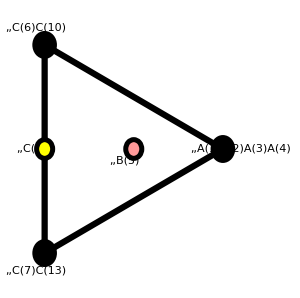

```mathematica
MapAt[DeleteDuplicates,ReplaceAll[C3Z4Z2FieldGenRules]@Normal@GeneratorsLattice[WC3Z4Z2],{All,2}]
PolytopePlot[Keys@%,"PolytopeCellLabel"->KeyValueMap[Point[#1]->Row[#2,","]&]@Association@%,ImageSize->300]
```

```mathematica
C3Z4Z2Def1ChiralIdeal=Eliminate[Abelianize@Join[Equal@@@C3Z4Z2Def1FieldGenRules,Thread[FTerms@WC3Z4Z2Def1==0]],FieldCases@WC3Z4Z2Def1]
```

A[1] B[5]==A[3] B[5]&&A[2] B[5]==A[3] B[5]&&A[1] C[1]==B[5]^2&&A[2] C[1]==B[5]^2&&A[3] C[1]==B[5]^2&&A[1] C[6]==A[3] C[6]&&(A[2]-A[3]) C[6]==0&&A[1] C[7]==A[3] C[13]&&A[2] C[7]==A[3] C[13]&&A[3] C[7]==A[3] C[13]&&B[5] C[7]==B[5] C[13]&&C[1] C[7]==C[1] C[13]&&C[6] C[7]==C[1] (m B[5]+C[1])&&A[1] C[10]==A[3] C[6]&&A[2] C[10]==A[3] C[6]&&A[3] C[10]==A[3] C[6]&&B[5] C[10]==B[5] C[6]&&C[1] C[10]==C[1] C[6]&&C[7] C[10]==C[1] (m B[5]+C[1])&&A[1] C[13]==A[3] C[13]&&(A[2]-A[3]) C[13]==0&&C[6] C[13]==C[1] (m B[5]+C[1])&&C[10] C[13]==C[1] (m B[5]+C[1])

```mathematica
PrimaryDecompositionM2[C3Z4Z2Def1ChiralIdeal,UniqueCases[C3Z4Z2Def1ChiralIdeal,$GeneratorVars[__]]]//Column
```

{C[10],C[13],C[7],C[6],C[1],B[5]}
{C[7]-C[13],C[6]-C[10],-A[2]+A[3],A[1]-A[2],B[5]^2-A[2] C[1],m B[5] C[1]+C[1]^2-C[10] C[13]}
{C[10],C[6],C[1],A[2],A[3],B[5],A[1]}
{C[13],C[7],C[1],A[2],A[3],B[5],A[1]}

```mathematica
C3Z4Z2Def1MesonicIdeal=Eliminate[C[7]==C[13]&&C[6]==C[10]&&A[2]==A[3]&&A[1]==A[2]&&C3Z4Z2Def1ChiralIdeal,{A[2],A[3],C[13],C[10]}]
C3Z4Z2Def1FieldMesGenRules=(C3Z4Z2Def1FieldGenRules//ReplaceAll[{A[2]->A[1],A[3]->A[1],A[4]->A[1],C[13]->C[7],C[10]->C[6]}]);
```

m B[5]^3==-B[5]^2 C[1]+A[1] C[6] C[7]&&A[1] C[1]==B[5]^2&&m B[5] C[1]==-C[1]^2+C[6] C[7]

```mathematica
Select[
GroebnerBasis[C3Z4Z2Def1MesonicIdeal/.{m->μ}/.Echo[GeneratorMassRedefinitions[WC3Z4Z2,{A[1],B[5],C[1],C[6],C[7]},{-1,0}]/. {β[2]->1,ε[3]->1,ε[2]->-1/2,β[1]->-1/4,ε[1]->1/16}],
{A[1],B[5],C[1],C[6],C[7]}
],
EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]
];
%/Map[Apply[GCD]@*First]@PolynomialReduce[%/.μ->0,ToSubtractList@C3Z4Z2Def1MesonicIdeal/.{m->0}]//ExpandAll
```

{B[5]→-1/4 μ A[1]+B[5],C[1]→1/16 μ^2 A[1]-1/2 μ B[5]+C[1]}

{-B[5]^2+A[1] C[1],3/256 μ^4 A[1]^2-1/8 μ^3 A[1] B[5]+3/8 μ^2 B[5]^2-C[1]^2+C[6] C[7]}

```mathematica
C3Z4Z2VersalQuadDeformation/.{t[3|12]->0,t[45]->3/8 μ^2,t[44]->-1/8 μ^2,t[22]->3/256 μ^4}
```

{3/256 μ^4 A[1]^2-1/8 μ^2 A[1] B[5]+3/8 μ^2 A[1] C[1]-C[1]^2+C[6] C[7],B[5]^2-A[1] C[1]}

### ℂ^3/ℤ_4×ℤ_2 ⟹ PdP_5 Phase A

#### Deformation 4 : (1→2→1) - (3→4→3) + (5→6→6) - (7→8→7)

```mathematica
C3Z4Z2Def4FieldGenRules=ReduceGenerators[WC3Z4Z2Def4,Keys@C3Z4Z2FieldGenRules,C3Z4Z2FieldGenRules0,"RemoveDenominators"->True];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
C3Z4Z2Def4ChiralIdeal=Eliminate[Abelianize@Join[Equal@@@C3Z4Z2Def4FieldGenRules,Thread[FTerms@WC3Z4Z2Def4==0]],FieldCases@WC3Z4Z2Def4]
```

m A[2] (-A[1]+A[3])==(-A[1]+A[3]) B[5]&&A[3] (m A[1]-B[5])==A[1] (m A[1]-B[5])&&A[2] B[5]==A[1] B[5]&&A[1] C[1]==B[5]^2&&A[2] C[1]==B[5]^2&&A[3] C[1]==B[5] (-m A[1]+m A[3]+B[5])&&(-A[1]+A[2]) C[6]==0&&(-A[1]+A[3]) C[6]==0&&A[1] C[7]==A[1] C[13]&&A[2] C[7]==A[1] C[13]&&A[3] C[7]==A[1] C[13]&&B[5] C[7]==B[5] C[13]&&C[1] C[7]==C[1] C[13]&&C[6] C[7]==m^2 B[5]^2-2 m B[5] C[1]+C[1]^2&&A[1] C[10]==A[1] C[6]&&A[2] C[10]==A[1] C[6]&&A[3] C[10]==A[1] C[6]&&B[5] C[10]==B[5] C[6]&&C[1] C[10]==C[1] C[6]&&C[7] C[10]==m^2 B[5]^2-2 m B[5] C[1]+C[1]^2&&(-A[1]+A[2]) C[13]==0&&(-A[1]+A[3]) C[13]==0&&C[6] C[13]==m^2 B[5]^2-2 m B[5] C[1]+C[1]^2&&C[10] C[13]==m^2 B[5]^2-2 m B[5] C[1]+C[1]^2

```mathematica
PrimaryDecompositionM2[C3Z4Z2Def4ChiralIdeal,UniqueCases[C3Z4Z2Def4ChiralIdeal,$GeneratorVars[_]]]
```

{{C[7]-C[13],C[6]-C[10],A[1]-A[3],A[2]-A[3],B[5]^2-A[3] C[1],m^2 A[3] C[1]-2 m B[5] C[1]+C[1]^2-C[10] C[13]},{m,C[10],C[13],C[7],C[6],C[1],B[5]},{C[10],C[13],C[7],C[6],C[1],B[5],A[1]-A[3]},{C[10],C[13],C[7],C[6],-A[1]+A[2],m B[5]-C[1],m A[1]-B[5],B[5]^2-A[1] C[1]},{C[10],C[6],C[1],B[5],A[3],A[1],A[2]},{C[13],C[7],C[1],B[5],A[3],A[1],A[2]}}

```mathematica
C3Z4Z2Def4MesonicIdeal=Eliminate[C[7]==C[13]&&C[6]==C[10]&&A[1]==A[3]&&A[2]==A[3]&&C3Z4Z2Def4ChiralIdeal,{A[2],A[3],C[10],C[13]}]
C3Z4Z2Def4FieldMesGenRules=(C3Z4Z2Def4FieldGenRules//ReplaceAll[{A[2]->A[1],A[3]->A[1],A[4]->A[1],C[13]->C[7],C[10]->C[6]}]);
```

A[1] C[1]==B[5]^2&&C[6] C[7]==m^2 B[5]^2-2 m B[5] C[1]+C[1]^2

```mathematica
Select[
GroebnerBasis[C3Z4Z2Def4MesonicIdeal/.{m->μ}/.Echo[GeneratorMassRedefinitions[WC3Z4Z2,{A[1],B[5],C[1],C[6],C[7]},{-1,0}]//. {β[2]->1,ε[3]->1,ε[1]->β[1]^2,ε[2]->2 β[1],β[1]->1/2}],
{A[1],B[5],C[1],C[6],C[7]}
],
EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]
];
%/Map[Apply[GCD]@*First]@PolynomialReduce[%/.μ->0,ToSubtractList@C3Z4Z2Def4MesonicIdeal/.{m->0}]//ExpandAll
```

{B[5]→1/2 μ A[1]+B[5],C[1]→1/4 μ^2 A[1]+μ B[5]+C[1]}

{-B[5]^2+A[1] C[1],1/16 μ^4 A[1]^2-1/2 μ^2 B[5]^2+C[1]^2-C[6] C[7]}

```mathematica
({-1,-1}Reverse@C3Z4Z2VersalQuadDeformation)/.{t[3|12]->0,t[22]->-1/16 μ^4,t[45]->1/2 μ^2,t[44]->0}
```

{-B[5]^2+A[1] C[1],1/16 μ^4 A[1]^2-1/2 μ^2 A[1] C[1]+C[1]^2-C[6] C[7]}

### ℂ^3/ℤ_4×ℤ_2 ⟹ PdP_5 Phase B

#### Deformation 5: (1→2→1) - (5→6→6)

```mathematica
C3Z4Z2Def5FieldGenRules=ReduceGenerators[WC3Z4Z2Def5,Keys@C3Z4Z2FieldGenRules,C3Z4Z2FieldGenRules0,"RemoveDenominators"->True];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
C3Z4Z2Def5ChiralIdeal=Eliminate[Abelianize@Join[Equal@@@C3Z4Z2Def5FieldGenRules,Thread[FTerms@WC3Z4Z2Def5==0]],FieldCases@WC3Z4Z2Def5]
```

A[2] B[5]==A[1] B[5]&&A[3] (m A[1]+B[5])==A[1] (m A[1]+B[5])&&A[1] C[1]==B[5]^2&&A[2] C[1]==B[5]^2&&A[3] (m B[5]+C[1])==B[5] (m A[1]+B[5])&&(-A[1]+A[2]) C[6]==0&&A[3] C[6]==A[1] C[6]&&A[1] C[7]==A[1] C[13]&&A[2] C[7]==A[1] C[13]&&A[3] C[7]==A[1] C[13]&&B[5] C[7]==B[5] C[13]&&C[1] C[7]==C[1] C[13]&&C[6] C[7]==m^2 B[5]^2+2 m B[5] C[1]+C[1]^2&&A[1] C[10]==A[1] C[6]&&A[2] C[10]==A[1] C[6]&&A[3] C[10]==A[1] C[6]&&B[5] C[10]==B[5] C[6]&&C[1] C[10]==C[1] C[6]&&C[7] C[10]==m^2 B[5]^2+2 m B[5] C[1]+C[1]^2&&(-A[1]+A[2]) C[13]==0&&A[3] C[13]==A[1] C[13]&&C[6] C[13]==m^2 B[5]^2+2 m B[5] C[1]+C[1]^2&&C[10] C[13]==m^2 B[5]^2+2 m B[5] C[1]+C[1]^2

```mathematica
C3Z4Z2Def5Tranform={A[2]->( A[2]-2 B[5]+1 C[1])/m^2,A[1]->(A[1]-2 B[5]+1 C[1])/m^2,A[3]->(A[3]+A[1]-2 B[5])/m^2,B[5]->(- C[1]+B[5])/m};
```

```mathematica
GroebnerBasis[C3Z4Z2Def5ChiralIdeal/.C3Z4Z2Def5Tranform]
PrimaryDecompositionM2[%,Variables@%]//Column
```

{C[7] C[10]-C[10] C[13],C[6] C[13]-C[10] C[13],C[6] C[7]-C[10] C[13],A[3] C[7]-A[3] C[13],A[3] C[6]-A[3] C[10],A[2] C[7]-A[2] C[13],A[2] C[6]-A[2] C[10],A[2] A[3] C[10]-C[10]^2 C[13],A[2] A[3] C[13]-C[10] C[13]^2,A[1] C[10]-A[2] C[10],A[1] C[13]-A[2] C[13],A[1] C[7]-A[2] C[13],A[1] C[6]-A[2] C[10],A[1] A[3]-C[10] C[13],-A[3] C[10]+C[1] C[10],-A[3] C[13]+C[1] C[13],C[1] C[7]-A[3] C[13],C[1] C[6]-A[3] C[10],A[2] C[1]-C[10] C[13],A[1] C[1]-C[10] C[13],B[5] C[7]-B[5] C[13],B[5] C[6]-B[5] C[10],A[2] A[3] B[5]-B[5] C[10] C[13],A[1] B[5]-A[2] B[5],-A[3] B[5]+B[5] C[1],B[5]^2-C[10] C[13]}

{C[7]-C[13],C[6]-C[10],A[3]-C[1],A[1]-A[2],A[2] C[1]-C[10] C[13],B[5]^2-C[10] C[13]}
{C[13],C[10],C[7],C[6],C[1],B[5],A[3]}
{C[13],C[10],C[7],C[6],C[1],B[5],A[1]}
{C[13],C[10],C[7],C[6],B[5],A[2],A[1]}
{C[13],C[7],C[1],B[5],A[3],A[2],A[1]}
{C[10],C[6],C[1],B[5],A[3],A[2],A[1]}

```mathematica
PrimaryDecompositionM2[PdP5BFieldChiralIdeal,UniqueCases[PdP5BFieldChiralIdeal,$GeneratorVars[_]]]//Column
```

{C[6]-C[11],C[1]-C[16],A[2]-C[2],A[1]-C[5],C[2] C[5]-C[11] C[16],B[4]^2-C[11] C[16]}
{C[16],C[11],C[6],C[1],C[2],A[2],B[4]}
{C[16],C[11],C[6],C[1],C[2],C[5],B[4]}
{C[16],C[11],C[6],C[1],C[5],B[4],A[1]}
{C[16],C[1],C[2],A[2],C[5],B[4],A[1]}
{C[11],C[6],C[2],A[2],C[5],B[4],A[1]}

```mathematica
C3Z4Z2Def5MesonicIdeal=Eliminate[C[7]==C[13]&&C[6]==C[10]&&A[1]==A[3]&&A[2]==A[3]&&C3Z4Z2Def5ChiralIdeal,{A[2],A[3],C[10],C[13]}]
C3Z4Z2Def5FieldMesGenRules=(C3Z4Z2Def5FieldGenRules//ReplaceAll[{A[2]->A[1],A[3]->A[1],A[4]->A[1],C[13]->C[7],C[10]->C[6]}]);
```

A[1] C[1]==B[5]^2&&C[6] C[7]==m^2 B[5]^2+2 m B[5] C[1]+C[1]^2

```mathematica
Select[
GroebnerBasis[C3Z4Z2Def5MesonicIdeal/.{m->-μ}/.GeneratorMassRedefinitions[WC3Z4Z2,{A[1],B[5],C[1],C[6],C[7]},{-1,0}]//. {β[2]->1,ε[3]->1,ε[1]->β[1]^2,ε[2]->2 β[1],β[1]->1/2},
{A[1],B[5],C[1],C[6],C[7]}
],
EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]
];
%/Map[Apply[GCD]@*First]@PolynomialReduce[%/.μ->0,ToSubtractList@C3Z4Z2Def5MesonicIdeal/.{m->0}]//ExpandAll
```

{-B[5]^2+A[1] C[1],1/16 μ^4 A[1]^2-1/2 μ^2 B[5]^2+C[1]^2-C[6] C[7]}

```mathematica
Reverse[-C3Z4Z2VersalQuadDeformation]/.{t[12|3]->0,t[22]->-1/16 μ^4,t[44]->0,t[45]->1/2 μ^2}
```

{-B[5]^2+A[1] C[1],1/16 μ^4 A[1]^2-1/2 μ^2 A[1] C[1]+C[1]^2-C[6] C[7]}

### L_(1,3,1)/ℤ_2 ⟹ Marginal deformation of PdP_5 (a)

#### Deformation 1: (1→8→1) - (3→7→3)

```mathematica
δWL131Z2PhaseADef1=m(Subscript[X, 1][1,8]·Subscript[X, 1][8,1]-Subscript[X, 1][3,7]·Subscript[X, 1][7,3]);
WL131Z2PhaseADef1=WL131Z2PhaseA+δWL131Z2PhaseADef1;
```

```mathematica
L131Z2Def1FieldGenRules=ReduceGenerators[WL131Z2PhaseADef1,Keys@L131Z2FieldGenRules,L131Z2FieldGenRules0,"RemoveDenominators"->True];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
L131Z2Def1FieldMesGenRules=(L131Z2Def1FieldGenRules//ReplaceAll[{C[5]->A[1],A[2]->A[1],C[14]->C[3],C[9]->C[8]}]);
GroupBy[L131Z2Def1FieldMesGenRules,Last->First]//KeyValueMap[List]//TableForm
```

A[1] | X_1[7,3]·X_1[3,7]
X_1[1,8]·X_1[8,1]
X_1[4,5]·X_1[5,6]·X_1[6,2]·X_1[2,4]
m A[1]+B[3] | X_1[7,5]·X_1[5,3]·X_1[3,7]
X_1[7,3]·X_1[3,2]·X_1[2,7]
X_1[1,8]·X_1[8,6]·X_1[6,1]
X_1[1,4]·X_1[4,8]·X_1[8,1]
X_1[7,5]·X_1[5,6]·X_1[6,2]·X_1[2,7]
X_1[4,5]·X_1[5,3]·X_1[3,2]·X_1[2,4]
X_1[4,8]·X_1[8,6]·X_1[6,2]·X_1[2,4]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]
B[3] | X_1[7,8]·X_1[8,3]·X_1[3,7]
X_1[1,8]·X_1[8,3]·X_1[3,1]
X_1[1,7]·X_1[7,3]·X_1[3,1]
X_1[1,7]·X_1[7,8]·X_1[8,1]
m^2 A[1]+m B[3]+C[4] | X_1[7,5]·X_1[5,3]·X_1[3,2]·X_1[2,7]
X_1[1,4]·X_1[4,8]·X_1[8,6]·X_1[6,1]
C[3] | X_1[7,8]·X_1[8,6]·X_1[6,2]·X_1[2,7]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]
C[4] | X_1[7,8]·X_1[8,3]·X_1[3,2]·X_1[2,7]
X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]
X_1[1,7]·X_1[7,8]·X_1[8,6]·X_1[6,1]
X_1[1,4]·X_1[4,8]·X_1[8,3]·X_1[3,1]
C[8] | X_1[4,8]·X_1[8,3]·X_1[3,2]·X_1[2,4]
X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]
-m B[3]+C[4] | X_1[1,7]·X_1[7,8]·X_1[8,3]·X_1[3,1]

```mathematica
Eliminate[Abelianize@Join[Equal@@@L131Z2Def1FieldGenRules,Thread[FTerms@WL131Z2PhaseADef1==0]],FieldCases@WL131Z2PhaseADef1]
Column@PrimaryDecompositionM2[ToSubtractList@%,Echo@UniqueCases[%,$GeneratorVars[_]]]
```

A[1] C[4]==B[3] (m A[1]+B[3])&&(m A[1]+B[3]) C[5]==A[1] (m A[1]+B[3])&&C[3] C[5]==A[1] C[3]&&C[4] C[5]==B[3] (m A[1]+B[3])&&C[3] C[8]==B[3] (m^2 A[1]+m B[3]+C[4])&&C[5] C[8]==A[1] C[8]&&A[1] C[9]==A[1] C[8]&&B[3] C[9]==B[3] C[8]&&C[3] C[9]==B[3] (m^2 A[1]+m B[3]+C[4])&&C[4] C[9]==C[4] C[8]&&C[5] C[9]==A[1] C[8]&&A[1] C[14]==A[1] C[3]&&B[3] C[14]==B[3] C[3]&&C[4] C[14]==C[3] C[4]&&C[5] C[14]==A[1] C[3]&&C[8] C[14]==B[3] (m^2 A[1]+m B[3]+C[4])&&C[9] C[14]==B[3] (m^2 A[1]+m B[3]+C[4])

{A[1],C[4],B[3],C[5],C[3],C[8],C[9],C[14]}

{C[8]-C[9],C[3]-C[14],A[1]-C[5],B[3]^2+m B[3] C[5]-C[4] C[5],B[3] C[4]+m C[4] C[5]-C[9] C[14],C[4]^2 C[5]-B[3] C[9] C[14]}
{C[14],C[9],C[8],C[3],C[4],m A[1]+B[3]}
{C[14],C[3],C[5],B[3],C[4],A[1]}
{C[9],C[8],C[5],B[3],C[4],A[1]}

```mathematica
L131Z2Def1FieldMesIdeal=Eliminate[Abelianize@Join[Equal@@@L131Z2Def1FieldMesGenRules,Thread[FTerms@WL131Z2PhaseADef1==0]],FieldCases@WL131Z2PhaseADef1]
```

A[1] C[4]==B[3] (m A[1]+B[3])&&C[3] C[8]==B[3] (m^2 A[1]+m B[3]+C[4])

```mathematica
Select[EqualTo[{2,2}]@*MinMaxExponent[$GeneratorVars[_]]]@GroebnerBasis[
L131Z2Def1FieldMesIdeal/.{m->μ}/.Echo[GeneratorMassRedefinitions[WL131Z2PhaseA,{A[1],B[3],C[3],C[4],C[8]},{-1,0}]//.{β[2]->1,ε[3]->1,ε[1]->β[1] (1+β[1]),ε[2]->1+2 β[1],β[1]->-2/3}],{A[1],B[3],C[3],C[4],C[8]}]//ExpandAll;
%/Map[Apply[GCD]@*First]@PolynomialReduce[%/.μ->0,ToSubtractList@L131Z2Def1FieldMesIdeal/.{m->0}]//ExpandAll
```

{B[3]→-2/3 μ A[1]+B[3],C[4]→-2/9 μ^2 A[1]-1/3 μ B[3]+C[4]}

{-B[3]^2+A[1] C[4],2/27 μ^3 A[1]^2+1/3 μ^2 A[1] B[3]-B[3] C[4]+C[3] C[8]}

```mathematica
Reverse[-L131Z2VersalQuadDeformation]/.{t[3|12]->0,t[22]->-2/27 μ^3,t[37]->-1/3 μ^2}
```

{-B[3]^2+A[1] C[4],2/27 μ^3 A[1]^2+1/3 μ^2 A[1] B[3]-B[3] C[4]+C[3] C[8]}